# Force Calculation for General Translation of Applied Magnetic field:

This file is cross referenced with Section G (g) of my notes. For more detailed explanation, refer to my notes.

## In Cartesian Coordinates -

```mathematica
Clear["Global`*"]
```

```mathematica
R = Symbol["R"];
ϵ = Symbol["ϵ"];
```

## Definition of Spheroid-

```mathematica
(*Eqn. 2g*)
vsph[θ_, ϕ_]= (R-ϵ Cos[2 θ])er[θ, ϕ]
```

(R-ϵ Cos[2 θ]) er[θ,ϕ]

## Normal vector Calculation for Spheroid (in Spherical Coordinates)-

```mathematica
Clear["Global`*"]
vsph[θ_, ϕ_]= (R-ϵ Cos[2 θ])er[θ, ϕ];
vsphθ[ θ_, ϕ_]:= FullSimplify[D[vsph[ θ, ϕ], {θ}]];
vsphϕ[ θ_, ϕ_]:= FullSimplify[D[vsph[ θ, ϕ], {ϕ}]];
finvsphθ[ θ_, ϕ_]=Collect[vsphθ[θ, ϕ], {er[θ,ϕ], Derivative[1,0][er][θ,ϕ], Derivative[0,1][er][θ,ϕ]}, Simplify]/. {Derivative[1,0][er][θ,ϕ]->eθ[θ,ϕ], Derivative[0,1][er][θ,ϕ]-> Sin[θ]eϕ[θ,ϕ]};
finvsphϕ[ θ_, ϕ_]=Collect[vsphϕ[θ, ϕ], {er[θ,ϕ], Derivative[1,0][er][θ,ϕ], Derivative[0,1][er][θ,ϕ]}, Simplify]/. {Derivative[1,0][er][θ,ϕ]->eθ[θ,ϕ], Derivative[0,1][er][θ,ϕ]-> Sin[θ]eϕ[θ,ϕ]};
eθ[θ,ϕ] = {0, 1, 0};
er[θ,ϕ] = {1, 0, 0};
eϕ[θ,ϕ] = {0, 0, 1};
finalvsphθ[ θ_, ϕ_]=finvsphθ[ θ, ϕ];
finalvsphϕ[ θ_, ϕ_]=finvsphϕ[ θ, ϕ];
nvsph[ θ_, ϕ_]:= Cross[finalvsphθ[θ, ϕ], finalvsphϕ[θ, ϕ]];
(*Eqn. 3g*)
normal[θ_, ϕ_] =nvsph[ θ, ϕ]//FullSimplify
```

{(R-ϵ Cos[2 θ])^2 Sin[θ],4 ϵ Cos[θ] (-R+ϵ Cos[2 θ]) Sin[θ]^2,0}

```mathematica
normalcolvector[θ_, ϕ_] = Transpose[normal[θ, ϕ]]
```

{(R-ϵ Cos[2 θ])^2 Sin[θ],4 ϵ Cos[θ] (-R+ϵ Cos[2 θ]) Sin[θ]^2,0}

## Normal vector in Cartesian Coordinates -

```mathematica
(*Eqn. 5g*)
SphToCar = {{Sin[θ]Cos[ϕ],Cos[θ]Cos[ϕ], -Sin[ϕ]},{Sin[θ]Sin[ϕ], Cos[θ]Sin[ϕ] , Cos[ϕ]},{Cos[θ], -Sin[θ], 0}}
```

{{Cos[ϕ] Sin[θ],Cos[θ] Cos[ϕ],-Sin[ϕ]},{Sin[θ] Sin[ϕ],Cos[θ] Sin[ϕ],Cos[ϕ]},{Cos[θ],-Sin[θ],0}}

```mathematica
(*Eqn. 4g, 6g*)
normalCart[θ_, ϕ_]=FullSimplify[Dot[SphToCar, normalcolvector[θ, ϕ]]]/.{ϵ->R s}
```

{(R-2 R s-3 R s Cos[2 θ]) (R-R s Cos[2 θ]) Cos[ϕ] Sin[θ]^2,(R-2 R s-3 R s Cos[2 θ]) (R-R s Cos[2 θ]) Sin[θ]^2 Sin[ϕ],Cos[θ] (R+2 R s-3 R s Cos[2 θ]) (R-R s Cos[2 θ]) Sin[θ]}

```mathematica
(*Eqn. 7g*)
nx[θ_, ϕ_] =normalCart[θ,ϕ][[1]]
(*Eqn. 8g*)
ny[θ_, ϕ_] =normalCart[θ,ϕ][[2]]
(*Eqn. 9g*)
nz[θ_, ϕ_] =normalCart[θ,ϕ][[3]]
```

(R-2 R s-3 R s Cos[2 θ]) (R-R s Cos[2 θ]) Cos[ϕ] Sin[θ]^2

(R-2 R s-3 R s Cos[2 θ]) (R-R s Cos[2 θ]) Sin[θ]^2 Sin[ϕ]

Cos[θ] (R+2 R s-3 R s Cos[2 θ]) (R-R s Cos[2 θ]) Sin[θ]

## Area Element for the spheroid -

Reference for using the area element as normal vector - Marsden Pg - 384 (Area of a parametrized surface)

```mathematica
(*Eqn. 12g*)
Ax[θ_, ϕ_]= nx[θ, ϕ];
Ay[θ_, ϕ_]= ny[θ, ϕ];
Az[θ_, ϕ_]= nz[θ, ϕ];
```

```mathematica
FullSimplify[Integrate[Norm[normalCart[θ, ϕ]], {θ, 0, π}, {ϕ, 0, 2π}]]
```

$Aborted

## Bout at surface of the Spheroid in Spherical coordinates can be written as -

```mathematica
(*Eqn. 13g/ 38f*)BoutSpheroid[θ_, ϕ_]={bz s Cos[θ] Sin[θ] (6 dz Sin[θ]+Cos[θ] (3 dx Cos[ϕ]+10 R Sin[θ]+3 dy Sin[ϕ])),1/280 bz (-84 dz (-5+s) Sin[θ]+50 R (7-2 s) Sin[2 θ]-420 dz s Sin[3 θ]-525 R s Sin[4 θ]-42 Cos[θ] (-5-8 s+10 s Cos[2 θ]) (dx Cos[ϕ]+dy Sin[ϕ])),-3/20 bz (-5+2 s) (dy Cos[ϕ]-dx Sin[ϕ])}
```

{bz s Cos[θ] Sin[θ] (6 dz Sin[θ]+Cos[θ] (3 dx Cos[ϕ]+10 R Sin[θ]+3 dy Sin[ϕ])),1/280 bz (-84 dz (-5+s) Sin[θ]+50 R (7-2 s) Sin[2 θ]-420 dz s Sin[3 θ]-525 R s Sin[4 θ]-42 Cos[θ] (-5-8 s+10 s Cos[2 θ]) (dx Cos[ϕ]+dy Sin[ϕ])),-3/20 bz (-5+2 s) (dy Cos[ϕ]-dx Sin[ϕ])}

```mathematica
SimpBoutSpheroid[θ_, ϕ_]=FullSimplify[BoutSpheroid[θ, ϕ]]
```

{bz s Cos[θ] Sin[θ] (6 dz Sin[θ]+Cos[θ] (3 dx Cos[ϕ]+10 R Sin[θ]+3 dy Sin[ϕ])),1/280 bz (-84 dz (-5+s) Sin[θ]+50 R (7-2 s) Sin[2 θ]-420 dz s Sin[3 θ]-525 R s Sin[4 θ]-42 Cos[θ] (-5-8 s+10 s Cos[2 θ]) (dx Cos[ϕ]+dy Sin[ϕ])),-3/20 bz (-5+2 s) (dy Cos[ϕ]-dx Sin[ϕ])}

### Passed the test for Sphere case

```mathematica
(*Eqn. 14g*)
FullSimplify[BoutSpheroid[θ, ϕ]/.s->0]
```

{0,1/4 bz (6 dz Sin[θ]+Cos[θ] (3 dx Cos[ϕ]+10 R Sin[θ]+3 dy Sin[ϕ])),3/4 bz (dy Cos[ϕ]-dx Sin[ϕ])}

## Bout at surface of the Spheroid in Cartesian coordinates -

```mathematica
Boutr[θ_, ϕ_]=BoutSpheroid[θ, ϕ][[1]]
Boutθ[θ_, ϕ_]=BoutSpheroid[θ, ϕ][[2]]
Boutϕ[θ_, ϕ_]=BoutSpheroid[θ, ϕ][[3]]
```

bz s Cos[θ] Sin[θ] (6 dz Sin[θ]+Cos[θ] (3 dx Cos[ϕ]+10 R Sin[θ]+3 dy Sin[ϕ]))

1/280 bz (-84 dz (-5+s) Sin[θ]+50 R (7-2 s) Sin[2 θ]-420 dz s Sin[3 θ]-525 R s Sin[4 θ]-42 Cos[θ] (-5-8 s+10 s Cos[2 θ]) (dx Cos[ϕ]+dy Sin[ϕ]))

-3/20 bz (-5+2 s) (dy Cos[ϕ]-dx Sin[ϕ])

```mathematica
(*Eqn. 15g-1*)
BoutCart[θ_, ϕ_]=FullSimplify[Dot[SphToCar, BoutSpheroid[θ, ϕ]]]
```

{1/140 bz (-21 Cos[θ] (-2 dz (5+4 s)+40 dz s Cos[2 θ]+25 R s Cos[3 θ]) Cos[ϕ] Sin[θ]+21 (-5+2 s) Sin[ϕ] (dy Cos[ϕ]-dx Sin[ϕ])+Cos[θ]^2 Cos[ϕ] (25 R (14+17 s) Sin[θ]-350 R s Sin[3 θ]+21 (5+18 s) (dx Cos[ϕ]+dy Sin[ϕ])-420 s Cos[2 θ] (dx Cos[ϕ]+dy Sin[ϕ]))),1/280 bz (42 dy (5-2 s) Cos[ϕ]^2+Sin[ϕ] ((25 R (14-11 s) Cos[θ]+42 dz (5+4 s-20 s Cos[2 θ])-875 R s Cos[3 θ]) Sin[2 θ]+42 dy Cos[θ]^2 (5+18 s-20 s Cos[2 θ]) Sin[ϕ])+21 dx (-5+22 s+20 s Cos[2 θ]) Sin[θ]^2 Sin[2 ϕ]),1/280 bz (2 (25 R (-14+67 s) Cos[θ]+42 dz (-5+16 s+20 s Cos[2 θ])+875 R s Cos[3 θ]) Sin[θ]^2+21 (-5+2 s+20 s Cos[2 θ]) Sin[2 θ] (dx Cos[ϕ]+dy Sin[ϕ]))}

```mathematica
(*Eqn. 15g-2*)Bout2[θ_, ϕ_]= Collect[Expand[Refine[Norm[BoutCart[θ, ϕ]]^2, {Element[BoutCart[θ, ϕ][[1]], Reals], Element[BoutCart[θ, ϕ][[2]], Reals], Element[BoutCart[θ, ϕ][[3]], Reals]}]], {s}]
```

9/16 bz^2 dy^2 Cos[ϕ]^4+9/16 bz^2 dx^2 Cos[θ]^4 Cos[ϕ]^4+9/4 bz^2 dx dz Cos[θ]^3 Cos[ϕ]^3 Sin[θ]+15/4 bz^2 dx R Cos[θ]^4 Cos[ϕ]^3 Sin[θ]+9/4 bz^2 dz^2 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^2+15/2 bz^2 dz R Cos[θ]^3 Cos[ϕ]^2 Sin[θ]^2+25/4 bz^2 R^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ]^2+9/4 bz^2 dz^2 Sin[θ]^4+15/2 bz^2 dz R Cos[θ] Sin[θ]^4+25/4 bz^2 R^2 Cos[θ]^2 Sin[θ]^4+9/8 bz^2 dx dz Cos[ϕ] Sin[θ]^2 Sin[2 θ]+15/8 bz^2 dx R Cos[θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ]+9/64 bz^2 dx^2 Cos[ϕ]^2 Sin[2 θ]^2-9/8 bz^2 dx dy Cos[θ]^2 Cos[ϕ]^3 Sin[ϕ]+9/8 bz^2 dx dy Cos[θ]^4 Cos[ϕ]^3 Sin[ϕ]-9/4 bz^2 dy dz Cos[θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-15/4 bz^2 dy R Cos[θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+9/4 bz^2 dy dz Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+15/4 bz^2 dy R Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+9/8 bz^2 dy dz Cos[ϕ]^2 Sin[2 θ] Sin[ϕ]+15/8 bz^2 dy R Cos[θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ]+9/8 bz^2 dy dz Sin[θ]^2 Sin[2 θ] Sin[ϕ]+15/8 bz^2 dy R Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ]+9/32 bz^2 dx dy Cos[ϕ] Sin[2 θ]^2 Sin[ϕ]+9/16 bz^2 dy^2 Cos[ϕ]^2 Sin[ϕ]^2+9/8 bz^2 dx^2 Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2+9/16 bz^2 dy^2 Cos[θ]^4 Cos[ϕ]^2 Sin[ϕ]^2+9/4 bz^2 dx dz Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2+15/4 bz^2 dx R Cos[θ]^2 Cos[ϕ] Sin[θ] Sin[ϕ]^2+9/64 bz^2 dy^2 Sin[2 θ]^2 Sin[ϕ]^2+9/16 bz^2 dz^2 Sin[2 θ]^2 Sin[ϕ]^2+15/8 bz^2 dz R Cos[θ] Sin[2 θ]^2 Sin[ϕ]^2+25/16 bz^2 R^2 Cos[θ]^2 Sin[2 θ]^2 Sin[ϕ]^2-9/8 bz^2 dx dy Cos[ϕ] Sin[ϕ]^3+9/8 bz^2 dx dy Cos[θ]^2 Cos[ϕ] Sin[ϕ]^3+9/8 bz^2 dy dz Cos[θ]^2 Sin[2 θ] Sin[ϕ]^3+15/8 bz^2 dy R Cos[θ]^3 Sin[2 θ] Sin[ϕ]^3+9/16 bz^2 dx^2 Sin[ϕ]^4+9/16 bz^2 dy^2 Cos[θ]^4 Sin[ϕ]^4-9/16 bz^2 dx dy Cos[ϕ]^2 Sin[θ]^2 Sin[2 ϕ]-9/16 bz^2 dx dz Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]-15/16 bz^2 dx R Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]-9/16 bz^2 dx dy Cos[θ]^2 Sin[θ]^2 Sin[ϕ]^2 Sin[2 ϕ]+9/64 bz^2 dx^2 Sin[θ]^4 Sin[2 ϕ]^2+s (-9/20 bz^2 dy^2 Cos[ϕ]^4+81/20 bz^2 dx^2 Cos[θ]^4 Cos[ϕ]^4-9/2 bz^2 dx^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^4+99/10 bz^2 dx dz Cos[θ]^3 Cos[ϕ]^3 Sin[θ]+1011/56 bz^2 dx R Cos[θ]^4 Cos[ϕ]^3 Sin[θ]-18 bz^2 dx dz Cos[θ]^3 Cos[2 θ] Cos[ϕ]^3 Sin[θ]-15 bz^2 dx R Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[θ]-45/8 bz^2 dx R Cos[θ]^3 Cos[3 θ] Cos[ϕ]^3 Sin[θ]+18/5 bz^2 dz^2 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^2+423/28 bz^2 dz R Cos[θ]^3 Cos[ϕ]^2 Sin[θ]^2+425/28 bz^2 R^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ]^2-18 bz^2 dz^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2-30 bz^2 dz R Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2-45/4 bz^2 dz R Cos[θ]^2 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2-75/4 bz^2 R^2 Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2-72/5 bz^2 dz^2 Sin[θ]^4-1677/28 bz^2 dz R Cos[θ] Sin[θ]^4-1675/28 bz^2 R^2 Cos[θ]^2 Sin[θ]^4-18 bz^2 dz^2 Cos[2 θ] Sin[θ]^4-30 bz^2 dz R Cos[θ] Cos[2 θ] Sin[θ]^4-75/4 bz^2 dz R Cos[3 θ] Sin[θ]^4-125/4 bz^2 R^2 Cos[θ] Cos[3 θ] Sin[θ]^4-81/20 bz^2 dx dz Cos[ϕ] Sin[θ]^2 Sin[2 θ]-1089/112 bz^2 dx R Cos[θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ]-9 bz^2 dx dz Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ]-15/2 bz^2 dx R Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ]-75/16 bz^2 dx R Cos[3 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ]-9/80 bz^2 dx^2 Cos[ϕ]^2 Sin[2 θ]^2-9/8 bz^2 dx^2 Cos[2 θ] Cos[ϕ]^2 Sin[2 θ]^2-15/4 bz^2 dx R Cos[θ]^4 Cos[ϕ]^3 Sin[3 θ]-15/2 bz^2 dz R Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[3 θ]-25/2 bz^2 R^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[3 θ]-18/5 bz^2 dx dy Cos[θ]^2 Cos[ϕ]^3 Sin[ϕ]+81/10 bz^2 dx dy Cos[θ]^4 Cos[ϕ]^3 Sin[ϕ]+9/2 bz^2 dx dy Cos[θ]^2 Cos[2 θ] Cos[ϕ]^3 Sin[ϕ]-9 bz^2 dx dy Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[ϕ]-9/10 bz^2 dy dz Cos[θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-171/56 bz^2 dy R Cos[θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+99/10 bz^2 dy dz Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+1011/56 bz^2 dy R Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+9 bz^2 dy dz Cos[θ] Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-18 bz^2 dy dz Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-15 bz^2 dy R Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+45/8 bz^2 dy R Cos[θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-45/8 bz^2 dy R Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+9/20 bz^2 dy dz Cos[ϕ]^2 Sin[2 θ] Sin[ϕ]-249/112 bz^2 dy R Cos[θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ]-9/2 bz^2 dy dz Cos[2 θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ]-75/16 bz^2 dy R Cos[3 θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ]-81/20 bz^2 dy dz Sin[θ]^2 Sin[2 θ] Sin[ϕ]-1089/112 bz^2 dy R Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ]-9 bz^2 dy dz Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ]-15/2 bz^2 dy R Cos[θ] Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ]-75/16 bz^2 dy R Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ]-9/40 bz^2 dx dy Cos[ϕ] Sin[2 θ]^2 Sin[ϕ]-9/4 bz^2 dx dy Cos[2 θ] Cos[ϕ] Sin[2 θ]^2 Sin[ϕ]+15/4 bz^2 dy R Cos[θ]^2 Cos[ϕ]^2 Sin[3 θ] Sin[ϕ]-15/4 bz^2 dy R Cos[θ]^4 Cos[ϕ]^2 Sin[3 θ] Sin[ϕ]-9/20 bz^2 dy^2 Cos[ϕ]^2 Sin[ϕ]^2+18/5 bz^2 dx^2 Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2+81/20 bz^2 dy^2 Cos[θ]^4 Cos[ϕ]^2 Sin[ϕ]^2-9/2 bz^2 dx^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2-9/2 bz^2 dy^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2+9/10 bz^2 dx dz Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2+171/56 bz^2 dx R Cos[θ]^2 Cos[ϕ] Sin[θ] Sin[ϕ]^2-9 bz^2 dx dz Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2-45/8 bz^2 dx R Cos[θ] Cos[3 θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2-9/80 bz^2 dy^2 Sin[2 θ]^2 Sin[ϕ]^2+9/10 bz^2 dz^2 Sin[2 θ]^2 Sin[ϕ]^2+3/112 bz^2 dz R Cos[θ] Sin[2 θ]^2 Sin[ϕ]^2-275/112 bz^2 R^2 Cos[θ]^2 Sin[2 θ]^2 Sin[ϕ]^2-9/8 bz^2 dy^2 Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2-9/2 bz^2 dz^2 Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2-15/2 bz^2 dz R Cos[θ] Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2-75/16 bz^2 dz R Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2-125/16 bz^2 R^2 Cos[θ] Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2-15/4 bz^2 dx R Cos[θ]^2 Cos[ϕ] Sin[3 θ] Sin[ϕ]^2+9/10 bz^2 dx dy Cos[ϕ] Sin[ϕ]^3+18/5 bz^2 dx dy Cos[θ]^2 Cos[ϕ] Sin[ϕ]^3-9/2 bz^2 dx dy Cos[θ]^2 Cos[2 θ] Cos[ϕ] Sin[ϕ]^3+99/20 bz^2 dy dz Cos[θ]^2 Sin[2 θ] Sin[ϕ]^3+591/112 bz^2 dy R Cos[θ]^3 Sin[2 θ] Sin[ϕ]^3-9 bz^2 dy dz Cos[θ]^2 Cos[2 θ] Sin[2 θ] Sin[ϕ]^3-15/2 bz^2 dy R Cos[θ]^3 Cos[2 θ] Sin[2 θ] Sin[ϕ]^3-75/16 bz^2 dy R Cos[θ]^2 Cos[3 θ] Sin[2 θ] Sin[ϕ]^3-9/20 bz^2 dx^2 Sin[ϕ]^4+81/20 bz^2 dy^2 Cos[θ]^4 Sin[ϕ]^4-9/2 bz^2 dy^2 Cos[θ]^4 Cos[2 θ] Sin[ϕ]^4+27/10 bz^2 dx dy Cos[ϕ]^2 Sin[θ]^2 Sin[2 ϕ]+9/4 bz^2 dx dy Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2 Sin[2 ϕ]+81/40 bz^2 dx dz Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]+1089/224 bz^2 dx R Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]+9/2 bz^2 dx dz Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]+15/4 bz^2 dx R Cos[θ] Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]+75/32 bz^2 dx R Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]+9/20 bz^2 dx dy Cos[θ]^2 Sin[θ]^2 Sin[ϕ]^2 Sin[2 ϕ]+9/2 bz^2 dx dy Cos[θ]^2 Cos[2 θ] Sin[θ]^2 Sin[ϕ]^2 Sin[2 ϕ]-99/80 bz^2 dx^2 Sin[θ]^4 Sin[2 ϕ]^2-9/8 bz^2 dx^2 Cos[2 θ] Sin[θ]^4 Sin[2 ϕ]^2)+s^2 (9/100 bz^2 dy^2 Cos[ϕ]^4+729/100 bz^2 dx^2 Cos[θ]^4 Cos[ϕ]^4-81/5 bz^2 dx^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^4+9 bz^2 dx^2 Cos[θ]^4 Cos[2 θ]^2 Cos[ϕ]^4+162/25 bz^2 dx dz Cos[θ]^3 Cos[ϕ]^3 Sin[θ]+459/28 bz^2 dx R Cos[θ]^4 Cos[ϕ]^3 Sin[θ]-198/5 bz^2 dx dz Cos[θ]^3 Cos[2 θ] Cos[ϕ]^3 Sin[θ]-255/14 bz^2 dx R Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[θ]+36 bz^2 dx dz Cos[θ]^3 Cos[2 θ]^2 Cos[ϕ]^3 Sin[θ]-81/4 bz^2 dx R Cos[θ]^3 Cos[3 θ] Cos[ϕ]^3 Sin[θ]+45/2 bz^2 dx R Cos[θ]^3 Cos[2 θ] Cos[3 θ] Cos[ϕ]^3 Sin[θ]+36/25 bz^2 dz^2 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^2+51/7 bz^2 dz R Cos[θ]^3 Cos[ϕ]^2 Sin[θ]^2+7225/784 bz^2 R^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ]^2-72/5 bz^2 dz^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2-255/7 bz^2 dz R Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2+36 bz^2 dz^2 Cos[θ]^2 Cos[2 θ]^2 Cos[ϕ]^2 Sin[θ]^2-9 bz^2 dz R Cos[θ]^2 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2-1275/56 bz^2 R^2 Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2+45 bz^2 dz R Cos[θ]^2 Cos[2 θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2+225/16 bz^2 R^2 Cos[θ]^2 Cos[3 θ]^2 Cos[ϕ]^2 Sin[θ]^2+576/25 bz^2 dz^2 Sin[θ]^4+804/7 bz^2 dz R Cos[θ] Sin[θ]^4+112225/784 bz^2 R^2 Cos[θ]^2 Sin[θ]^4+288/5 bz^2 dz^2 Cos[2 θ] Sin[θ]^4+1005/7 bz^2 dz R Cos[θ] Cos[2 θ] Sin[θ]^4+36 bz^2 dz^2 Cos[2 θ]^2 Sin[θ]^4+60 bz^2 dz R Cos[3 θ] Sin[θ]^4+8375/56 bz^2 R^2 Cos[θ] Cos[3 θ] Sin[θ]^4+75 bz^2 dz R Cos[2 θ] Cos[3 θ] Sin[θ]^4+625/16 bz^2 R^2 Cos[3 θ]^2 Sin[θ]^4+36/25 bz^2 dx dz Cos[ϕ] Sin[θ]^2 Sin[2 θ]+201/56 bz^2 dx R Cos[θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ]+81/5 bz^2 dx dz Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ]+1005/28 bz^2 dx R Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ]+18 bz^2 dx dz Cos[2 θ]^2 Cos[ϕ] Sin[θ]^2 Sin[2 θ]+15/8 bz^2 dx R Cos[3 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ]+75/4 bz^2 dx R Cos[2 θ] Cos[3 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ]+9/400 bz^2 dx^2 Cos[ϕ]^2 Sin[2 θ]^2+9/20 bz^2 dx^2 Cos[2 θ] Cos[ϕ]^2 Sin[2 θ]^2+9/4 bz^2 dx^2 Cos[2 θ]^2 Cos[ϕ]^2 Sin[2 θ]^2-27/2 bz^2 dx R Cos[θ]^4 Cos[ϕ]^3 Sin[3 θ]+15 bz^2 dx R Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[3 θ]-6 bz^2 dz R Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[3 θ]-425/28 bz^2 R^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[3 θ]+30 bz^2 dz R Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[3 θ]+75/4 bz^2 R^2 Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[3 θ]+25/4 bz^2 R^2 Cos[θ]^4 Cos[ϕ]^2 Sin[3 θ]^2+81/50 bz^2 dx dy Cos[θ]^2 Cos[ϕ]^3 Sin[ϕ]+729/50 bz^2 dx dy Cos[θ]^4 Cos[ϕ]^3 Sin[ϕ]-9/5 bz^2 dx dy Cos[θ]^2 Cos[2 θ] Cos[ϕ]^3 Sin[ϕ]-162/5 bz^2 dx dy Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[ϕ]+18 bz^2 dx dy Cos[θ]^4 Cos[2 θ]^2 Cos[ϕ]^3 Sin[ϕ]+18/25 bz^2 dy dz Cos[θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+51/28 bz^2 dy R Cos[θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+162/25 bz^2 dy dz Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+459/28 bz^2 dy R Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[ϕ]-18/5 bz^2 dy dz Cos[θ] Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-198/5 bz^2 dy dz Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-255/14 bz^2 dy R Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+36 bz^2 dy dz Cos[θ]^3 Cos[2 θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ]-9/4 bz^2 dy R Cos[θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-81/4 bz^2 dy R Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+45/2 bz^2 dy R Cos[θ]^3 Cos[2 θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-9/25 bz^2 dy dz Cos[ϕ]^2 Sin[2 θ] Sin[ϕ]+33/56 bz^2 dy R Cos[θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ]+9/5 bz^2 dy dz Cos[2 θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ]+15/8 bz^2 dy R Cos[3 θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ]+36/25 bz^2 dy dz Sin[θ]^2 Sin[2 θ] Sin[ϕ]+201/56 bz^2 dy R Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ]+81/5 bz^2 dy dz Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ]+1005/28 bz^2 dy R Cos[θ] Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ]+18 bz^2 dy dz Cos[2 θ]^2 Sin[θ]^2 Sin[2 θ] Sin[ϕ]+15/8 bz^2 dy R Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ]+75/4 bz^2 dy R Cos[2 θ] Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ]+9/200 bz^2 dx dy Cos[ϕ] Sin[2 θ]^2 Sin[ϕ]+9/10 bz^2 dx dy Cos[2 θ] Cos[ϕ] Sin[2 θ]^2 Sin[ϕ]+9/2 bz^2 dx dy Cos[2 θ]^2 Cos[ϕ] Sin[2 θ]^2 Sin[ϕ]-3/2 bz^2 dy R Cos[θ]^2 Cos[ϕ]^2 Sin[3 θ] Sin[ϕ]-27/2 bz^2 dy R Cos[θ]^4 Cos[ϕ]^2 Sin[3 θ] Sin[ϕ]+15 bz^2 dy R Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[3 θ] Sin[ϕ]+9/100 bz^2 dy^2 Cos[ϕ]^2 Sin[ϕ]^2-81/50 bz^2 dx^2 Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2+729/100 bz^2 dy^2 Cos[θ]^4 Cos[ϕ]^2 Sin[ϕ]^2+9/5 bz^2 dx^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2-81/5 bz^2 dy^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2+9 bz^2 dy^2 Cos[θ]^4 Cos[2 θ]^2 Cos[ϕ]^2 Sin[ϕ]^2-18/25 bz^2 dx dz Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2-51/28 bz^2 dx R Cos[θ]^2 Cos[ϕ] Sin[θ] Sin[ϕ]^2+18/5 bz^2 dx dz Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2+9/4 bz^2 dx R Cos[θ] Cos[3 θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2+9/400 bz^2 dy^2 Sin[2 θ]^2 Sin[ϕ]^2+9/25 bz^2 dz^2 Sin[2 θ]^2 Sin[ϕ]^2-33/28 bz^2 dz R Cos[θ] Sin[2 θ]^2 Sin[ϕ]^2+(3025 bz^2 R^2 Cos[θ]^2 Sin[2 θ]^2 Sin[ϕ]^2)/3136+9/20 bz^2 dy^2 Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2-18/5 bz^2 dz^2 Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2+165/28 bz^2 dz R Cos[θ] Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2+9/4 bz^2 dy^2 Cos[2 θ]^2 Sin[2 θ]^2 Sin[ϕ]^2+9 bz^2 dz^2 Cos[2 θ]^2 Sin[2 θ]^2 Sin[ϕ]^2-15/4 bz^2 dz R Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2+1375/224 bz^2 R^2 Cos[θ] Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2+75/4 bz^2 dz R Cos[2 θ] Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2+625/64 bz^2 R^2 Cos[3 θ]^2 Sin[2 θ]^2 Sin[ϕ]^2+3/2 bz^2 dx R Cos[θ]^2 Cos[ϕ] Sin[3 θ] Sin[ϕ]^2-9/50 bz^2 dx dy Cos[ϕ] Sin[ϕ]^3-81/50 bz^2 dx dy Cos[θ]^2 Cos[ϕ] Sin[ϕ]^3+9/5 bz^2 dx dy Cos[θ]^2 Cos[2 θ] Cos[ϕ] Sin[ϕ]^3+81/25 bz^2 dy dz Cos[θ]^2 Sin[2 θ] Sin[ϕ]^3-297/56 bz^2 dy R Cos[θ]^3 Sin[2 θ] Sin[ϕ]^3-99/5 bz^2 dy dz Cos[θ]^2 Cos[2 θ] Sin[2 θ] Sin[ϕ]^3+165/28 bz^2 dy R Cos[θ]^3 Cos[2 θ] Sin[2 θ] Sin[ϕ]^3+18 bz^2 dy dz Cos[θ]^2 Cos[2 θ]^2 Sin[2 θ] Sin[ϕ]^3-135/8 bz^2 dy R Cos[θ]^2 Cos[3 θ] Sin[2 θ] Sin[ϕ]^3+75/4 bz^2 dy R Cos[θ]^2 Cos[2 θ] Cos[3 θ] Sin[2 θ] Sin[ϕ]^3+9/100 bz^2 dx^2 Sin[ϕ]^4+729/100 bz^2 dy^2 Cos[θ]^4 Sin[ϕ]^4-81/5 bz^2 dy^2 Cos[θ]^4 Cos[2 θ] Sin[ϕ]^4+9 bz^2 dy^2 Cos[θ]^4 Cos[2 θ]^2 Sin[ϕ]^4-99/100 bz^2 dx dy Cos[ϕ]^2 Sin[θ]^2 Sin[2 ϕ]-9/10 bz^2 dx dy Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2 Sin[2 ϕ]+99/50 bz^2 dx dz Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]-363/112 bz^2 dx R Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]-81/10 bz^2 dx dz Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]-165/56 bz^2 dx R Cos[θ] Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]-9 bz^2 dx dz Cos[2 θ]^2 Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]-165/16 bz^2 dx R Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]-75/8 bz^2 dx R Cos[2 θ] Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]+891/100 bz^2 dx dy Cos[θ]^2 Sin[θ]^2 Sin[ϕ]^2 Sin[2 ϕ]-9/5 bz^2 dx dy Cos[θ]^2 Cos[2 θ] Sin[θ]^2 Sin[ϕ]^2 Sin[2 ϕ]-9 bz^2 dx dy Cos[θ]^2 Cos[2 θ]^2 Sin[θ]^2 Sin[ϕ]^2 Sin[2 ϕ]+1089/400 bz^2 dx^2 Sin[θ]^4 Sin[2 ϕ]^2+99/20 bz^2 dx^2 Cos[2 θ] Sin[θ]^4 Sin[2 ϕ]^2+9/4 bz^2 dx^2 Cos[2 θ]^2 Sin[θ]^4 Sin[2 ϕ]^2)

### Different components of Magnetic field outside the sphere - Bout

```mathematica
(*Eqn. 16g*)
Bx[θ_, ϕ_]= BoutCart[θ, ϕ][[1]];
By[θ_, ϕ_]= BoutCart[θ, ϕ][[2]];
Bz[θ_, ϕ_]= BoutCart[θ, ϕ][[3]];
```

### Square of different components of Magnetic field outside the sphere - Bout

```mathematica
(*Eqn. 17g*)
Bx2[θ_, ϕ_]= Collect[Expand[(Bx[θ, ϕ])^2],dz]
By2[θ_, ϕ_]=(By[θ, ϕ])^2
Bz2[θ_, ϕ_]= (Bz[θ, ϕ])^2
```

9/16 bz^2 dx^2 Cos[θ]^4 Cos[ϕ]^4+81/20 bz^2 dx^2 s Cos[θ]^4 Cos[ϕ]^4+729/100 bz^2 dx^2 s^2 Cos[θ]^4 Cos[ϕ]^4-9/2 bz^2 dx^2 s Cos[θ]^4 Cos[2 θ] Cos[ϕ]^4-81/5 bz^2 dx^2 s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^4+9 bz^2 dx^2 s^2 Cos[θ]^4 Cos[2 θ]^2 Cos[ϕ]^4+15/4 bz^2 dx R Cos[θ]^4 Cos[ϕ]^3 Sin[θ]+1011/56 bz^2 dx R s Cos[θ]^4 Cos[ϕ]^3 Sin[θ]+459/28 bz^2 dx R s^2 Cos[θ]^4 Cos[ϕ]^3 Sin[θ]-15 bz^2 dx R s Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[θ]-255/14 bz^2 dx R s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[θ]-45/8 bz^2 dx R s Cos[θ]^3 Cos[3 θ] Cos[ϕ]^3 Sin[θ]-81/4 bz^2 dx R s^2 Cos[θ]^3 Cos[3 θ] Cos[ϕ]^3 Sin[θ]+45/2 bz^2 dx R s^2 Cos[θ]^3 Cos[2 θ] Cos[3 θ] Cos[ϕ]^3 Sin[θ]+25/4 bz^2 R^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ]^2+425/28 bz^2 R^2 s Cos[θ]^4 Cos[ϕ]^2 Sin[θ]^2+7225/784 bz^2 R^2 s^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ]^2-75/4 bz^2 R^2 s Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2-1275/56 bz^2 R^2 s^2 Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2+225/16 bz^2 R^2 s^2 Cos[θ]^2 Cos[3 θ]^2 Cos[ϕ]^2 Sin[θ]^2+dz^2 (9/4 bz^2 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^2+18/5 bz^2 s Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^2+36/25 bz^2 s^2 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^2-18 bz^2 s Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2-72/5 bz^2 s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2+36 bz^2 s^2 Cos[θ]^2 Cos[2 θ]^2 Cos[ϕ]^2 Sin[θ]^2)-15/4 bz^2 dx R s Cos[θ]^4 Cos[ϕ]^3 Sin[3 θ]-27/2 bz^2 dx R s^2 Cos[θ]^4 Cos[ϕ]^3 Sin[3 θ]+15 bz^2 dx R s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[3 θ]-25/2 bz^2 R^2 s Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[3 θ]-425/28 bz^2 R^2 s^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[3 θ]+75/4 bz^2 R^2 s^2 Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[3 θ]+25/4 bz^2 R^2 s^2 Cos[θ]^4 Cos[ϕ]^2 Sin[3 θ]^2-9/8 bz^2 dx dy Cos[θ]^2 Cos[ϕ]^3 Sin[ϕ]-18/5 bz^2 dx dy s Cos[θ]^2 Cos[ϕ]^3 Sin[ϕ]+81/50 bz^2 dx dy s^2 Cos[θ]^2 Cos[ϕ]^3 Sin[ϕ]+9/8 bz^2 dx dy Cos[θ]^4 Cos[ϕ]^3 Sin[ϕ]+81/10 bz^2 dx dy s Cos[θ]^4 Cos[ϕ]^3 Sin[ϕ]+729/50 bz^2 dx dy s^2 Cos[θ]^4 Cos[ϕ]^3 Sin[ϕ]+9/2 bz^2 dx dy s Cos[θ]^2 Cos[2 θ] Cos[ϕ]^3 Sin[ϕ]-9/5 bz^2 dx dy s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^3 Sin[ϕ]-9 bz^2 dx dy s Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[ϕ]-162/5 bz^2 dx dy s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[ϕ]+18 bz^2 dx dy s^2 Cos[θ]^4 Cos[2 θ]^2 Cos[ϕ]^3 Sin[ϕ]-15/4 bz^2 dy R Cos[θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ]-171/56 bz^2 dy R s Cos[θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+51/28 bz^2 dy R s^2 Cos[θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+15/4 bz^2 dy R Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+1011/56 bz^2 dy R s Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+459/28 bz^2 dy R s^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[ϕ]-15 bz^2 dy R s Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-255/14 bz^2 dy R s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+45/8 bz^2 dy R s Cos[θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-9/4 bz^2 dy R s^2 Cos[θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-45/8 bz^2 dy R s Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-81/4 bz^2 dy R s^2 Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+45/2 bz^2 dy R s^2 Cos[θ]^3 Cos[2 θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+15/4 bz^2 dy R s Cos[θ]^2 Cos[ϕ]^2 Sin[3 θ] Sin[ϕ]-3/2 bz^2 dy R s^2 Cos[θ]^2 Cos[ϕ]^2 Sin[3 θ] Sin[ϕ]-15/4 bz^2 dy R s Cos[θ]^4 Cos[ϕ]^2 Sin[3 θ] Sin[ϕ]-27/2 bz^2 dy R s^2 Cos[θ]^4 Cos[ϕ]^2 Sin[3 θ] Sin[ϕ]+15 bz^2 dy R s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[3 θ] Sin[ϕ]+9/16 bz^2 dy^2 Cos[ϕ]^2 Sin[ϕ]^2-9/20 bz^2 dy^2 s Cos[ϕ]^2 Sin[ϕ]^2+9/100 bz^2 dy^2 s^2 Cos[ϕ]^2 Sin[ϕ]^2+9/8 bz^2 dx^2 Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2-9/8 bz^2 dy^2 Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2+18/5 bz^2 dx^2 s Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2-18/5 bz^2 dy^2 s Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2-81/50 bz^2 dx^2 s^2 Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2+81/50 bz^2 dy^2 s^2 Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2+9/16 bz^2 dy^2 Cos[θ]^4 Cos[ϕ]^2 Sin[ϕ]^2+81/20 bz^2 dy^2 s Cos[θ]^4 Cos[ϕ]^2 Sin[ϕ]^2+729/100 bz^2 dy^2 s^2 Cos[θ]^4 Cos[ϕ]^2 Sin[ϕ]^2-9/2 bz^2 dx^2 s Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2+9/2 bz^2 dy^2 s Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2+9/5 bz^2 dx^2 s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2-9/5 bz^2 dy^2 s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2-9/2 bz^2 dy^2 s Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2-81/5 bz^2 dy^2 s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2+9 bz^2 dy^2 s^2 Cos[θ]^4 Cos[2 θ]^2 Cos[ϕ]^2 Sin[ϕ]^2+15/4 bz^2 dx R Cos[θ]^2 Cos[ϕ] Sin[θ] Sin[ϕ]^2+171/56 bz^2 dx R s Cos[θ]^2 Cos[ϕ] Sin[θ] Sin[ϕ]^2-51/28 bz^2 dx R s^2 Cos[θ]^2 Cos[ϕ] Sin[θ] Sin[ϕ]^2-45/8 bz^2 dx R s Cos[θ] Cos[3 θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2+9/4 bz^2 dx R s^2 Cos[θ] Cos[3 θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2-15/4 bz^2 dx R s Cos[θ]^2 Cos[ϕ] Sin[3 θ] Sin[ϕ]^2+3/2 bz^2 dx R s^2 Cos[θ]^2 Cos[ϕ] Sin[3 θ] Sin[ϕ]^2-9/8 bz^2 dx dy Cos[ϕ] Sin[ϕ]^3+9/10 bz^2 dx dy s Cos[ϕ] Sin[ϕ]^3-9/50 bz^2 dx dy s^2 Cos[ϕ] Sin[ϕ]^3+9/8 bz^2 dx dy Cos[θ]^2 Cos[ϕ] Sin[ϕ]^3+18/5 bz^2 dx dy s Cos[θ]^2 Cos[ϕ] Sin[ϕ]^3-81/50 bz^2 dx dy s^2 Cos[θ]^2 Cos[ϕ] Sin[ϕ]^3-9/2 bz^2 dx dy s Cos[θ]^2 Cos[2 θ] Cos[ϕ] Sin[ϕ]^3+9/5 bz^2 dx dy s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ] Sin[ϕ]^3+9/16 bz^2 dx^2 Sin[ϕ]^4-9/20 bz^2 dx^2 s Sin[ϕ]^4+9/100 bz^2 dx^2 s^2 Sin[ϕ]^4+dz (9/4 bz^2 dx Cos[θ]^3 Cos[ϕ]^3 Sin[θ]+99/10 bz^2 dx s Cos[θ]^3 Cos[ϕ]^3 Sin[θ]+162/25 bz^2 dx s^2 Cos[θ]^3 Cos[ϕ]^3 Sin[θ]-18 bz^2 dx s Cos[θ]^3 Cos[2 θ] Cos[ϕ]^3 Sin[θ]-198/5 bz^2 dx s^2 Cos[θ]^3 Cos[2 θ] Cos[ϕ]^3 Sin[θ]+36 bz^2 dx s^2 Cos[θ]^3 Cos[2 θ]^2 Cos[ϕ]^3 Sin[θ]+15/2 bz^2 R Cos[θ]^3 Cos[ϕ]^2 Sin[θ]^2+423/28 bz^2 R s Cos[θ]^3 Cos[ϕ]^2 Sin[θ]^2+51/7 bz^2 R s^2 Cos[θ]^3 Cos[ϕ]^2 Sin[θ]^2-30 bz^2 R s Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2-255/7 bz^2 R s^2 Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2-45/4 bz^2 R s Cos[θ]^2 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2-9 bz^2 R s^2 Cos[θ]^2 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2+45 bz^2 R s^2 Cos[θ]^2 Cos[2 θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2-15/2 bz^2 R s Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[3 θ]-6 bz^2 R s^2 Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[3 θ]+30 bz^2 R s^2 Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[3 θ]-9/4 bz^2 dy Cos[θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-9/10 bz^2 dy s Cos[θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+18/25 bz^2 dy s^2 Cos[θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+9/4 bz^2 dy Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+99/10 bz^2 dy s Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+162/25 bz^2 dy s^2 Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+9 bz^2 dy s Cos[θ] Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-18/5 bz^2 dy s^2 Cos[θ] Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-18 bz^2 dy s Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-198/5 bz^2 dy s^2 Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+36 bz^2 dy s^2 Cos[θ]^3 Cos[2 θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+9/4 bz^2 dx Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2+9/10 bz^2 dx s Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2-18/25 bz^2 dx s^2 Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2-9 bz^2 dx s Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2+18/5 bz^2 dx s^2 Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2)

1/78400 bz^2 (42 dy (5-2 s) Cos[ϕ]^2+Sin[ϕ] ((25 R (14-11 s) Cos[θ]+42 dz (5+4 s-20 s Cos[2 θ])-875 R s Cos[3 θ]) Sin[2 θ]+42 dy Cos[θ]^2 (5+18 s-20 s Cos[2 θ]) Sin[ϕ])+21 dx (-5+22 s+20 s Cos[2 θ]) Sin[θ]^2 Sin[2 ϕ])^2

1/78400 bz^2 (2 (25 R (-14+67 s) Cos[θ]+42 dz (-5+16 s+20 s Cos[2 θ])+875 R s Cos[3 θ]) Sin[θ]^2+21 (-5+2 s+20 s Cos[2 θ]) Sin[2 θ] (dx Cos[ϕ]+dy Sin[ϕ]))^2

## Calculating the Maxwell Stress Tensors

### For x component of the force -

```mathematica
(*Eqn. 22g*)
Txx[θ_, ϕ_]= 1/μ(Bx2[θ, ϕ]-1/2 Bout2[θ, ϕ])
```

1/μ(9/16 bz^2 dx^2 Cos[θ]^4 Cos[ϕ]^4+81/20 bz^2 dx^2 s Cos[θ]^4 Cos[ϕ]^4+729/100 bz^2 dx^2 s^2 Cos[θ]^4 Cos[ϕ]^4-9/2 bz^2 dx^2 s Cos[θ]^4 Cos[2 θ] Cos[ϕ]^4-81/5 bz^2 dx^2 s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^4+9 bz^2 dx^2 s^2 Cos[θ]^4 Cos[2 θ]^2 Cos[ϕ]^4+15/4 bz^2 dx R Cos[θ]^4 Cos[ϕ]^3 Sin[θ]+1011/56 bz^2 dx R s Cos[θ]^4 Cos[ϕ]^3 Sin[θ]+459/28 bz^2 dx R s^2 Cos[θ]^4 Cos[ϕ]^3 Sin[θ]-15 bz^2 dx R s Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[θ]-255/14 bz^2 dx R s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[θ]-45/8 bz^2 dx R s Cos[θ]^3 Cos[3 θ] Cos[ϕ]^3 Sin[θ]-81/4 bz^2 dx R s^2 Cos[θ]^3 Cos[3 θ] Cos[ϕ]^3 Sin[θ]+45/2 bz^2 dx R s^2 Cos[θ]^3 Cos[2 θ] Cos[3 θ] Cos[ϕ]^3 Sin[θ]+25/4 bz^2 R^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ]^2+425/28 bz^2 R^2 s Cos[θ]^4 Cos[ϕ]^2 Sin[θ]^2+7225/784 bz^2 R^2 s^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ]^2-75/4 bz^2 R^2 s Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2-1275/56 bz^2 R^2 s^2 Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2+225/16 bz^2 R^2 s^2 Cos[θ]^2 Cos[3 θ]^2 Cos[ϕ]^2 Sin[θ]^2+dz^2 (9/4 bz^2 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^2+18/5 bz^2 s Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^2+36/25 bz^2 s^2 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^2-18 bz^2 s Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2-72/5 bz^2 s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2+36 bz^2 s^2 Cos[θ]^2 Cos[2 θ]^2 Cos[ϕ]^2 Sin[θ]^2)-15/4 bz^2 dx R s Cos[θ]^4 Cos[ϕ]^3 Sin[3 θ]-27/2 bz^2 dx R s^2 Cos[θ]^4 Cos[ϕ]^3 Sin[3 θ]+15 bz^2 dx R s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[3 θ]-25/2 bz^2 R^2 s Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[3 θ]-425/28 bz^2 R^2 s^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[3 θ]+75/4 bz^2 R^2 s^2 Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[3 θ]+25/4 bz^2 R^2 s^2 Cos[θ]^4 Cos[ϕ]^2 Sin[3 θ]^2-9/8 bz^2 dx dy Cos[θ]^2 Cos[ϕ]^3 Sin[ϕ]-18/5 bz^2 dx dy s Cos[θ]^2 Cos[ϕ]^3 Sin[ϕ]+81/50 bz^2 dx dy s^2 Cos[θ]^2 Cos[ϕ]^3 Sin[ϕ]+9/8 bz^2 dx dy Cos[θ]^4 Cos[ϕ]^3 Sin[ϕ]+81/10 bz^2 dx dy s Cos[θ]^4 Cos[ϕ]^3 Sin[ϕ]+729/50 bz^2 dx dy s^2 Cos[θ]^4 Cos[ϕ]^3 Sin[ϕ]+9/2 bz^2 dx dy s Cos[θ]^2 Cos[2 θ] Cos[ϕ]^3 Sin[ϕ]-9/5 bz^2 dx dy s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^3 Sin[ϕ]-9 bz^2 dx dy s Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[ϕ]-162/5 bz^2 dx dy s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[ϕ]+18 bz^2 dx dy s^2 Cos[θ]^4 Cos[2 θ]^2 Cos[ϕ]^3 Sin[ϕ]-15/4 bz^2 dy R Cos[θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ]-171/56 bz^2 dy R s Cos[θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+51/28 bz^2 dy R s^2 Cos[θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+15/4 bz^2 dy R Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+1011/56 bz^2 dy R s Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+459/28 bz^2 dy R s^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[ϕ]-15 bz^2 dy R s Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-255/14 bz^2 dy R s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+45/8 bz^2 dy R s Cos[θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-9/4 bz^2 dy R s^2 Cos[θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-45/8 bz^2 dy R s Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-81/4 bz^2 dy R s^2 Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+45/2 bz^2 dy R s^2 Cos[θ]^3 Cos[2 θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+15/4 bz^2 dy R s Cos[θ]^2 Cos[ϕ]^2 Sin[3 θ] Sin[ϕ]-3/2 bz^2 dy R s^2 Cos[θ]^2 Cos[ϕ]^2 Sin[3 θ] Sin[ϕ]-15/4 bz^2 dy R s Cos[θ]^4 Cos[ϕ]^2 Sin[3 θ] Sin[ϕ]-27/2 bz^2 dy R s^2 Cos[θ]^4 Cos[ϕ]^2 Sin[3 θ] Sin[ϕ]+15 bz^2 dy R s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[3 θ] Sin[ϕ]+9/16 bz^2 dy^2 Cos[ϕ]^2 Sin[ϕ]^2-9/20 bz^2 dy^2 s Cos[ϕ]^2 Sin[ϕ]^2+9/100 bz^2 dy^2 s^2 Cos[ϕ]^2 Sin[ϕ]^2+9/8 bz^2 dx^2 Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2-9/8 bz^2 dy^2 Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2+18/5 bz^2 dx^2 s Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2-18/5 bz^2 dy^2 s Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2-81/50 bz^2 dx^2 s^2 Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2+81/50 bz^2 dy^2 s^2 Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2+9/16 bz^2 dy^2 Cos[θ]^4 Cos[ϕ]^2 Sin[ϕ]^2+81/20 bz^2 dy^2 s Cos[θ]^4 Cos[ϕ]^2 Sin[ϕ]^2+729/100 bz^2 dy^2 s^2 Cos[θ]^4 Cos[ϕ]^2 Sin[ϕ]^2-9/2 bz^2 dx^2 s Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2+9/2 bz^2 dy^2 s Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2+9/5 bz^2 dx^2 s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2-9/5 bz^2 dy^2 s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2-9/2 bz^2 dy^2 s Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2-81/5 bz^2 dy^2 s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2+9 bz^2 dy^2 s^2 Cos[θ]^4 Cos[2 θ]^2 Cos[ϕ]^2 Sin[ϕ]^2+15/4 bz^2 dx R Cos[θ]^2 Cos[ϕ] Sin[θ] Sin[ϕ]^2+171/56 bz^2 dx R s Cos[θ]^2 Cos[ϕ] Sin[θ] Sin[ϕ]^2-51/28 bz^2 dx R s^2 Cos[θ]^2 Cos[ϕ] Sin[θ] Sin[ϕ]^2-45/8 bz^2 dx R s Cos[θ] Cos[3 θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2+9/4 bz^2 dx R s^2 Cos[θ] Cos[3 θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2-15/4 bz^2 dx R s Cos[θ]^2 Cos[ϕ] Sin[3 θ] Sin[ϕ]^2+3/2 bz^2 dx R s^2 Cos[θ]^2 Cos[ϕ] Sin[3 θ] Sin[ϕ]^2-9/8 bz^2 dx dy Cos[ϕ] Sin[ϕ]^3+9/10 bz^2 dx dy s Cos[ϕ] Sin[ϕ]^3-9/50 bz^2 dx dy s^2 Cos[ϕ] Sin[ϕ]^3+9/8 bz^2 dx dy Cos[θ]^2 Cos[ϕ] Sin[ϕ]^3+18/5 bz^2 dx dy s Cos[θ]^2 Cos[ϕ] Sin[ϕ]^3-81/50 bz^2 dx dy s^2 Cos[θ]^2 Cos[ϕ] Sin[ϕ]^3-9/2 bz^2 dx dy s Cos[θ]^2 Cos[2 θ] Cos[ϕ] Sin[ϕ]^3+9/5 bz^2 dx dy s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ] Sin[ϕ]^3+9/16 bz^2 dx^2 Sin[ϕ]^4-9/20 bz^2 dx^2 s Sin[ϕ]^4+9/100 bz^2 dx^2 s^2 Sin[ϕ]^4+dz (9/4 bz^2 dx Cos[θ]^3 Cos[ϕ]^3 Sin[θ]+99/10 bz^2 dx s Cos[θ]^3 Cos[ϕ]^3 Sin[θ]+162/25 bz^2 dx s^2 Cos[θ]^3 Cos[ϕ]^3 Sin[θ]-18 bz^2 dx s Cos[θ]^3 Cos[2 θ] Cos[ϕ]^3 Sin[θ]-198/5 bz^2 dx s^2 Cos[θ]^3 Cos[2 θ] Cos[ϕ]^3 Sin[θ]+36 bz^2 dx s^2 Cos[θ]^3 Cos[2 θ]^2 Cos[ϕ]^3 Sin[θ]+15/2 bz^2 R Cos[θ]^3 Cos[ϕ]^2 Sin[θ]^2+423/28 bz^2 R s Cos[θ]^3 Cos[ϕ]^2 Sin[θ]^2+51/7 bz^2 R s^2 Cos[θ]^3 Cos[ϕ]^2 Sin[θ]^2-30 bz^2 R s Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2-255/7 bz^2 R s^2 Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2-45/4 bz^2 R s Cos[θ]^2 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2-9 bz^2 R s^2 Cos[θ]^2 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2+45 bz^2 R s^2 Cos[θ]^2 Cos[2 θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2-15/2 bz^2 R s Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[3 θ]-6 bz^2 R s^2 Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[3 θ]+30 bz^2 R s^2 Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[3 θ]-9/4 bz^2 dy Cos[θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-9/10 bz^2 dy s Cos[θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+18/25 bz^2 dy s^2 Cos[θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+9/4 bz^2 dy Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+99/10 bz^2 dy s Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+162/25 bz^2 dy s^2 Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+9 bz^2 dy s Cos[θ] Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-18/5 bz^2 dy s^2 Cos[θ] Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-18 bz^2 dy s Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-198/5 bz^2 dy s^2 Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+36 bz^2 dy s^2 Cos[θ]^3 Cos[2 θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+9/4 bz^2 dx Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2+9/10 bz^2 dx s Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2-18/25 bz^2 dx s^2 Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2-9 bz^2 dx s Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2+18/5 bz^2 dx s^2 Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2)+1/2 (-9/16 bz^2 dy^2 Cos[ϕ]^4-9/16 bz^2 dx^2 Cos[θ]^4 Cos[ϕ]^4-9/4 bz^2 dx dz Cos[θ]^3 Cos[ϕ]^3 Sin[θ]-15/4 bz^2 dx R Cos[θ]^4 Cos[ϕ]^3 Sin[θ]-9/4 bz^2 dz^2 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^2-15/2 bz^2 dz R Cos[θ]^3 Cos[ϕ]^2 Sin[θ]^2-25/4 bz^2 R^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ]^2-9/4 bz^2 dz^2 Sin[θ]^4-15/2 bz^2 dz R Cos[θ] Sin[θ]^4-25/4 bz^2 R^2 Cos[θ]^2 Sin[θ]^4-9/8 bz^2 dx dz Cos[ϕ] Sin[θ]^2 Sin[2 θ]-15/8 bz^2 dx R Cos[θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ]-9/64 bz^2 dx^2 Cos[ϕ]^2 Sin[2 θ]^2+9/8 bz^2 dx dy Cos[θ]^2 Cos[ϕ]^3 Sin[ϕ]-9/8 bz^2 dx dy Cos[θ]^4 Cos[ϕ]^3 Sin[ϕ]+9/4 bz^2 dy dz Cos[θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+15/4 bz^2 dy R Cos[θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ]-9/4 bz^2 dy dz Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[ϕ]-15/4 bz^2 dy R Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[ϕ]-9/8 bz^2 dy dz Cos[ϕ]^2 Sin[2 θ] Sin[ϕ]-15/8 bz^2 dy R Cos[θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ]-9/8 bz^2 dy dz Sin[θ]^2 Sin[2 θ] Sin[ϕ]-15/8 bz^2 dy R Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ]-9/32 bz^2 dx dy Cos[ϕ] Sin[2 θ]^2 Sin[ϕ]-9/16 bz^2 dy^2 Cos[ϕ]^2 Sin[ϕ]^2-9/8 bz^2 dx^2 Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2-9/16 bz^2 dy^2 Cos[θ]^4 Cos[ϕ]^2 Sin[ϕ]^2-9/4 bz^2 dx dz Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2-15/4 bz^2 dx R Cos[θ]^2 Cos[ϕ] Sin[θ] Sin[ϕ]^2-9/64 bz^2 dy^2 Sin[2 θ]^2 Sin[ϕ]^2-9/16 bz^2 dz^2 Sin[2 θ]^2 Sin[ϕ]^2-15/8 bz^2 dz R Cos[θ] Sin[2 θ]^2 Sin[ϕ]^2-25/16 bz^2 R^2 Cos[θ]^2 Sin[2 θ]^2 Sin[ϕ]^2+9/8 bz^2 dx dy Cos[ϕ] Sin[ϕ]^3-9/8 bz^2 dx dy Cos[θ]^2 Cos[ϕ] Sin[ϕ]^3-9/8 bz^2 dy dz Cos[θ]^2 Sin[2 θ] Sin[ϕ]^3-15/8 bz^2 dy R Cos[θ]^3 Sin[2 θ] Sin[ϕ]^3-9/16 bz^2 dx^2 Sin[ϕ]^4-9/16 bz^2 dy^2 Cos[θ]^4 Sin[ϕ]^4+9/16 bz^2 dx dy Cos[ϕ]^2 Sin[θ]^2 Sin[2 ϕ]+9/16 bz^2 dx dz Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]+15/16 bz^2 dx R Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]+9/16 bz^2 dx dy Cos[θ]^2 Sin[θ]^2 Sin[ϕ]^2 Sin[2 ϕ]-9/64 bz^2 dx^2 Sin[θ]^4 Sin[2 ϕ]^2-s (-9/20 bz^2 dy^2 Cos[ϕ]^4+81/20 bz^2 dx^2 Cos[θ]^4 Cos[ϕ]^4-9/2 bz^2 dx^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^4+99/10 bz^2 dx dz Cos[θ]^3 Cos[ϕ]^3 Sin[θ]+1011/56 bz^2 dx R Cos[θ]^4 Cos[ϕ]^3 Sin[θ]-18 bz^2 dx dz Cos[θ]^3 Cos[2 θ] Cos[ϕ]^3 Sin[θ]-15 bz^2 dx R Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[θ]-45/8 bz^2 dx R Cos[θ]^3 Cos[3 θ] Cos[ϕ]^3 Sin[θ]+18/5 bz^2 dz^2 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^2+423/28 bz^2 dz R Cos[θ]^3 Cos[ϕ]^2 Sin[θ]^2+425/28 bz^2 R^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ]^2-18 bz^2 dz^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2-30 bz^2 dz R Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2-45/4 bz^2 dz R Cos[θ]^2 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2-75/4 bz^2 R^2 Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2-72/5 bz^2 dz^2 Sin[θ]^4-1677/28 bz^2 dz R Cos[θ] Sin[θ]^4-1675/28 bz^2 R^2 Cos[θ]^2 Sin[θ]^4-18 bz^2 dz^2 Cos[2 θ] Sin[θ]^4-30 bz^2 dz R Cos[θ] Cos[2 θ] Sin[θ]^4-75/4 bz^2 dz R Cos[3 θ] Sin[θ]^4-125/4 bz^2 R^2 Cos[θ] Cos[3 θ] Sin[θ]^4-81/20 bz^2 dx dz Cos[ϕ] Sin[θ]^2 Sin[2 θ]-1089/112 bz^2 dx R Cos[θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ]-9 bz^2 dx dz Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ]-15/2 bz^2 dx R Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ]-75/16 bz^2 dx R Cos[3 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ]-9/80 bz^2 dx^2 Cos[ϕ]^2 Sin[2 θ]^2-9/8 bz^2 dx^2 Cos[2 θ] Cos[ϕ]^2 Sin[2 θ]^2-15/4 bz^2 dx R Cos[θ]^4 Cos[ϕ]^3 Sin[3 θ]-15/2 bz^2 dz R Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[3 θ]-25/2 bz^2 R^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[3 θ]-18/5 bz^2 dx dy Cos[θ]^2 Cos[ϕ]^3 Sin[ϕ]+81/10 bz^2 dx dy Cos[θ]^4 Cos[ϕ]^3 Sin[ϕ]+9/2 bz^2 dx dy Cos[θ]^2 Cos[2 θ] Cos[ϕ]^3 Sin[ϕ]-9 bz^2 dx dy Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[ϕ]-9/10 bz^2 dy dz Cos[θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-171/56 bz^2 dy R Cos[θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+99/10 bz^2 dy dz Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+1011/56 bz^2 dy R Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+9 bz^2 dy dz Cos[θ] Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-18 bz^2 dy dz Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-15 bz^2 dy R Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+45/8 bz^2 dy R Cos[θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-45/8 bz^2 dy R Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+9/20 bz^2 dy dz Cos[ϕ]^2 Sin[2 θ] Sin[ϕ]-249/112 bz^2 dy R Cos[θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ]-9/2 bz^2 dy dz Cos[2 θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ]-75/16 bz^2 dy R Cos[3 θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ]-81/20 bz^2 dy dz Sin[θ]^2 Sin[2 θ] Sin[ϕ]-1089/112 bz^2 dy R Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ]-9 bz^2 dy dz Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ]-15/2 bz^2 dy R Cos[θ] Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ]-75/16 bz^2 dy R Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ]-9/40 bz^2 dx dy Cos[ϕ] Sin[2 θ]^2 Sin[ϕ]-9/4 bz^2 dx dy Cos[2 θ] Cos[ϕ] Sin[2 θ]^2 Sin[ϕ]+15/4 bz^2 dy R Cos[θ]^2 Cos[ϕ]^2 Sin[3 θ] Sin[ϕ]-15/4 bz^2 dy R Cos[θ]^4 Cos[ϕ]^2 Sin[3 θ] Sin[ϕ]-9/20 bz^2 dy^2 Cos[ϕ]^2 Sin[ϕ]^2+18/5 bz^2 dx^2 Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2+81/20 bz^2 dy^2 Cos[θ]^4 Cos[ϕ]^2 Sin[ϕ]^2-9/2 bz^2 dx^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2-9/2 bz^2 dy^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2+9/10 bz^2 dx dz Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2+171/56 bz^2 dx R Cos[θ]^2 Cos[ϕ] Sin[θ] Sin[ϕ]^2-9 bz^2 dx dz Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2-45/8 bz^2 dx R Cos[θ] Cos[3 θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2-9/80 bz^2 dy^2 Sin[2 θ]^2 Sin[ϕ]^2+9/10 bz^2 dz^2 Sin[2 θ]^2 Sin[ϕ]^2+3/112 bz^2 dz R Cos[θ] Sin[2 θ]^2 Sin[ϕ]^2-275/112 bz^2 R^2 Cos[θ]^2 Sin[2 θ]^2 Sin[ϕ]^2-9/8 bz^2 dy^2 Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2-9/2 bz^2 dz^2 Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2-15/2 bz^2 dz R Cos[θ] Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2-75/16 bz^2 dz R Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2-125/16 bz^2 R^2 Cos[θ] Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2-15/4 bz^2 dx R Cos[θ]^2 Cos[ϕ] Sin[3 θ] Sin[ϕ]^2+9/10 bz^2 dx dy Cos[ϕ] Sin[ϕ]^3+18/5 bz^2 dx dy Cos[θ]^2 Cos[ϕ] Sin[ϕ]^3-9/2 bz^2 dx dy Cos[θ]^2 Cos[2 θ] Cos[ϕ] Sin[ϕ]^3+99/20 bz^2 dy dz Cos[θ]^2 Sin[2 θ] Sin[ϕ]^3+591/112 bz^2 dy R Cos[θ]^3 Sin[2 θ] Sin[ϕ]^3-9 bz^2 dy dz Cos[θ]^2 Cos[2 θ] Sin[2 θ] Sin[ϕ]^3-15/2 bz^2 dy R Cos[θ]^3 Cos[2 θ] Sin[2 θ] Sin[ϕ]^3-75/16 bz^2 dy R Cos[θ]^2 Cos[3 θ] Sin[2 θ] Sin[ϕ]^3-9/20 bz^2 dx^2 Sin[ϕ]^4+81/20 bz^2 dy^2 Cos[θ]^4 Sin[ϕ]^4-9/2 bz^2 dy^2 Cos[θ]^4 Cos[2 θ] Sin[ϕ]^4+27/10 bz^2 dx dy Cos[ϕ]^2 Sin[θ]^2 Sin[2 ϕ]+9/4 bz^2 dx dy Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2 Sin[2 ϕ]+81/40 bz^2 dx dz Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]+1089/224 bz^2 dx R Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]+9/2 bz^2 dx dz Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]+15/4 bz^2 dx R Cos[θ] Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]+75/32 bz^2 dx R Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]+9/20 bz^2 dx dy Cos[θ]^2 Sin[θ]^2 Sin[ϕ]^2 Sin[2 ϕ]+9/2 bz^2 dx dy Cos[θ]^2 Cos[2 θ] Sin[θ]^2 Sin[ϕ]^2 Sin[2 ϕ]-99/80 bz^2 dx^2 Sin[θ]^4 Sin[2 ϕ]^2-9/8 bz^2 dx^2 Cos[2 θ] Sin[θ]^4 Sin[2 ϕ]^2)-s^2 (9/100 bz^2 dy^2 Cos[ϕ]^4+729/100 bz^2 dx^2 Cos[θ]^4 Cos[ϕ]^4-81/5 bz^2 dx^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^4+9 bz^2 dx^2 Cos[θ]^4 Cos[2 θ]^2 Cos[ϕ]^4+162/25 bz^2 dx dz Cos[θ]^3 Cos[ϕ]^3 Sin[θ]+459/28 bz^2 dx R Cos[θ]^4 Cos[ϕ]^3 Sin[θ]-198/5 bz^2 dx dz Cos[θ]^3 Cos[2 θ] Cos[ϕ]^3 Sin[θ]-255/14 bz^2 dx R Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[θ]+36 bz^2 dx dz Cos[θ]^3 Cos[2 θ]^2 Cos[ϕ]^3 Sin[θ]-81/4 bz^2 dx R Cos[θ]^3 Cos[3 θ] Cos[ϕ]^3 Sin[θ]+45/2 bz^2 dx R Cos[θ]^3 Cos[2 θ] Cos[3 θ] Cos[ϕ]^3 Sin[θ]+36/25 bz^2 dz^2 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^2+51/7 bz^2 dz R Cos[θ]^3 Cos[ϕ]^2 Sin[θ]^2+7225/784 bz^2 R^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ]^2-72/5 bz^2 dz^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2-255/7 bz^2 dz R Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2+36 bz^2 dz^2 Cos[θ]^2 Cos[2 θ]^2 Cos[ϕ]^2 Sin[θ]^2-9 bz^2 dz R Cos[θ]^2 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2-1275/56 bz^2 R^2 Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2+45 bz^2 dz R Cos[θ]^2 Cos[2 θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2+225/16 bz^2 R^2 Cos[θ]^2 Cos[3 θ]^2 Cos[ϕ]^2 Sin[θ]^2+576/25 bz^2 dz^2 Sin[θ]^4+804/7 bz^2 dz R Cos[θ] Sin[θ]^4+112225/784 bz^2 R^2 Cos[θ]^2 Sin[θ]^4+288/5 bz^2 dz^2 Cos[2 θ] Sin[θ]^4+1005/7 bz^2 dz R Cos[θ] Cos[2 θ] Sin[θ]^4+36 bz^2 dz^2 Cos[2 θ]^2 Sin[θ]^4+60 bz^2 dz R Cos[3 θ] Sin[θ]^4+8375/56 bz^2 R^2 Cos[θ] Cos[3 θ] Sin[θ]^4+75 bz^2 dz R Cos[2 θ] Cos[3 θ] Sin[θ]^4+625/16 bz^2 R^2 Cos[3 θ]^2 Sin[θ]^4+36/25 bz^2 dx dz Cos[ϕ] Sin[θ]^2 Sin[2 θ]+201/56 bz^2 dx R Cos[θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ]+81/5 bz^2 dx dz Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ]+1005/28 bz^2 dx R Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ]+18 bz^2 dx dz Cos[2 θ]^2 Cos[ϕ] Sin[θ]^2 Sin[2 θ]+15/8 bz^2 dx R Cos[3 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ]+75/4 bz^2 dx R Cos[2 θ] Cos[3 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ]+9/400 bz^2 dx^2 Cos[ϕ]^2 Sin[2 θ]^2+9/20 bz^2 dx^2 Cos[2 θ] Cos[ϕ]^2 Sin[2 θ]^2+9/4 bz^2 dx^2 Cos[2 θ]^2 Cos[ϕ]^2 Sin[2 θ]^2-27/2 bz^2 dx R Cos[θ]^4 Cos[ϕ]^3 Sin[3 θ]+15 bz^2 dx R Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[3 θ]-6 bz^2 dz R Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[3 θ]-425/28 bz^2 R^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[3 θ]+30 bz^2 dz R Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[3 θ]+75/4 bz^2 R^2 Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[3 θ]+25/4 bz^2 R^2 Cos[θ]^4 Cos[ϕ]^2 Sin[3 θ]^2+81/50 bz^2 dx dy Cos[θ]^2 Cos[ϕ]^3 Sin[ϕ]+729/50 bz^2 dx dy Cos[θ]^4 Cos[ϕ]^3 Sin[ϕ]-9/5 bz^2 dx dy Cos[θ]^2 Cos[2 θ] Cos[ϕ]^3 Sin[ϕ]-162/5 bz^2 dx dy Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[ϕ]+18 bz^2 dx dy Cos[θ]^4 Cos[2 θ]^2 Cos[ϕ]^3 Sin[ϕ]+18/25 bz^2 dy dz Cos[θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+51/28 bz^2 dy R Cos[θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+162/25 bz^2 dy dz Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+459/28 bz^2 dy R Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[ϕ]-18/5 bz^2 dy dz Cos[θ] Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-198/5 bz^2 dy dz Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-255/14 bz^2 dy R Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+36 bz^2 dy dz Cos[θ]^3 Cos[2 θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ]-9/4 bz^2 dy R Cos[θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-81/4 bz^2 dy R Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+45/2 bz^2 dy R Cos[θ]^3 Cos[2 θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-9/25 bz^2 dy dz Cos[ϕ]^2 Sin[2 θ] Sin[ϕ]+33/56 bz^2 dy R Cos[θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ]+9/5 bz^2 dy dz Cos[2 θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ]+15/8 bz^2 dy R Cos[3 θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ]+36/25 bz^2 dy dz Sin[θ]^2 Sin[2 θ] Sin[ϕ]+201/56 bz^2 dy R Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ]+81/5 bz^2 dy dz Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ]+1005/28 bz^2 dy R Cos[θ] Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ]+18 bz^2 dy dz Cos[2 θ]^2 Sin[θ]^2 Sin[2 θ] Sin[ϕ]+15/8 bz^2 dy R Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ]+75/4 bz^2 dy R Cos[2 θ] Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ]+9/200 bz^2 dx dy Cos[ϕ] Sin[2 θ]^2 Sin[ϕ]+9/10 bz^2 dx dy Cos[2 θ] Cos[ϕ] Sin[2 θ]^2 Sin[ϕ]+9/2 bz^2 dx dy Cos[2 θ]^2 Cos[ϕ] Sin[2 θ]^2 Sin[ϕ]-3/2 bz^2 dy R Cos[θ]^2 Cos[ϕ]^2 Sin[3 θ] Sin[ϕ]-27/2 bz^2 dy R Cos[θ]^4 Cos[ϕ]^2 Sin[3 θ] Sin[ϕ]+15 bz^2 dy R Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[3 θ] Sin[ϕ]+9/100 bz^2 dy^2 Cos[ϕ]^2 Sin[ϕ]^2-81/50 bz^2 dx^2 Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2+729/100 bz^2 dy^2 Cos[θ]^4 Cos[ϕ]^2 Sin[ϕ]^2+9/5 bz^2 dx^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2-81/5 bz^2 dy^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2+9 bz^2 dy^2 Cos[θ]^4 Cos[2 θ]^2 Cos[ϕ]^2 Sin[ϕ]^2-18/25 bz^2 dx dz Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2-51/28 bz^2 dx R Cos[θ]^2 Cos[ϕ] Sin[θ] Sin[ϕ]^2+18/5 bz^2 dx dz Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2+9/4 bz^2 dx R Cos[θ] Cos[3 θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2+9/400 bz^2 dy^2 Sin[2 θ]^2 Sin[ϕ]^2+9/25 bz^2 dz^2 Sin[2 θ]^2 Sin[ϕ]^2-33/28 bz^2 dz R Cos[θ] Sin[2 θ]^2 Sin[ϕ]^2+(3025 bz^2 R^2 Cos[θ]^2 Sin[2 θ]^2 Sin[ϕ]^2)/3136+9/20 bz^2 dy^2 Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2-18/5 bz^2 dz^2 Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2+165/28 bz^2 dz R Cos[θ] Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2+9/4 bz^2 dy^2 Cos[2 θ]^2 Sin[2 θ]^2 Sin[ϕ]^2+9 bz^2 dz^2 Cos[2 θ]^2 Sin[2 θ]^2 Sin[ϕ]^2-15/4 bz^2 dz R Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2+1375/224 bz^2 R^2 Cos[θ] Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2+75/4 bz^2 dz R Cos[2 θ] Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2+625/64 bz^2 R^2 Cos[3 θ]^2 Sin[2 θ]^2 Sin[ϕ]^2+3/2 bz^2 dx R Cos[θ]^2 Cos[ϕ] Sin[3 θ] Sin[ϕ]^2-9/50 bz^2 dx dy Cos[ϕ] Sin[ϕ]^3-81/50 bz^2 dx dy Cos[θ]^2 Cos[ϕ] Sin[ϕ]^3+9/5 bz^2 dx dy Cos[θ]^2 Cos[2 θ] Cos[ϕ] Sin[ϕ]^3+81/25 bz^2 dy dz Cos[θ]^2 Sin[2 θ] Sin[ϕ]^3-297/56 bz^2 dy R Cos[θ]^3 Sin[2 θ] Sin[ϕ]^3-99/5 bz^2 dy dz Cos[θ]^2 Cos[2 θ] Sin[2 θ] Sin[ϕ]^3+165/28 bz^2 dy R Cos[θ]^3 Cos[2 θ] Sin[2 θ] Sin[ϕ]^3+18 bz^2 dy dz Cos[θ]^2 Cos[2 θ]^2 Sin[2 θ] Sin[ϕ]^3-135/8 bz^2 dy R Cos[θ]^2 Cos[3 θ] Sin[2 θ] Sin[ϕ]^3+75/4 bz^2 dy R Cos[θ]^2 Cos[2 θ] Cos[3 θ] Sin[2 θ] Sin[ϕ]^3+9/100 bz^2 dx^2 Sin[ϕ]^4+729/100 bz^2 dy^2 Cos[θ]^4 Sin[ϕ]^4-81/5 bz^2 dy^2 Cos[θ]^4 Cos[2 θ] Sin[ϕ]^4+9 bz^2 dy^2 Cos[θ]^4 Cos[2 θ]^2 Sin[ϕ]^4-99/100 bz^2 dx dy Cos[ϕ]^2 Sin[θ]^2 Sin[2 ϕ]-9/10 bz^2 dx dy Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2 Sin[2 ϕ]+99/50 bz^2 dx dz Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]-363/112 bz^2 dx R Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]-81/10 bz^2 dx dz Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]-165/56 bz^2 dx R Cos[θ] Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]-9 bz^2 dx dz Cos[2 θ]^2 Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]-165/16 bz^2 dx R Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]-75/8 bz^2 dx R Cos[2 θ] Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]+891/100 bz^2 dx dy Cos[θ]^2 Sin[θ]^2 Sin[ϕ]^2 Sin[2 ϕ]-9/5 bz^2 dx dy Cos[θ]^2 Cos[2 θ] Sin[θ]^2 Sin[ϕ]^2 Sin[2 ϕ]-9 bz^2 dx dy Cos[θ]^2 Cos[2 θ]^2 Sin[θ]^2 Sin[ϕ]^2 Sin[2 ϕ]+1089/400 bz^2 dx^2 Sin[θ]^4 Sin[2 ϕ]^2+99/20 bz^2 dx^2 Cos[2 θ] Sin[θ]^4 Sin[2 ϕ]^2+9/4 bz^2 dx^2 Cos[2 θ]^2 Sin[θ]^4 Sin[2 ϕ]^2)))

```mathematica
TxxAx[θ_, ϕ_] =Txx[θ, ϕ]Ax[θ, ϕ]
```

1/μ(R-2 R s-3 R s Cos[2 θ]) (R-R s Cos[2 θ]) Cos[ϕ] Sin[θ]^2 (9/16 bz^2 dx^2 Cos[θ]^4 Cos[ϕ]^4+81/20 bz^2 dx^2 s Cos[θ]^4 Cos[ϕ]^4+729/100 bz^2 dx^2 s^2 Cos[θ]^4 Cos[ϕ]^4-9/2 bz^2 dx^2 s Cos[θ]^4 Cos[2 θ] Cos[ϕ]^4-81/5 bz^2 dx^2 s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^4+9 bz^2 dx^2 s^2 Cos[θ]^4 Cos[2 θ]^2 Cos[ϕ]^4+15/4 bz^2 dx R Cos[θ]^4 Cos[ϕ]^3 Sin[θ]+1011/56 bz^2 dx R s Cos[θ]^4 Cos[ϕ]^3 Sin[θ]+459/28 bz^2 dx R s^2 Cos[θ]^4 Cos[ϕ]^3 Sin[θ]-15 bz^2 dx R s Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[θ]-255/14 bz^2 dx R s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[θ]-45/8 bz^2 dx R s Cos[θ]^3 Cos[3 θ] Cos[ϕ]^3 Sin[θ]-81/4 bz^2 dx R s^2 Cos[θ]^3 Cos[3 θ] Cos[ϕ]^3 Sin[θ]+45/2 bz^2 dx R s^2 Cos[θ]^3 Cos[2 θ] Cos[3 θ] Cos[ϕ]^3 Sin[θ]+25/4 bz^2 R^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ]^2+425/28 bz^2 R^2 s Cos[θ]^4 Cos[ϕ]^2 Sin[θ]^2+7225/784 bz^2 R^2 s^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ]^2-75/4 bz^2 R^2 s Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2-1275/56 bz^2 R^2 s^2 Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2+225/16 bz^2 R^2 s^2 Cos[θ]^2 Cos[3 θ]^2 Cos[ϕ]^2 Sin[θ]^2+dz^2 (9/4 bz^2 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^2+18/5 bz^2 s Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^2+36/25 bz^2 s^2 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^2-18 bz^2 s Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2-72/5 bz^2 s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2+36 bz^2 s^2 Cos[θ]^2 Cos[2 θ]^2 Cos[ϕ]^2 Sin[θ]^2)-15/4 bz^2 dx R s Cos[θ]^4 Cos[ϕ]^3 Sin[3 θ]-27/2 bz^2 dx R s^2 Cos[θ]^4 Cos[ϕ]^3 Sin[3 θ]+15 bz^2 dx R s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[3 θ]-25/2 bz^2 R^2 s Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[3 θ]-425/28 bz^2 R^2 s^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[3 θ]+75/4 bz^2 R^2 s^2 Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[3 θ]+25/4 bz^2 R^2 s^2 Cos[θ]^4 Cos[ϕ]^2 Sin[3 θ]^2-9/8 bz^2 dx dy Cos[θ]^2 Cos[ϕ]^3 Sin[ϕ]-18/5 bz^2 dx dy s Cos[θ]^2 Cos[ϕ]^3 Sin[ϕ]+81/50 bz^2 dx dy s^2 Cos[θ]^2 Cos[ϕ]^3 Sin[ϕ]+9/8 bz^2 dx dy Cos[θ]^4 Cos[ϕ]^3 Sin[ϕ]+81/10 bz^2 dx dy s Cos[θ]^4 Cos[ϕ]^3 Sin[ϕ]+729/50 bz^2 dx dy s^2 Cos[θ]^4 Cos[ϕ]^3 Sin[ϕ]+9/2 bz^2 dx dy s Cos[θ]^2 Cos[2 θ] Cos[ϕ]^3 Sin[ϕ]-9/5 bz^2 dx dy s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^3 Sin[ϕ]-9 bz^2 dx dy s Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[ϕ]-162/5 bz^2 dx dy s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[ϕ]+18 bz^2 dx dy s^2 Cos[θ]^4 Cos[2 θ]^2 Cos[ϕ]^3 Sin[ϕ]-15/4 bz^2 dy R Cos[θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ]-171/56 bz^2 dy R s Cos[θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+51/28 bz^2 dy R s^2 Cos[θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+15/4 bz^2 dy R Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+1011/56 bz^2 dy R s Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+459/28 bz^2 dy R s^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[ϕ]-15 bz^2 dy R s Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-255/14 bz^2 dy R s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+45/8 bz^2 dy R s Cos[θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-9/4 bz^2 dy R s^2 Cos[θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-45/8 bz^2 dy R s Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-81/4 bz^2 dy R s^2 Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+45/2 bz^2 dy R s^2 Cos[θ]^3 Cos[2 θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+15/4 bz^2 dy R s Cos[θ]^2 Cos[ϕ]^2 Sin[3 θ] Sin[ϕ]-3/2 bz^2 dy R s^2 Cos[θ]^2 Cos[ϕ]^2 Sin[3 θ] Sin[ϕ]-15/4 bz^2 dy R s Cos[θ]^4 Cos[ϕ]^2 Sin[3 θ] Sin[ϕ]-27/2 bz^2 dy R s^2 Cos[θ]^4 Cos[ϕ]^2 Sin[3 θ] Sin[ϕ]+15 bz^2 dy R s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[3 θ] Sin[ϕ]+9/16 bz^2 dy^2 Cos[ϕ]^2 Sin[ϕ]^2-9/20 bz^2 dy^2 s Cos[ϕ]^2 Sin[ϕ]^2+9/100 bz^2 dy^2 s^2 Cos[ϕ]^2 Sin[ϕ]^2+9/8 bz^2 dx^2 Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2-9/8 bz^2 dy^2 Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2+18/5 bz^2 dx^2 s Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2-18/5 bz^2 dy^2 s Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2-81/50 bz^2 dx^2 s^2 Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2+81/50 bz^2 dy^2 s^2 Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2+9/16 bz^2 dy^2 Cos[θ]^4 Cos[ϕ]^2 Sin[ϕ]^2+81/20 bz^2 dy^2 s Cos[θ]^4 Cos[ϕ]^2 Sin[ϕ]^2+729/100 bz^2 dy^2 s^2 Cos[θ]^4 Cos[ϕ]^2 Sin[ϕ]^2-9/2 bz^2 dx^2 s Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2+9/2 bz^2 dy^2 s Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2+9/5 bz^2 dx^2 s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2-9/5 bz^2 dy^2 s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2-9/2 bz^2 dy^2 s Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2-81/5 bz^2 dy^2 s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2+9 bz^2 dy^2 s^2 Cos[θ]^4 Cos[2 θ]^2 Cos[ϕ]^2 Sin[ϕ]^2+15/4 bz^2 dx R Cos[θ]^2 Cos[ϕ] Sin[θ] Sin[ϕ]^2+171/56 bz^2 dx R s Cos[θ]^2 Cos[ϕ] Sin[θ] Sin[ϕ]^2-51/28 bz^2 dx R s^2 Cos[θ]^2 Cos[ϕ] Sin[θ] Sin[ϕ]^2-45/8 bz^2 dx R s Cos[θ] Cos[3 θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2+9/4 bz^2 dx R s^2 Cos[θ] Cos[3 θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2-15/4 bz^2 dx R s Cos[θ]^2 Cos[ϕ] Sin[3 θ] Sin[ϕ]^2+3/2 bz^2 dx R s^2 Cos[θ]^2 Cos[ϕ] Sin[3 θ] Sin[ϕ]^2-9/8 bz^2 dx dy Cos[ϕ] Sin[ϕ]^3+9/10 bz^2 dx dy s Cos[ϕ] Sin[ϕ]^3-9/50 bz^2 dx dy s^2 Cos[ϕ] Sin[ϕ]^3+9/8 bz^2 dx dy Cos[θ]^2 Cos[ϕ] Sin[ϕ]^3+18/5 bz^2 dx dy s Cos[θ]^2 Cos[ϕ] Sin[ϕ]^3-81/50 bz^2 dx dy s^2 Cos[θ]^2 Cos[ϕ] Sin[ϕ]^3-9/2 bz^2 dx dy s Cos[θ]^2 Cos[2 θ] Cos[ϕ] Sin[ϕ]^3+9/5 bz^2 dx dy s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ] Sin[ϕ]^3+9/16 bz^2 dx^2 Sin[ϕ]^4-9/20 bz^2 dx^2 s Sin[ϕ]^4+9/100 bz^2 dx^2 s^2 Sin[ϕ]^4+dz (9/4 bz^2 dx Cos[θ]^3 Cos[ϕ]^3 Sin[θ]+99/10 bz^2 dx s Cos[θ]^3 Cos[ϕ]^3 Sin[θ]+162/25 bz^2 dx s^2 Cos[θ]^3 Cos[ϕ]^3 Sin[θ]-18 bz^2 dx s Cos[θ]^3 Cos[2 θ] Cos[ϕ]^3 Sin[θ]-198/5 bz^2 dx s^2 Cos[θ]^3 Cos[2 θ] Cos[ϕ]^3 Sin[θ]+36 bz^2 dx s^2 Cos[θ]^3 Cos[2 θ]^2 Cos[ϕ]^3 Sin[θ]+15/2 bz^2 R Cos[θ]^3 Cos[ϕ]^2 Sin[θ]^2+423/28 bz^2 R s Cos[θ]^3 Cos[ϕ]^2 Sin[θ]^2+51/7 bz^2 R s^2 Cos[θ]^3 Cos[ϕ]^2 Sin[θ]^2-30 bz^2 R s Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2-255/7 bz^2 R s^2 Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2-45/4 bz^2 R s Cos[θ]^2 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2-9 bz^2 R s^2 Cos[θ]^2 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2+45 bz^2 R s^2 Cos[θ]^2 Cos[2 θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2-15/2 bz^2 R s Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[3 θ]-6 bz^2 R s^2 Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[3 θ]+30 bz^2 R s^2 Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[3 θ]-9/4 bz^2 dy Cos[θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-9/10 bz^2 dy s Cos[θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+18/25 bz^2 dy s^2 Cos[θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+9/4 bz^2 dy Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+99/10 bz^2 dy s Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+162/25 bz^2 dy s^2 Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+9 bz^2 dy s Cos[θ] Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-18/5 bz^2 dy s^2 Cos[θ] Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-18 bz^2 dy s Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-198/5 bz^2 dy s^2 Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+36 bz^2 dy s^2 Cos[θ]^3 Cos[2 θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+9/4 bz^2 dx Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2+9/10 bz^2 dx s Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2-18/25 bz^2 dx s^2 Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2-9 bz^2 dx s Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2+18/5 bz^2 dx s^2 Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2)+1/2 (-9/16 bz^2 dy^2 Cos[ϕ]^4-9/16 bz^2 dx^2 Cos[θ]^4 Cos[ϕ]^4-9/4 bz^2 dx dz Cos[θ]^3 Cos[ϕ]^3 Sin[θ]-15/4 bz^2 dx R Cos[θ]^4 Cos[ϕ]^3 Sin[θ]-9/4 bz^2 dz^2 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^2-15/2 bz^2 dz R Cos[θ]^3 Cos[ϕ]^2 Sin[θ]^2-25/4 bz^2 R^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ]^2-9/4 bz^2 dz^2 Sin[θ]^4-15/2 bz^2 dz R Cos[θ] Sin[θ]^4-25/4 bz^2 R^2 Cos[θ]^2 Sin[θ]^4-9/8 bz^2 dx dz Cos[ϕ] Sin[θ]^2 Sin[2 θ]-15/8 bz^2 dx R Cos[θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ]-9/64 bz^2 dx^2 Cos[ϕ]^2 Sin[2 θ]^2+9/8 bz^2 dx dy Cos[θ]^2 Cos[ϕ]^3 Sin[ϕ]-9/8 bz^2 dx dy Cos[θ]^4 Cos[ϕ]^3 Sin[ϕ]+9/4 bz^2 dy dz Cos[θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+15/4 bz^2 dy R Cos[θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ]-9/4 bz^2 dy dz Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[ϕ]-15/4 bz^2 dy R Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[ϕ]-9/8 bz^2 dy dz Cos[ϕ]^2 Sin[2 θ] Sin[ϕ]-15/8 bz^2 dy R Cos[θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ]-9/8 bz^2 dy dz Sin[θ]^2 Sin[2 θ] Sin[ϕ]-15/8 bz^2 dy R Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ]-9/32 bz^2 dx dy Cos[ϕ] Sin[2 θ]^2 Sin[ϕ]-9/16 bz^2 dy^2 Cos[ϕ]^2 Sin[ϕ]^2-9/8 bz^2 dx^2 Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2-9/16 bz^2 dy^2 Cos[θ]^4 Cos[ϕ]^2 Sin[ϕ]^2-9/4 bz^2 dx dz Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2-15/4 bz^2 dx R Cos[θ]^2 Cos[ϕ] Sin[θ] Sin[ϕ]^2-9/64 bz^2 dy^2 Sin[2 θ]^2 Sin[ϕ]^2-9/16 bz^2 dz^2 Sin[2 θ]^2 Sin[ϕ]^2-15/8 bz^2 dz R Cos[θ] Sin[2 θ]^2 Sin[ϕ]^2-25/16 bz^2 R^2 Cos[θ]^2 Sin[2 θ]^2 Sin[ϕ]^2+9/8 bz^2 dx dy Cos[ϕ] Sin[ϕ]^3-9/8 bz^2 dx dy Cos[θ]^2 Cos[ϕ] Sin[ϕ]^3-9/8 bz^2 dy dz Cos[θ]^2 Sin[2 θ] Sin[ϕ]^3-15/8 bz^2 dy R Cos[θ]^3 Sin[2 θ] Sin[ϕ]^3-9/16 bz^2 dx^2 Sin[ϕ]^4-9/16 bz^2 dy^2 Cos[θ]^4 Sin[ϕ]^4+9/16 bz^2 dx dy Cos[ϕ]^2 Sin[θ]^2 Sin[2 ϕ]+9/16 bz^2 dx dz Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]+15/16 bz^2 dx R Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]+9/16 bz^2 dx dy Cos[θ]^2 Sin[θ]^2 Sin[ϕ]^2 Sin[2 ϕ]-9/64 bz^2 dx^2 Sin[θ]^4 Sin[2 ϕ]^2-s (-9/20 bz^2 dy^2 Cos[ϕ]^4+81/20 bz^2 dx^2 Cos[θ]^4 Cos[ϕ]^4-9/2 bz^2 dx^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^4+99/10 bz^2 dx dz Cos[θ]^3 Cos[ϕ]^3 Sin[θ]+1011/56 bz^2 dx R Cos[θ]^4 Cos[ϕ]^3 Sin[θ]-18 bz^2 dx dz Cos[θ]^3 Cos[2 θ] Cos[ϕ]^3 Sin[θ]-15 bz^2 dx R Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[θ]-45/8 bz^2 dx R Cos[θ]^3 Cos[3 θ] Cos[ϕ]^3 Sin[θ]+18/5 bz^2 dz^2 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^2+423/28 bz^2 dz R Cos[θ]^3 Cos[ϕ]^2 Sin[θ]^2+425/28 bz^2 R^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ]^2-18 bz^2 dz^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2-30 bz^2 dz R Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2-45/4 bz^2 dz R Cos[θ]^2 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2-75/4 bz^2 R^2 Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2-72/5 bz^2 dz^2 Sin[θ]^4-1677/28 bz^2 dz R Cos[θ] Sin[θ]^4-1675/28 bz^2 R^2 Cos[θ]^2 Sin[θ]^4-18 bz^2 dz^2 Cos[2 θ] Sin[θ]^4-30 bz^2 dz R Cos[θ] Cos[2 θ] Sin[θ]^4-75/4 bz^2 dz R Cos[3 θ] Sin[θ]^4-125/4 bz^2 R^2 Cos[θ] Cos[3 θ] Sin[θ]^4-81/20 bz^2 dx dz Cos[ϕ] Sin[θ]^2 Sin[2 θ]-1089/112 bz^2 dx R Cos[θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ]-9 bz^2 dx dz Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ]-15/2 bz^2 dx R Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ]-75/16 bz^2 dx R Cos[3 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ]-9/80 bz^2 dx^2 Cos[ϕ]^2 Sin[2 θ]^2-9/8 bz^2 dx^2 Cos[2 θ] Cos[ϕ]^2 Sin[2 θ]^2-15/4 bz^2 dx R Cos[θ]^4 Cos[ϕ]^3 Sin[3 θ]-15/2 bz^2 dz R Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[3 θ]-25/2 bz^2 R^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[3 θ]-18/5 bz^2 dx dy Cos[θ]^2 Cos[ϕ]^3 Sin[ϕ]+81/10 bz^2 dx dy Cos[θ]^4 Cos[ϕ]^3 Sin[ϕ]+9/2 bz^2 dx dy Cos[θ]^2 Cos[2 θ] Cos[ϕ]^3 Sin[ϕ]-9 bz^2 dx dy Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[ϕ]-9/10 bz^2 dy dz Cos[θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-171/56 bz^2 dy R Cos[θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+99/10 bz^2 dy dz Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+1011/56 bz^2 dy R Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+9 bz^2 dy dz Cos[θ] Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-18 bz^2 dy dz Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-15 bz^2 dy R Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+45/8 bz^2 dy R Cos[θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-45/8 bz^2 dy R Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+9/20 bz^2 dy dz Cos[ϕ]^2 Sin[2 θ] Sin[ϕ]-249/112 bz^2 dy R Cos[θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ]-9/2 bz^2 dy dz Cos[2 θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ]-75/16 bz^2 dy R Cos[3 θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ]-81/20 bz^2 dy dz Sin[θ]^2 Sin[2 θ] Sin[ϕ]-1089/112 bz^2 dy R Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ]-9 bz^2 dy dz Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ]-15/2 bz^2 dy R Cos[θ] Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ]-75/16 bz^2 dy R Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ]-9/40 bz^2 dx dy Cos[ϕ] Sin[2 θ]^2 Sin[ϕ]-9/4 bz^2 dx dy Cos[2 θ] Cos[ϕ] Sin[2 θ]^2 Sin[ϕ]+15/4 bz^2 dy R Cos[θ]^2 Cos[ϕ]^2 Sin[3 θ] Sin[ϕ]-15/4 bz^2 dy R Cos[θ]^4 Cos[ϕ]^2 Sin[3 θ] Sin[ϕ]-9/20 bz^2 dy^2 Cos[ϕ]^2 Sin[ϕ]^2+18/5 bz^2 dx^2 Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2+81/20 bz^2 dy^2 Cos[θ]^4 Cos[ϕ]^2 Sin[ϕ]^2-9/2 bz^2 dx^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2-9/2 bz^2 dy^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2+9/10 bz^2 dx dz Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2+171/56 bz^2 dx R Cos[θ]^2 Cos[ϕ] Sin[θ] Sin[ϕ]^2-9 bz^2 dx dz Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2-45/8 bz^2 dx R Cos[θ] Cos[3 θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2-9/80 bz^2 dy^2 Sin[2 θ]^2 Sin[ϕ]^2+9/10 bz^2 dz^2 Sin[2 θ]^2 Sin[ϕ]^2+3/112 bz^2 dz R Cos[θ] Sin[2 θ]^2 Sin[ϕ]^2-275/112 bz^2 R^2 Cos[θ]^2 Sin[2 θ]^2 Sin[ϕ]^2-9/8 bz^2 dy^2 Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2-9/2 bz^2 dz^2 Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2-15/2 bz^2 dz R Cos[θ] Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2-75/16 bz^2 dz R Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2-125/16 bz^2 R^2 Cos[θ] Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2-15/4 bz^2 dx R Cos[θ]^2 Cos[ϕ] Sin[3 θ] Sin[ϕ]^2+9/10 bz^2 dx dy Cos[ϕ] Sin[ϕ]^3+18/5 bz^2 dx dy Cos[θ]^2 Cos[ϕ] Sin[ϕ]^3-9/2 bz^2 dx dy Cos[θ]^2 Cos[2 θ] Cos[ϕ] Sin[ϕ]^3+99/20 bz^2 dy dz Cos[θ]^2 Sin[2 θ] Sin[ϕ]^3+591/112 bz^2 dy R Cos[θ]^3 Sin[2 θ] Sin[ϕ]^3-9 bz^2 dy dz Cos[θ]^2 Cos[2 θ] Sin[2 θ] Sin[ϕ]^3-15/2 bz^2 dy R Cos[θ]^3 Cos[2 θ] Sin[2 θ] Sin[ϕ]^3-75/16 bz^2 dy R Cos[θ]^2 Cos[3 θ] Sin[2 θ] Sin[ϕ]^3-9/20 bz^2 dx^2 Sin[ϕ]^4+81/20 bz^2 dy^2 Cos[θ]^4 Sin[ϕ]^4-9/2 bz^2 dy^2 Cos[θ]^4 Cos[2 θ] Sin[ϕ]^4+27/10 bz^2 dx dy Cos[ϕ]^2 Sin[θ]^2 Sin[2 ϕ]+9/4 bz^2 dx dy Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2 Sin[2 ϕ]+81/40 bz^2 dx dz Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]+1089/224 bz^2 dx R Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]+9/2 bz^2 dx dz Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]+15/4 bz^2 dx R Cos[θ] Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]+75/32 bz^2 dx R Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]+9/20 bz^2 dx dy Cos[θ]^2 Sin[θ]^2 Sin[ϕ]^2 Sin[2 ϕ]+9/2 bz^2 dx dy Cos[θ]^2 Cos[2 θ] Sin[θ]^2 Sin[ϕ]^2 Sin[2 ϕ]-99/80 bz^2 dx^2 Sin[θ]^4 Sin[2 ϕ]^2-9/8 bz^2 dx^2 Cos[2 θ] Sin[θ]^4 Sin[2 ϕ]^2)-s^2 (9/100 bz^2 dy^2 Cos[ϕ]^4+729/100 bz^2 dx^2 Cos[θ]^4 Cos[ϕ]^4-81/5 bz^2 dx^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^4+9 bz^2 dx^2 Cos[θ]^4 Cos[2 θ]^2 Cos[ϕ]^4+162/25 bz^2 dx dz Cos[θ]^3 Cos[ϕ]^3 Sin[θ]+459/28 bz^2 dx R Cos[θ]^4 Cos[ϕ]^3 Sin[θ]-198/5 bz^2 dx dz Cos[θ]^3 Cos[2 θ] Cos[ϕ]^3 Sin[θ]-255/14 bz^2 dx R Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[θ]+36 bz^2 dx dz Cos[θ]^3 Cos[2 θ]^2 Cos[ϕ]^3 Sin[θ]-81/4 bz^2 dx R Cos[θ]^3 Cos[3 θ] Cos[ϕ]^3 Sin[θ]+45/2 bz^2 dx R Cos[θ]^3 Cos[2 θ] Cos[3 θ] Cos[ϕ]^3 Sin[θ]+36/25 bz^2 dz^2 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^2+51/7 bz^2 dz R Cos[θ]^3 Cos[ϕ]^2 Sin[θ]^2+7225/784 bz^2 R^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ]^2-72/5 bz^2 dz^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2-255/7 bz^2 dz R Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2+36 bz^2 dz^2 Cos[θ]^2 Cos[2 θ]^2 Cos[ϕ]^2 Sin[θ]^2-9 bz^2 dz R Cos[θ]^2 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2-1275/56 bz^2 R^2 Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2+45 bz^2 dz R Cos[θ]^2 Cos[2 θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2+225/16 bz^2 R^2 Cos[θ]^2 Cos[3 θ]^2 Cos[ϕ]^2 Sin[θ]^2+576/25 bz^2 dz^2 Sin[θ]^4+804/7 bz^2 dz R Cos[θ] Sin[θ]^4+112225/784 bz^2 R^2 Cos[θ]^2 Sin[θ]^4+288/5 bz^2 dz^2 Cos[2 θ] Sin[θ]^4+1005/7 bz^2 dz R Cos[θ] Cos[2 θ] Sin[θ]^4+36 bz^2 dz^2 Cos[2 θ]^2 Sin[θ]^4+60 bz^2 dz R Cos[3 θ] Sin[θ]^4+8375/56 bz^2 R^2 Cos[θ] Cos[3 θ] Sin[θ]^4+75 bz^2 dz R Cos[2 θ] Cos[3 θ] Sin[θ]^4+625/16 bz^2 R^2 Cos[3 θ]^2 Sin[θ]^4+36/25 bz^2 dx dz Cos[ϕ] Sin[θ]^2 Sin[2 θ]+201/56 bz^2 dx R Cos[θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ]+81/5 bz^2 dx dz Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ]+1005/28 bz^2 dx R Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ]+18 bz^2 dx dz Cos[2 θ]^2 Cos[ϕ] Sin[θ]^2 Sin[2 θ]+15/8 bz^2 dx R Cos[3 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ]+75/4 bz^2 dx R Cos[2 θ] Cos[3 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ]+9/400 bz^2 dx^2 Cos[ϕ]^2 Sin[2 θ]^2+9/20 bz^2 dx^2 Cos[2 θ] Cos[ϕ]^2 Sin[2 θ]^2+9/4 bz^2 dx^2 Cos[2 θ]^2 Cos[ϕ]^2 Sin[2 θ]^2-27/2 bz^2 dx R Cos[θ]^4 Cos[ϕ]^3 Sin[3 θ]+15 bz^2 dx R Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[3 θ]-6 bz^2 dz R Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[3 θ]-425/28 bz^2 R^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[3 θ]+30 bz^2 dz R Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[3 θ]+75/4 bz^2 R^2 Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[3 θ]+25/4 bz^2 R^2 Cos[θ]^4 Cos[ϕ]^2 Sin[3 θ]^2+81/50 bz^2 dx dy Cos[θ]^2 Cos[ϕ]^3 Sin[ϕ]+729/50 bz^2 dx dy Cos[θ]^4 Cos[ϕ]^3 Sin[ϕ]-9/5 bz^2 dx dy Cos[θ]^2 Cos[2 θ] Cos[ϕ]^3 Sin[ϕ]-162/5 bz^2 dx dy Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[ϕ]+18 bz^2 dx dy Cos[θ]^4 Cos[2 θ]^2 Cos[ϕ]^3 Sin[ϕ]+18/25 bz^2 dy dz Cos[θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+51/28 bz^2 dy R Cos[θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+162/25 bz^2 dy dz Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[ϕ]+459/28 bz^2 dy R Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[ϕ]-18/5 bz^2 dy dz Cos[θ] Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-198/5 bz^2 dy dz Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-255/14 bz^2 dy R Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+36 bz^2 dy dz Cos[θ]^3 Cos[2 θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ]-9/4 bz^2 dy R Cos[θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-81/4 bz^2 dy R Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]+45/2 bz^2 dy R Cos[θ]^3 Cos[2 θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ]-9/25 bz^2 dy dz Cos[ϕ]^2 Sin[2 θ] Sin[ϕ]+33/56 bz^2 dy R Cos[θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ]+9/5 bz^2 dy dz Cos[2 θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ]+15/8 bz^2 dy R Cos[3 θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ]+36/25 bz^2 dy dz Sin[θ]^2 Sin[2 θ] Sin[ϕ]+201/56 bz^2 dy R Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ]+81/5 bz^2 dy dz Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ]+1005/28 bz^2 dy R Cos[θ] Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ]+18 bz^2 dy dz Cos[2 θ]^2 Sin[θ]^2 Sin[2 θ] Sin[ϕ]+15/8 bz^2 dy R Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ]+75/4 bz^2 dy R Cos[2 θ] Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ]+9/200 bz^2 dx dy Cos[ϕ] Sin[2 θ]^2 Sin[ϕ]+9/10 bz^2 dx dy Cos[2 θ] Cos[ϕ] Sin[2 θ]^2 Sin[ϕ]+9/2 bz^2 dx dy Cos[2 θ]^2 Cos[ϕ] Sin[2 θ]^2 Sin[ϕ]-3/2 bz^2 dy R Cos[θ]^2 Cos[ϕ]^2 Sin[3 θ] Sin[ϕ]-27/2 bz^2 dy R Cos[θ]^4 Cos[ϕ]^2 Sin[3 θ] Sin[ϕ]+15 bz^2 dy R Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[3 θ] Sin[ϕ]+9/100 bz^2 dy^2 Cos[ϕ]^2 Sin[ϕ]^2-81/50 bz^2 dx^2 Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2+729/100 bz^2 dy^2 Cos[θ]^4 Cos[ϕ]^2 Sin[ϕ]^2+9/5 bz^2 dx^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2-81/5 bz^2 dy^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2+9 bz^2 dy^2 Cos[θ]^4 Cos[2 θ]^2 Cos[ϕ]^2 Sin[ϕ]^2-18/25 bz^2 dx dz Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2-51/28 bz^2 dx R Cos[θ]^2 Cos[ϕ] Sin[θ] Sin[ϕ]^2+18/5 bz^2 dx dz Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2+9/4 bz^2 dx R Cos[θ] Cos[3 θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2+9/400 bz^2 dy^2 Sin[2 θ]^2 Sin[ϕ]^2+9/25 bz^2 dz^2 Sin[2 θ]^2 Sin[ϕ]^2-33/28 bz^2 dz R Cos[θ] Sin[2 θ]^2 Sin[ϕ]^2+(3025 bz^2 R^2 Cos[θ]^2 Sin[2 θ]^2 Sin[ϕ]^2)/3136+9/20 bz^2 dy^2 Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2-18/5 bz^2 dz^2 Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2+165/28 bz^2 dz R Cos[θ] Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2+9/4 bz^2 dy^2 Cos[2 θ]^2 Sin[2 θ]^2 Sin[ϕ]^2+9 bz^2 dz^2 Cos[2 θ]^2 Sin[2 θ]^2 Sin[ϕ]^2-15/4 bz^2 dz R Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2+1375/224 bz^2 R^2 Cos[θ] Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2+75/4 bz^2 dz R Cos[2 θ] Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2+625/64 bz^2 R^2 Cos[3 θ]^2 Sin[2 θ]^2 Sin[ϕ]^2+3/2 bz^2 dx R Cos[θ]^2 Cos[ϕ] Sin[3 θ] Sin[ϕ]^2-9/50 bz^2 dx dy Cos[ϕ] Sin[ϕ]^3-81/50 bz^2 dx dy Cos[θ]^2 Cos[ϕ] Sin[ϕ]^3+9/5 bz^2 dx dy Cos[θ]^2 Cos[2 θ] Cos[ϕ] Sin[ϕ]^3+81/25 bz^2 dy dz Cos[θ]^2 Sin[2 θ] Sin[ϕ]^3-297/56 bz^2 dy R Cos[θ]^3 Sin[2 θ] Sin[ϕ]^3-99/5 bz^2 dy dz Cos[θ]^2 Cos[2 θ] Sin[2 θ] Sin[ϕ]^3+165/28 bz^2 dy R Cos[θ]^3 Cos[2 θ] Sin[2 θ] Sin[ϕ]^3+18 bz^2 dy dz Cos[θ]^2 Cos[2 θ]^2 Sin[2 θ] Sin[ϕ]^3-135/8 bz^2 dy R Cos[θ]^2 Cos[3 θ] Sin[2 θ] Sin[ϕ]^3+75/4 bz^2 dy R Cos[θ]^2 Cos[2 θ] Cos[3 θ] Sin[2 θ] Sin[ϕ]^3+9/100 bz^2 dx^2 Sin[ϕ]^4+729/100 bz^2 dy^2 Cos[θ]^4 Sin[ϕ]^4-81/5 bz^2 dy^2 Cos[θ]^4 Cos[2 θ] Sin[ϕ]^4+9 bz^2 dy^2 Cos[θ]^4 Cos[2 θ]^2 Sin[ϕ]^4-99/100 bz^2 dx dy Cos[ϕ]^2 Sin[θ]^2 Sin[2 ϕ]-9/10 bz^2 dx dy Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2 Sin[2 ϕ]+99/50 bz^2 dx dz Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]-363/112 bz^2 dx R Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]-81/10 bz^2 dx dz Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]-165/56 bz^2 dx R Cos[θ] Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]-9 bz^2 dx dz Cos[2 θ]^2 Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]-165/16 bz^2 dx R Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]-75/8 bz^2 dx R Cos[2 θ] Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ]+891/100 bz^2 dx dy Cos[θ]^2 Sin[θ]^2 Sin[ϕ]^2 Sin[2 ϕ]-9/5 bz^2 dx dy Cos[θ]^2 Cos[2 θ] Sin[θ]^2 Sin[ϕ]^2 Sin[2 ϕ]-9 bz^2 dx dy Cos[θ]^2 Cos[2 θ]^2 Sin[θ]^2 Sin[ϕ]^2 Sin[2 ϕ]+1089/400 bz^2 dx^2 Sin[θ]^4 Sin[2 ϕ]^2+99/20 bz^2 dx^2 Cos[2 θ] Sin[θ]^4 Sin[2 ϕ]^2+9/4 bz^2 dx^2 Cos[2 θ]^2 Sin[θ]^4 Sin[2 ϕ]^2)))

#### Integrating the first part of the Integral for x component of force -

```mathematica
(*Eqn. 25g*)
Fx1=Integrate[TxxAx[θ, ϕ], {θ, 0, π}, {ϕ, 0, 2π}]
```

(bz^2 dx π R^3 (15015+s (94809+s (-368121+(116587-178418 s) s))))/(210210 μ)

### Calculating the second part of x component of force

```mathematica
(*Eqn. 23g*)
Txy[θ_, ϕ_]= FullSimplify[ 1/μ(Bx[θ, ϕ]By[θ, ϕ])]
```

1/(39200 μ)bz^2 (-21 Cos[θ] (-2 dz (5+4 s)+40 dz s Cos[2 θ]+25 R s Cos[3 θ]) Cos[ϕ] Sin[θ]+21 (-5+2 s) Sin[ϕ] (dy Cos[ϕ]-dx Sin[ϕ])+Cos[θ]^2 Cos[ϕ] (25 R (14+17 s) Sin[θ]-350 R s Sin[3 θ]+21 (5+18 s) (dx Cos[ϕ]+dy Sin[ϕ])-420 s Cos[2 θ] (dx Cos[ϕ]+dy Sin[ϕ]))) (42 dy (5-2 s) Cos[ϕ]^2+Sin[ϕ] ((25 R (14-11 s) Cos[θ]+42 dz (5+4 s-20 s Cos[2 θ])-875 R s Cos[3 θ]) Sin[2 θ]+42 dy Cos[θ]^2 (5+18 s-20 s Cos[2 θ]) Sin[ϕ])+21 dx (-5+22 s+20 s Cos[2 θ]) Sin[θ]^2 Sin[2 ϕ])

```mathematica
TxyAy[θ_, ϕ_]=Expand[Txy[θ, ϕ]Ay[θ, ϕ]]
```

#### Integrating the second part of the Integral for x component of force -

```mathematica
(*Eqn. 26g*)
Fx2=Integrate[TxyAy[θ,ϕ], {θ, 0, π}, {ϕ, 0, 2π}]
```

-(bz^2 dx π R^3 (-75075-73645 s-137267 s^2+114841 s^3+22538 s^4))/(210210 μ)

### Calculating the third part of r component of force

```mathematica
(*Eqn. 24g*)
Txz[θ_, ϕ_]=  1/μ(Bx[θ, ϕ]Bz[θ, ϕ])
```

1/(39200 μ)bz^2 (2 (25 R (-14+67 s) Cos[θ]+42 dz (-5+16 s+20 s Cos[2 θ])+875 R s Cos[3 θ]) Sin[θ]^2+21 (-5+2 s+20 s Cos[2 θ]) Sin[2 θ] (dx Cos[ϕ]+dy Sin[ϕ])) (-21 Cos[θ] (-2 dz (5+4 s)+40 dz s Cos[2 θ]+25 R s Cos[3 θ]) Cos[ϕ] Sin[θ]+21 (-5+2 s) Sin[ϕ] (dy Cos[ϕ]-dx Sin[ϕ])+Cos[θ]^2 Cos[ϕ] (25 R (14+17 s) Sin[θ]-350 R s Sin[3 θ]+21 (5+18 s) (dx Cos[ϕ]+dy Sin[ϕ])-420 s Cos[2 θ] (dx Cos[ϕ]+dy Sin[ϕ])))

```mathematica
TxzAz[θ_, ϕ_]=Expand[Txz[θ, ϕ]Az[θ, ϕ]]
```

#### Integrating the third part of the Integral for x component of force -

```mathematica
(*Eqn. 27g*)
Fx3=Integrate[TxzAz[θ,ϕ], {θ, 0, π}, {ϕ, 0, 2π}]
```

-(bz^2 dx π R^3 (195195+s (231517+s (629863+s (355983+210226 s)))))/(210210 μ)

### Adding up all the three parts to get the r component of the force -

```mathematica
(*Eqn. 28g*)
Fx=FullSimplify[Fx1+Fx2+Fx3]
```

-(bz^2 dx π R^3 (105105+s (63063+s (860717+s (354237+411182 s)))))/(210210 μ)

### For y component of the force -

```mathematica
(*Eqn. 29g*)
Tyy[θ_, ϕ_]=Expand[1/μ(By2[θ, ϕ]-1/2 Bout2[θ, ϕ])]
```

(9 bz^2 dy^2 Cos[ϕ]^4)/(32 μ)-(9 bz^2 dy^2 s Cos[ϕ]^4)/(40 μ)+(9 bz^2 dy^2 s^2 Cos[ϕ]^4)/(200 μ)-(9 bz^2 dx^2 Cos[θ]^4 Cos[ϕ]^4)/(32 μ)-(81 bz^2 dx^2 s Cos[θ]^4 Cos[ϕ]^4)/(40 μ)-(729 bz^2 dx^2 s^2 Cos[θ]^4 Cos[ϕ]^4)/(200 μ)+(9 bz^2 dx^2 s Cos[θ]^4 Cos[2 θ] Cos[ϕ]^4)/(4 μ)+(81 bz^2 dx^2 s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^4)/(10 μ)-(9 bz^2 dx^2 s^2 Cos[θ]^4 Cos[2 θ]^2 Cos[ϕ]^4)/(2 μ)-(9 bz^2 dx dz Cos[θ]^3 Cos[ϕ]^3 Sin[θ])/(8 μ)-(99 bz^2 dx dz s Cos[θ]^3 Cos[ϕ]^3 Sin[θ])/(20 μ)-(81 bz^2 dx dz s^2 Cos[θ]^3 Cos[ϕ]^3 Sin[θ])/(25 μ)-(15 bz^2 dx R Cos[θ]^4 Cos[ϕ]^3 Sin[θ])/(8 μ)-(1011 bz^2 dx R s Cos[θ]^4 Cos[ϕ]^3 Sin[θ])/(112 μ)-(459 bz^2 dx R s^2 Cos[θ]^4 Cos[ϕ]^3 Sin[θ])/(56 μ)+(9 bz^2 dx dz s Cos[θ]^3 Cos[2 θ] Cos[ϕ]^3 Sin[θ])/μ+(99 bz^2 dx dz s^2 Cos[θ]^3 Cos[2 θ] Cos[ϕ]^3 Sin[θ])/(5 μ)+(15 bz^2 dx R s Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[θ])/(2 μ)+(255 bz^2 dx R s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[θ])/(28 μ)-(18 bz^2 dx dz s^2 Cos[θ]^3 Cos[2 θ]^2 Cos[ϕ]^3 Sin[θ])/μ+(45 bz^2 dx R s Cos[θ]^3 Cos[3 θ] Cos[ϕ]^3 Sin[θ])/(16 μ)+(81 bz^2 dx R s^2 Cos[θ]^3 Cos[3 θ] Cos[ϕ]^3 Sin[θ])/(8 μ)-(45 bz^2 dx R s^2 Cos[θ]^3 Cos[2 θ] Cos[3 θ] Cos[ϕ]^3 Sin[θ])/(4 μ)-(9 bz^2 dz^2 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^2)/(8 μ)-(9 bz^2 dz^2 s Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^2)/(5 μ)-(18 bz^2 dz^2 s^2 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^2)/(25 μ)-(15 bz^2 dz R Cos[θ]^3 Cos[ϕ]^2 Sin[θ]^2)/(4 μ)-(423 bz^2 dz R s Cos[θ]^3 Cos[ϕ]^2 Sin[θ]^2)/(56 μ)-(51 bz^2 dz R s^2 Cos[θ]^3 Cos[ϕ]^2 Sin[θ]^2)/(14 μ)-(25 bz^2 R^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ]^2)/(8 μ)-(425 bz^2 R^2 s Cos[θ]^4 Cos[ϕ]^2 Sin[θ]^2)/(56 μ)-(7225 bz^2 R^2 s^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ]^2)/(1568 μ)+(9 bz^2 dz^2 s Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2)/μ+(36 bz^2 dz^2 s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2)/(5 μ)+(15 bz^2 dz R s Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2)/μ+(255 bz^2 dz R s^2 Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2)/(14 μ)-(18 bz^2 dz^2 s^2 Cos[θ]^2 Cos[2 θ]^2 Cos[ϕ]^2 Sin[θ]^2)/μ+(45 bz^2 dz R s Cos[θ]^2 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2)/(8 μ)+(9 bz^2 dz R s^2 Cos[θ]^2 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2)/(2 μ)+(75 bz^2 R^2 s Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2)/(8 μ)+(1275 bz^2 R^2 s^2 Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2)/(112 μ)-(45 bz^2 dz R s^2 Cos[θ]^2 Cos[2 θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2)/(2 μ)-(225 bz^2 R^2 s^2 Cos[θ]^2 Cos[3 θ]^2 Cos[ϕ]^2 Sin[θ]^2)/(32 μ)-(9 bz^2 dz^2 Sin[θ]^4)/(8 μ)+(36 bz^2 dz^2 s Sin[θ]^4)/(5 μ)-(288 bz^2 dz^2 s^2 Sin[θ]^4)/(25 μ)-(15 bz^2 dz R Cos[θ] Sin[θ]^4)/(4 μ)+(1677 bz^2 dz R s Cos[θ] Sin[θ]^4)/(56 μ)-(402 bz^2 dz R s^2 Cos[θ] Sin[θ]^4)/(7 μ)-(25 bz^2 R^2 Cos[θ]^2 Sin[θ]^4)/(8 μ)+(1675 bz^2 R^2 s Cos[θ]^2 Sin[θ]^4)/(56 μ)-(112225 bz^2 R^2 s^2 Cos[θ]^2 Sin[θ]^4)/(1568 μ)+(9 bz^2 dz^2 s Cos[2 θ] Sin[θ]^4)/μ-(144 bz^2 dz^2 s^2 Cos[2 θ] Sin[θ]^4)/(5 μ)+(15 bz^2 dz R s Cos[θ] Cos[2 θ] Sin[θ]^4)/μ-(1005 bz^2 dz R s^2 Cos[θ] Cos[2 θ] Sin[θ]^4)/(14 μ)-(18 bz^2 dz^2 s^2 Cos[2 θ]^2 Sin[θ]^4)/μ+(75 bz^2 dz R s Cos[3 θ] Sin[θ]^4)/(8 μ)-(30 bz^2 dz R s^2 Cos[3 θ] Sin[θ]^4)/μ+(125 bz^2 R^2 s Cos[θ] Cos[3 θ] Sin[θ]^4)/(8 μ)-(8375 bz^2 R^2 s^2 Cos[θ] Cos[3 θ] Sin[θ]^4)/(112 μ)-(75 bz^2 dz R s^2 Cos[2 θ] Cos[3 θ] Sin[θ]^4)/(2 μ)-(625 bz^2 R^2 s^2 Cos[3 θ]^2 Sin[θ]^4)/(32 μ)-(9 bz^2 dx dz Cos[ϕ] Sin[θ]^2 Sin[2 θ])/(16 μ)+(81 bz^2 dx dz s Cos[ϕ] Sin[θ]^2 Sin[2 θ])/(40 μ)-(18 bz^2 dx dz s^2 Cos[ϕ] Sin[θ]^2 Sin[2 θ])/(25 μ)-(15 bz^2 dx R Cos[θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ])/(16 μ)+(1089 bz^2 dx R s Cos[θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ])/(224 μ)-(201 bz^2 dx R s^2 Cos[θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ])/(112 μ)+(9 bz^2 dx dz s Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ])/(2 μ)-(81 bz^2 dx dz s^2 Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ])/(10 μ)+(15 bz^2 dx R s Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ])/(4 μ)-(1005 bz^2 dx R s^2 Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ])/(56 μ)-(9 bz^2 dx dz s^2 Cos[2 θ]^2 Cos[ϕ] Sin[θ]^2 Sin[2 θ])/μ+(75 bz^2 dx R s Cos[3 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ])/(32 μ)-(15 bz^2 dx R s^2 Cos[3 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ])/(16 μ)-(75 bz^2 dx R s^2 Cos[2 θ] Cos[3 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ])/(8 μ)-(9 bz^2 dx^2 Cos[ϕ]^2 Sin[2 θ]^2)/(128 μ)+(9 bz^2 dx^2 s Cos[ϕ]^2 Sin[2 θ]^2)/(160 μ)-(9 bz^2 dx^2 s^2 Cos[ϕ]^2 Sin[2 θ]^2)/(800 μ)+(9 bz^2 dx^2 s Cos[2 θ] Cos[ϕ]^2 Sin[2 θ]^2)/(16 μ)-(9 bz^2 dx^2 s^2 Cos[2 θ] Cos[ϕ]^2 Sin[2 θ]^2)/(40 μ)-(9 bz^2 dx^2 s^2 Cos[2 θ]^2 Cos[ϕ]^2 Sin[2 θ]^2)/(8 μ)+(15 bz^2 dx R s Cos[θ]^4 Cos[ϕ]^3 Sin[3 θ])/(8 μ)+(27 bz^2 dx R s^2 Cos[θ]^4 Cos[ϕ]^3 Sin[3 θ])/(4 μ)-(15 bz^2 dx R s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[3 θ])/(2 μ)+(15 bz^2 dz R s Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[3 θ])/(4 μ)+(3 bz^2 dz R s^2 Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[3 θ])/μ+(25 bz^2 R^2 s Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[3 θ])/(4 μ)+(425 bz^2 R^2 s^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[3 θ])/(56 μ)-(15 bz^2 dz R s^2 Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[3 θ])/μ-(75 bz^2 R^2 s^2 Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[3 θ])/(8 μ)-(25 bz^2 R^2 s^2 Cos[θ]^4 Cos[ϕ]^2 Sin[3 θ]^2)/(8 μ)+(9 bz^2 dx dy Cos[θ]^2 Cos[ϕ]^3 Sin[ϕ])/(16 μ)+(9 bz^2 dx dy s Cos[θ]^2 Cos[ϕ]^3 Sin[ϕ])/(5 μ)-(81 bz^2 dx dy s^2 Cos[θ]^2 Cos[ϕ]^3 Sin[ϕ])/(100 μ)-(9 bz^2 dx dy Cos[θ]^4 Cos[ϕ]^3 Sin[ϕ])/(16 μ)-(81 bz^2 dx dy s Cos[θ]^4 Cos[ϕ]^3 Sin[ϕ])/(20 μ)-(729 bz^2 dx dy s^2 Cos[θ]^4 Cos[ϕ]^3 Sin[ϕ])/(100 μ)-(9 bz^2 dx dy s Cos[θ]^2 Cos[2 θ] Cos[ϕ]^3 Sin[ϕ])/(4 μ)+(9 bz^2 dx dy s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^3 Sin[ϕ])/(10 μ)+(9 bz^2 dx dy s Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[ϕ])/(2 μ)+(81 bz^2 dx dy s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[ϕ])/(5 μ)-(9 bz^2 dx dy s^2 Cos[θ]^4 Cos[2 θ]^2 Cos[ϕ]^3 Sin[ϕ])/μ+(9 bz^2 dy dz Cos[θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(8 μ)+(9 bz^2 dy dz s Cos[θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(20 μ)-(9 bz^2 dy dz s^2 Cos[θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(25 μ)+(15 bz^2 dy R Cos[θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(8 μ)+(171 bz^2 dy R s Cos[θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(112 μ)-(51 bz^2 dy R s^2 Cos[θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(56 μ)-(9 bz^2 dy dz Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(8 μ)-(99 bz^2 dy dz s Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(20 μ)-(81 bz^2 dy dz s^2 Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(25 μ)-(15 bz^2 dy R Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(8 μ)-(1011 bz^2 dy R s Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(112 μ)-(459 bz^2 dy R s^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(56 μ)-(9 bz^2 dy dz s Cos[θ] Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(2 μ)+(9 bz^2 dy dz s^2 Cos[θ] Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(5 μ)+(9 bz^2 dy dz s Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ])/μ+(99 bz^2 dy dz s^2 Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(5 μ)+(15 bz^2 dy R s Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(2 μ)+(255 bz^2 dy R s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(28 μ)-(18 bz^2 dy dz s^2 Cos[θ]^3 Cos[2 θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ])/μ-(45 bz^2 dy R s Cos[θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(16 μ)+(9 bz^2 dy R s^2 Cos[θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(8 μ)+(45 bz^2 dy R s Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(16 μ)+(81 bz^2 dy R s^2 Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(8 μ)-(45 bz^2 dy R s^2 Cos[θ]^3 Cos[2 θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(4 μ)+(9 bz^2 dy dz Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(16 μ)+(9 bz^2 dy dz s Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(40 μ)-(9 bz^2 dy dz s^2 Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(50 μ)+(15 bz^2 dy R Cos[θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(16 μ)-(249 bz^2 dy R s Cos[θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(224 μ)+(33 bz^2 dy R s^2 Cos[θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(112 μ)-(9 bz^2 dy dz s Cos[2 θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(4 μ)+(9 bz^2 dy dz s^2 Cos[2 θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(10 μ)-(75 bz^2 dy R s Cos[3 θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(32 μ)+(15 bz^2 dy R s^2 Cos[3 θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(16 μ)-(9 bz^2 dy dz Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(16 μ)+(81 bz^2 dy dz s Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(40 μ)-(18 bz^2 dy dz s^2 Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(25 μ)-(15 bz^2 dy R Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(16 μ)+(1089 bz^2 dy R s Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(224 μ)-(201 bz^2 dy R s^2 Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(112 μ)+(9 bz^2 dy dz s Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(2 μ)-(81 bz^2 dy dz s^2 Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(10 μ)+(15 bz^2 dy R s Cos[θ] Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(4 μ)-(1005 bz^2 dy R s^2 Cos[θ] Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(56 μ)-(9 bz^2 dy dz s^2 Cos[2 θ]^2 Sin[θ]^2 Sin[2 θ] Sin[ϕ])/μ+(75 bz^2 dy R s Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(32 μ)-(15 bz^2 dy R s^2 Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(16 μ)-(75 bz^2 dy R s^2 Cos[2 θ] Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(8 μ)-(9 bz^2 dx dy Cos[ϕ] Sin[2 θ]^2 Sin[ϕ])/(64 μ)+(9 bz^2 dx dy s Cos[ϕ] Sin[2 θ]^2 Sin[ϕ])/(80 μ)-(9 bz^2 dx dy s^2 Cos[ϕ] Sin[2 θ]^2 Sin[ϕ])/(400 μ)+(9 bz^2 dx dy s Cos[2 θ] Cos[ϕ] Sin[2 θ]^2 Sin[ϕ])/(8 μ)-(9 bz^2 dx dy s^2 Cos[2 θ] Cos[ϕ] Sin[2 θ]^2 Sin[ϕ])/(20 μ)-(9 bz^2 dx dy s^2 Cos[2 θ]^2 Cos[ϕ] Sin[2 θ]^2 Sin[ϕ])/(4 μ)-(15 bz^2 dy R s Cos[θ]^2 Cos[ϕ]^2 Sin[3 θ] Sin[ϕ])/(8 μ)+(3 bz^2 dy R s^2 Cos[θ]^2 Cos[ϕ]^2 Sin[3 θ] Sin[ϕ])/(4 μ)+(15 bz^2 dy R s Cos[θ]^4 Cos[ϕ]^2 Sin[3 θ] Sin[ϕ])/(8 μ)+(27 bz^2 dy R s^2 Cos[θ]^4 Cos[ϕ]^2 Sin[3 θ] Sin[ϕ])/(4 μ)-(15 bz^2 dy R s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[3 θ] Sin[ϕ])/(2 μ)-(9 bz^2 dy^2 Cos[ϕ]^2 Sin[ϕ]^2)/(32 μ)+(9 bz^2 dy^2 s Cos[ϕ]^2 Sin[ϕ]^2)/(40 μ)-(9 bz^2 dy^2 s^2 Cos[ϕ]^2 Sin[ϕ]^2)/(200 μ)-(9 bz^2 dx^2 Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2)/(16 μ)+(9 bz^2 dy^2 Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2)/(8 μ)-(9 bz^2 dx^2 s Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2)/(5 μ)+(18 bz^2 dy^2 s Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2)/(5 μ)+(81 bz^2 dx^2 s^2 Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2)/(100 μ)-(81 bz^2 dy^2 s^2 Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2)/(50 μ)-(9 bz^2 dy^2 Cos[θ]^4 Cos[ϕ]^2 Sin[ϕ]^2)/(32 μ)-(81 bz^2 dy^2 s Cos[θ]^4 Cos[ϕ]^2 Sin[ϕ]^2)/(40 μ)-(729 bz^2 dy^2 s^2 Cos[θ]^4 Cos[ϕ]^2 Sin[ϕ]^2)/(200 μ)+(9 bz^2 dx^2 s Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2)/(4 μ)-(9 bz^2 dy^2 s Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2)/(2 μ)-(9 bz^2 dx^2 s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2)/(10 μ)+(9 bz^2 dy^2 s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2)/(5 μ)+(9 bz^2 dy^2 s Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2)/(4 μ)+(81 bz^2 dy^2 s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2)/(10 μ)-(9 bz^2 dy^2 s^2 Cos[θ]^4 Cos[2 θ]^2 Cos[ϕ]^2 Sin[ϕ]^2)/(2 μ)-(9 bz^2 dx dz Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2)/(8 μ)-(9 bz^2 dx dz s Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2)/(20 μ)+(9 bz^2 dx dz s^2 Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2)/(25 μ)-(15 bz^2 dx R Cos[θ]^2 Cos[ϕ] Sin[θ] Sin[ϕ]^2)/(8 μ)-(171 bz^2 dx R s Cos[θ]^2 Cos[ϕ] Sin[θ] Sin[ϕ]^2)/(112 μ)+(51 bz^2 dx R s^2 Cos[θ]^2 Cos[ϕ] Sin[θ] Sin[ϕ]^2)/(56 μ)+(9 bz^2 dx dz s Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2)/(2 μ)-(9 bz^2 dx dz s^2 Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2)/(5 μ)+(45 bz^2 dx R s Cos[θ] Cos[3 θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2)/(16 μ)-(9 bz^2 dx R s^2 Cos[θ] Cos[3 θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2)/(8 μ)-(9 bz^2 dy^2 Sin[2 θ]^2 Sin[ϕ]^2)/(128 μ)+(9 bz^2 dz^2 Sin[2 θ]^2 Sin[ϕ]^2)/(32 μ)+(9 bz^2 dy^2 s Sin[2 θ]^2 Sin[ϕ]^2)/(160 μ)+(9 bz^2 dz^2 s Sin[2 θ]^2 Sin[ϕ]^2)/(20 μ)-(9 bz^2 dy^2 s^2 Sin[2 θ]^2 Sin[ϕ]^2)/(800 μ)+(9 bz^2 dz^2 s^2 Sin[2 θ]^2 Sin[ϕ]^2)/(50 μ)+(15 bz^2 dz R Cos[θ] Sin[2 θ]^2 Sin[ϕ]^2)/(16 μ)+(3 bz^2 dz R s Cos[θ] Sin[2 θ]^2 Sin[ϕ]^2)/(224 μ)-(33 bz^2 dz R s^2 Cos[θ] Sin[2 θ]^2 Sin[ϕ]^2)/(56 μ)+(25 bz^2 R^2 Cos[θ]^2 Sin[2 θ]^2 Sin[ϕ]^2)/(32 μ)-(275 bz^2 R^2 s Cos[θ]^2 Sin[2 θ]^2 Sin[ϕ]^2)/(224 μ)+(3025 bz^2 R^2 s^2 Cos[θ]^2 Sin[2 θ]^2 Sin[ϕ]^2)/(6272 μ)+(9 bz^2 dy^2 s Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2)/(16 μ)-(9 bz^2 dz^2 s Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2)/(4 μ)-(9 bz^2 dy^2 s^2 Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2)/(40 μ)-(9 bz^2 dz^2 s^2 Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2)/(5 μ)-(15 bz^2 dz R s Cos[θ] Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2)/(4 μ)+(165 bz^2 dz R s^2 Cos[θ] Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2)/(56 μ)-(9 bz^2 dy^2 s^2 Cos[2 θ]^2 Sin[2 θ]^2 Sin[ϕ]^2)/(8 μ)+(9 bz^2 dz^2 s^2 Cos[2 θ]^2 Sin[2 θ]^2 Sin[ϕ]^2)/(2 μ)-(75 bz^2 dz R s Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2)/(32 μ)-(15 bz^2 dz R s^2 Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2)/(8 μ)-(125 bz^2 R^2 s Cos[θ] Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2)/(32 μ)+(1375 bz^2 R^2 s^2 Cos[θ] Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2)/(448 μ)+(75 bz^2 dz R s^2 Cos[2 θ] Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2)/(8 μ)+(625 bz^2 R^2 s^2 Cos[3 θ]^2 Sin[2 θ]^2 Sin[ϕ]^2)/(128 μ)+(15 bz^2 dx R s Cos[θ]^2 Cos[ϕ] Sin[3 θ] Sin[ϕ]^2)/(8 μ)-(3 bz^2 dx R s^2 Cos[θ]^2 Cos[ϕ] Sin[3 θ] Sin[ϕ]^2)/(4 μ)+(9 bz^2 dx dy Cos[ϕ] Sin[ϕ]^3)/(16 μ)-(9 bz^2 dx dy s Cos[ϕ] Sin[ϕ]^3)/(20 μ)+(9 bz^2 dx dy s^2 Cos[ϕ] Sin[ϕ]^3)/(100 μ)-(9 bz^2 dx dy Cos[θ]^2 Cos[ϕ] Sin[ϕ]^3)/(16 μ)-(9 bz^2 dx dy s Cos[θ]^2 Cos[ϕ] Sin[ϕ]^3)/(5 μ)+(81 bz^2 dx dy s^2 Cos[θ]^2 Cos[ϕ] Sin[ϕ]^3)/(100 μ)+(9 bz^2 dx dy s Cos[θ]^2 Cos[2 θ] Cos[ϕ] Sin[ϕ]^3)/(4 μ)-(9 bz^2 dx dy s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ] Sin[ϕ]^3)/(10 μ)+(9 bz^2 dy dz Cos[θ]^2 Sin[2 θ] Sin[ϕ]^3)/(16 μ)+(99 bz^2 dy dz s Cos[θ]^2 Sin[2 θ] Sin[ϕ]^3)/(40 μ)+(81 bz^2 dy dz s^2 Cos[θ]^2 Sin[2 θ] Sin[ϕ]^3)/(50 μ)+(15 bz^2 dy R Cos[θ]^3 Sin[2 θ] Sin[ϕ]^3)/(16 μ)+(591 bz^2 dy R s Cos[θ]^3 Sin[2 θ] Sin[ϕ]^3)/(224 μ)-(297 bz^2 dy R s^2 Cos[θ]^3 Sin[2 θ] Sin[ϕ]^3)/(112 μ)-(9 bz^2 dy dz s Cos[θ]^2 Cos[2 θ] Sin[2 θ] Sin[ϕ]^3)/(2 μ)-(99 bz^2 dy dz s^2 Cos[θ]^2 Cos[2 θ] Sin[2 θ] Sin[ϕ]^3)/(10 μ)-(15 bz^2 dy R s Cos[θ]^3 Cos[2 θ] Sin[2 θ] Sin[ϕ]^3)/(4 μ)+(165 bz^2 dy R s^2 Cos[θ]^3 Cos[2 θ] Sin[2 θ] Sin[ϕ]^3)/(56 μ)+(9 bz^2 dy dz s^2 Cos[θ]^2 Cos[2 θ]^2 Sin[2 θ] Sin[ϕ]^3)/μ-(75 bz^2 dy R s Cos[θ]^2 Cos[3 θ] Sin[2 θ] Sin[ϕ]^3)/(32 μ)-(135 bz^2 dy R s^2 Cos[θ]^2 Cos[3 θ] Sin[2 θ] Sin[ϕ]^3)/(16 μ)+(75 bz^2 dy R s^2 Cos[θ]^2 Cos[2 θ] Cos[3 θ] Sin[2 θ] Sin[ϕ]^3)/(8 μ)-(9 bz^2 dx^2 Sin[ϕ]^4)/(32 μ)+(9 bz^2 dx^2 s Sin[ϕ]^4)/(40 μ)-(9 bz^2 dx^2 s^2 Sin[ϕ]^4)/(200 μ)+(9 bz^2 dy^2 Cos[θ]^4 Sin[ϕ]^4)/(32 μ)+(81 bz^2 dy^2 s Cos[θ]^4 Sin[ϕ]^4)/(40 μ)+(729 bz^2 dy^2 s^2 Cos[θ]^4 Sin[ϕ]^4)/(200 μ)-(9 bz^2 dy^2 s Cos[θ]^4 Cos[2 θ] Sin[ϕ]^4)/(4 μ)-(81 bz^2 dy^2 s^2 Cos[θ]^4 Cos[2 θ] Sin[ϕ]^4)/(10 μ)+(9 bz^2 dy^2 s^2 Cos[θ]^4 Cos[2 θ]^2 Sin[ϕ]^4)/(2 μ)-(9 bz^2 dx dy Cos[ϕ]^2 Sin[θ]^2 Sin[2 ϕ])/(32 μ)+(27 bz^2 dx dy s Cos[ϕ]^2 Sin[θ]^2 Sin[2 ϕ])/(20 μ)-(99 bz^2 dx dy s^2 Cos[ϕ]^2 Sin[θ]^2 Sin[2 ϕ])/(200 μ)+(9 bz^2 dx dy s Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2 Sin[2 ϕ])/(8 μ)-(9 bz^2 dx dy s^2 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2 Sin[2 ϕ])/(20 μ)-(9 bz^2 dx dz Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(32 μ)+(81 bz^2 dx dz s Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(80 μ)+(99 bz^2 dx dz s^2 Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(100 μ)-(15 bz^2 dx R Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(32 μ)+(1089 bz^2 dx R s Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(448 μ)-(363 bz^2 dx R s^2 Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(224 μ)+(9 bz^2 dx dz s Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(4 μ)-(81 bz^2 dx dz s^2 Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(20 μ)+(15 bz^2 dx R s Cos[θ] Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(8 μ)-(165 bz^2 dx R s^2 Cos[θ] Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(112 μ)-(9 bz^2 dx dz s^2 Cos[2 θ]^2 Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(2 μ)+(75 bz^2 dx R s Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(64 μ)-(165 bz^2 dx R s^2 Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(32 μ)-(75 bz^2 dx R s^2 Cos[2 θ] Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(16 μ)-(9 bz^2 dx dy Cos[θ]^2 Sin[θ]^2 Sin[ϕ]^2 Sin[2 ϕ])/(32 μ)+(9 bz^2 dx dy s Cos[θ]^2 Sin[θ]^2 Sin[ϕ]^2 Sin[2 ϕ])/(40 μ)+(891 bz^2 dx dy s^2 Cos[θ]^2 Sin[θ]^2 Sin[ϕ]^2 Sin[2 ϕ])/(200 μ)+(9 bz^2 dx dy s Cos[θ]^2 Cos[2 θ] Sin[θ]^2 Sin[ϕ]^2 Sin[2 ϕ])/(4 μ)-(9 bz^2 dx dy s^2 Cos[θ]^2 Cos[2 θ] Sin[θ]^2 Sin[ϕ]^2 Sin[2 ϕ])/(10 μ)-(9 bz^2 dx dy s^2 Cos[θ]^2 Cos[2 θ]^2 Sin[θ]^2 Sin[ϕ]^2 Sin[2 ϕ])/(2 μ)+(9 bz^2 dx^2 Sin[θ]^4 Sin[2 ϕ]^2)/(128 μ)-(99 bz^2 dx^2 s Sin[θ]^4 Sin[2 ϕ]^2)/(160 μ)+(1089 bz^2 dx^2 s^2 Sin[θ]^4 Sin[2 ϕ]^2)/(800 μ)-(9 bz^2 dx^2 s Cos[2 θ] Sin[θ]^4 Sin[2 ϕ]^2)/(16 μ)+(99 bz^2 dx^2 s^2 Cos[2 θ] Sin[θ]^4 Sin[2 ϕ]^2)/(40 μ)+(9 bz^2 dx^2 s^2 Cos[2 θ]^2 Sin[θ]^4 Sin[2 ϕ]^2)/(8 μ)

```mathematica
(*Eqn. 30g*)
Tyx[θ_, ϕ_]=Expand[Txy[θ, ϕ]];
```

```mathematica
(*Eqn. 31g*)
Tyz[θ_, ϕ_]= Expand[1/μ(By[θ, ϕ]Bz[θ, ϕ])];
```

#### Integrating it to calculate the y component of the force -

```mathematica
(*Eqn. 32g*)
Fy1 =Integrate[Tyy[θ, ϕ]Ay[θ, ϕ], {θ, 0, π}, {ϕ, 0, 2π}]
```

(bz^2 dy π R^3 (15015+s (94809+s (-368121+(116587-178418 s) s))))/(210210 μ)

```mathematica
(*Eqn. 33g*)
Fy2 = Integrate[Tyx[θ, ϕ]Ax[θ, ϕ], {θ, 0, π}, {ϕ, 0, 2π}]
```

-(bz^2 dy π R^3 (-75075-73645 s-137267 s^2+114841 s^3+22538 s^4))/(210210 μ)

```mathematica
(*Eqn. 34g*)
Fy3 = Integrate[Tyz[θ, ϕ]Az[θ, ϕ], {θ, 0, π}, {ϕ, 0, 2π}]
```

-(bz^2 dy π R^3 (195195+s (231517+s (629863+s (355983+210226 s)))))/(210210 μ)

```mathematica
(*Eqn. 35g*)
Fy = FullSimplify[Fy1 +Fy2+Fy3]
```

-(bz^2 dy π R^3 (105105+s (63063+s (860717+s (354237+411182 s)))))/(210210 μ)

### For z component of the force -

```mathematica
(*Eqn. 36g*)
Tzz[θ_, ϕ_]= Expand[1/μ(Bz2[θ, ϕ]-1/2 Bout2[θ, ϕ])]
```

-(9 bz^2 dy^2 Cos[ϕ]^4)/(32 μ)+(9 bz^2 dy^2 s Cos[ϕ]^4)/(40 μ)-(9 bz^2 dy^2 s^2 Cos[ϕ]^4)/(200 μ)-(9 bz^2 dx^2 Cos[θ]^4 Cos[ϕ]^4)/(32 μ)-(81 bz^2 dx^2 s Cos[θ]^4 Cos[ϕ]^4)/(40 μ)-(729 bz^2 dx^2 s^2 Cos[θ]^4 Cos[ϕ]^4)/(200 μ)+(9 bz^2 dx^2 s Cos[θ]^4 Cos[2 θ] Cos[ϕ]^4)/(4 μ)+(81 bz^2 dx^2 s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^4)/(10 μ)-(9 bz^2 dx^2 s^2 Cos[θ]^4 Cos[2 θ]^2 Cos[ϕ]^4)/(2 μ)-(9 bz^2 dx dz Cos[θ]^3 Cos[ϕ]^3 Sin[θ])/(8 μ)-(99 bz^2 dx dz s Cos[θ]^3 Cos[ϕ]^3 Sin[θ])/(20 μ)-(81 bz^2 dx dz s^2 Cos[θ]^3 Cos[ϕ]^3 Sin[θ])/(25 μ)-(15 bz^2 dx R Cos[θ]^4 Cos[ϕ]^3 Sin[θ])/(8 μ)-(1011 bz^2 dx R s Cos[θ]^4 Cos[ϕ]^3 Sin[θ])/(112 μ)-(459 bz^2 dx R s^2 Cos[θ]^4 Cos[ϕ]^3 Sin[θ])/(56 μ)+(9 bz^2 dx dz s Cos[θ]^3 Cos[2 θ] Cos[ϕ]^3 Sin[θ])/μ+(99 bz^2 dx dz s^2 Cos[θ]^3 Cos[2 θ] Cos[ϕ]^3 Sin[θ])/(5 μ)+(15 bz^2 dx R s Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[θ])/(2 μ)+(255 bz^2 dx R s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[θ])/(28 μ)-(18 bz^2 dx dz s^2 Cos[θ]^3 Cos[2 θ]^2 Cos[ϕ]^3 Sin[θ])/μ+(45 bz^2 dx R s Cos[θ]^3 Cos[3 θ] Cos[ϕ]^3 Sin[θ])/(16 μ)+(81 bz^2 dx R s^2 Cos[θ]^3 Cos[3 θ] Cos[ϕ]^3 Sin[θ])/(8 μ)-(45 bz^2 dx R s^2 Cos[θ]^3 Cos[2 θ] Cos[3 θ] Cos[ϕ]^3 Sin[θ])/(4 μ)-(9 bz^2 dz^2 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^2)/(8 μ)-(9 bz^2 dz^2 s Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^2)/(5 μ)-(18 bz^2 dz^2 s^2 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^2)/(25 μ)-(15 bz^2 dz R Cos[θ]^3 Cos[ϕ]^2 Sin[θ]^2)/(4 μ)-(423 bz^2 dz R s Cos[θ]^3 Cos[ϕ]^2 Sin[θ]^2)/(56 μ)-(51 bz^2 dz R s^2 Cos[θ]^3 Cos[ϕ]^2 Sin[θ]^2)/(14 μ)-(25 bz^2 R^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ]^2)/(8 μ)-(425 bz^2 R^2 s Cos[θ]^4 Cos[ϕ]^2 Sin[θ]^2)/(56 μ)-(7225 bz^2 R^2 s^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ]^2)/(1568 μ)+(9 bz^2 dz^2 s Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2)/μ+(36 bz^2 dz^2 s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2)/(5 μ)+(15 bz^2 dz R s Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2)/μ+(255 bz^2 dz R s^2 Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2)/(14 μ)-(18 bz^2 dz^2 s^2 Cos[θ]^2 Cos[2 θ]^2 Cos[ϕ]^2 Sin[θ]^2)/μ+(45 bz^2 dz R s Cos[θ]^2 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2)/(8 μ)+(9 bz^2 dz R s^2 Cos[θ]^2 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2)/(2 μ)+(75 bz^2 R^2 s Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2)/(8 μ)+(1275 bz^2 R^2 s^2 Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2)/(112 μ)-(45 bz^2 dz R s^2 Cos[θ]^2 Cos[2 θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2)/(2 μ)-(225 bz^2 R^2 s^2 Cos[θ]^2 Cos[3 θ]^2 Cos[ϕ]^2 Sin[θ]^2)/(32 μ)+(9 bz^2 dz^2 Sin[θ]^4)/(8 μ)-(36 bz^2 dz^2 s Sin[θ]^4)/(5 μ)+(288 bz^2 dz^2 s^2 Sin[θ]^4)/(25 μ)+(15 bz^2 dz R Cos[θ] Sin[θ]^4)/(4 μ)-(1677 bz^2 dz R s Cos[θ] Sin[θ]^4)/(56 μ)+(402 bz^2 dz R s^2 Cos[θ] Sin[θ]^4)/(7 μ)+(25 bz^2 R^2 Cos[θ]^2 Sin[θ]^4)/(8 μ)-(1675 bz^2 R^2 s Cos[θ]^2 Sin[θ]^4)/(56 μ)+(112225 bz^2 R^2 s^2 Cos[θ]^2 Sin[θ]^4)/(1568 μ)-(9 bz^2 dz^2 s Cos[2 θ] Sin[θ]^4)/μ+(144 bz^2 dz^2 s^2 Cos[2 θ] Sin[θ]^4)/(5 μ)-(15 bz^2 dz R s Cos[θ] Cos[2 θ] Sin[θ]^4)/μ+(1005 bz^2 dz R s^2 Cos[θ] Cos[2 θ] Sin[θ]^4)/(14 μ)+(18 bz^2 dz^2 s^2 Cos[2 θ]^2 Sin[θ]^4)/μ-(75 bz^2 dz R s Cos[3 θ] Sin[θ]^4)/(8 μ)+(30 bz^2 dz R s^2 Cos[3 θ] Sin[θ]^4)/μ-(125 bz^2 R^2 s Cos[θ] Cos[3 θ] Sin[θ]^4)/(8 μ)+(8375 bz^2 R^2 s^2 Cos[θ] Cos[3 θ] Sin[θ]^4)/(112 μ)+(75 bz^2 dz R s^2 Cos[2 θ] Cos[3 θ] Sin[θ]^4)/(2 μ)+(625 bz^2 R^2 s^2 Cos[3 θ]^2 Sin[θ]^4)/(32 μ)+(9 bz^2 dx dz Cos[ϕ] Sin[θ]^2 Sin[2 θ])/(16 μ)-(81 bz^2 dx dz s Cos[ϕ] Sin[θ]^2 Sin[2 θ])/(40 μ)+(18 bz^2 dx dz s^2 Cos[ϕ] Sin[θ]^2 Sin[2 θ])/(25 μ)+(15 bz^2 dx R Cos[θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ])/(16 μ)-(1089 bz^2 dx R s Cos[θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ])/(224 μ)+(201 bz^2 dx R s^2 Cos[θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ])/(112 μ)-(9 bz^2 dx dz s Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ])/(2 μ)+(81 bz^2 dx dz s^2 Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ])/(10 μ)-(15 bz^2 dx R s Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ])/(4 μ)+(1005 bz^2 dx R s^2 Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ])/(56 μ)+(9 bz^2 dx dz s^2 Cos[2 θ]^2 Cos[ϕ] Sin[θ]^2 Sin[2 θ])/μ-(75 bz^2 dx R s Cos[3 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ])/(32 μ)+(15 bz^2 dx R s^2 Cos[3 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ])/(16 μ)+(75 bz^2 dx R s^2 Cos[2 θ] Cos[3 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ])/(8 μ)+(9 bz^2 dx^2 Cos[ϕ]^2 Sin[2 θ]^2)/(128 μ)-(9 bz^2 dx^2 s Cos[ϕ]^2 Sin[2 θ]^2)/(160 μ)+(9 bz^2 dx^2 s^2 Cos[ϕ]^2 Sin[2 θ]^2)/(800 μ)-(9 bz^2 dx^2 s Cos[2 θ] Cos[ϕ]^2 Sin[2 θ]^2)/(16 μ)+(9 bz^2 dx^2 s^2 Cos[2 θ] Cos[ϕ]^2 Sin[2 θ]^2)/(40 μ)+(9 bz^2 dx^2 s^2 Cos[2 θ]^2 Cos[ϕ]^2 Sin[2 θ]^2)/(8 μ)+(15 bz^2 dx R s Cos[θ]^4 Cos[ϕ]^3 Sin[3 θ])/(8 μ)+(27 bz^2 dx R s^2 Cos[θ]^4 Cos[ϕ]^3 Sin[3 θ])/(4 μ)-(15 bz^2 dx R s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[3 θ])/(2 μ)+(15 bz^2 dz R s Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[3 θ])/(4 μ)+(3 bz^2 dz R s^2 Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[3 θ])/μ+(25 bz^2 R^2 s Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[3 θ])/(4 μ)+(425 bz^2 R^2 s^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[3 θ])/(56 μ)-(15 bz^2 dz R s^2 Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[3 θ])/μ-(75 bz^2 R^2 s^2 Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[3 θ])/(8 μ)-(25 bz^2 R^2 s^2 Cos[θ]^4 Cos[ϕ]^2 Sin[3 θ]^2)/(8 μ)+(9 bz^2 dx dy Cos[θ]^2 Cos[ϕ]^3 Sin[ϕ])/(16 μ)+(9 bz^2 dx dy s Cos[θ]^2 Cos[ϕ]^3 Sin[ϕ])/(5 μ)-(81 bz^2 dx dy s^2 Cos[θ]^2 Cos[ϕ]^3 Sin[ϕ])/(100 μ)-(9 bz^2 dx dy Cos[θ]^4 Cos[ϕ]^3 Sin[ϕ])/(16 μ)-(81 bz^2 dx dy s Cos[θ]^4 Cos[ϕ]^3 Sin[ϕ])/(20 μ)-(729 bz^2 dx dy s^2 Cos[θ]^4 Cos[ϕ]^3 Sin[ϕ])/(100 μ)-(9 bz^2 dx dy s Cos[θ]^2 Cos[2 θ] Cos[ϕ]^3 Sin[ϕ])/(4 μ)+(9 bz^2 dx dy s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^3 Sin[ϕ])/(10 μ)+(9 bz^2 dx dy s Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[ϕ])/(2 μ)+(81 bz^2 dx dy s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^3 Sin[ϕ])/(5 μ)-(9 bz^2 dx dy s^2 Cos[θ]^4 Cos[2 θ]^2 Cos[ϕ]^3 Sin[ϕ])/μ+(9 bz^2 dy dz Cos[θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(8 μ)+(9 bz^2 dy dz s Cos[θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(20 μ)-(9 bz^2 dy dz s^2 Cos[θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(25 μ)+(15 bz^2 dy R Cos[θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(8 μ)+(171 bz^2 dy R s Cos[θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(112 μ)-(51 bz^2 dy R s^2 Cos[θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(56 μ)-(9 bz^2 dy dz Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(8 μ)-(99 bz^2 dy dz s Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(20 μ)-(81 bz^2 dy dz s^2 Cos[θ]^3 Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(25 μ)-(15 bz^2 dy R Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(8 μ)-(1011 bz^2 dy R s Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(112 μ)-(459 bz^2 dy R s^2 Cos[θ]^4 Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(56 μ)-(9 bz^2 dy dz s Cos[θ] Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(2 μ)+(9 bz^2 dy dz s^2 Cos[θ] Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(5 μ)+(9 bz^2 dy dz s Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ])/μ+(99 bz^2 dy dz s^2 Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(5 μ)+(15 bz^2 dy R s Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(2 μ)+(255 bz^2 dy R s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(28 μ)-(18 bz^2 dy dz s^2 Cos[θ]^3 Cos[2 θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ϕ])/μ-(45 bz^2 dy R s Cos[θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(16 μ)+(9 bz^2 dy R s^2 Cos[θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(8 μ)+(45 bz^2 dy R s Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(16 μ)+(81 bz^2 dy R s^2 Cos[θ]^3 Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(8 μ)-(45 bz^2 dy R s^2 Cos[θ]^3 Cos[2 θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[ϕ])/(4 μ)-(9 bz^2 dy dz Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(16 μ)-(9 bz^2 dy dz s Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(40 μ)+(9 bz^2 dy dz s^2 Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(50 μ)-(15 bz^2 dy R Cos[θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(16 μ)+(249 bz^2 dy R s Cos[θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(224 μ)-(33 bz^2 dy R s^2 Cos[θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(112 μ)+(9 bz^2 dy dz s Cos[2 θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(4 μ)-(9 bz^2 dy dz s^2 Cos[2 θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(10 μ)+(75 bz^2 dy R s Cos[3 θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(32 μ)-(15 bz^2 dy R s^2 Cos[3 θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(16 μ)+(9 bz^2 dy dz Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(16 μ)-(81 bz^2 dy dz s Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(40 μ)+(18 bz^2 dy dz s^2 Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(25 μ)+(15 bz^2 dy R Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(16 μ)-(1089 bz^2 dy R s Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(224 μ)+(201 bz^2 dy R s^2 Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(112 μ)-(9 bz^2 dy dz s Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(2 μ)+(81 bz^2 dy dz s^2 Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(10 μ)-(15 bz^2 dy R s Cos[θ] Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(4 μ)+(1005 bz^2 dy R s^2 Cos[θ] Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(56 μ)+(9 bz^2 dy dz s^2 Cos[2 θ]^2 Sin[θ]^2 Sin[2 θ] Sin[ϕ])/μ-(75 bz^2 dy R s Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(32 μ)+(15 bz^2 dy R s^2 Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(16 μ)+(75 bz^2 dy R s^2 Cos[2 θ] Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(8 μ)+(9 bz^2 dx dy Cos[ϕ] Sin[2 θ]^2 Sin[ϕ])/(64 μ)-(9 bz^2 dx dy s Cos[ϕ] Sin[2 θ]^2 Sin[ϕ])/(80 μ)+(9 bz^2 dx dy s^2 Cos[ϕ] Sin[2 θ]^2 Sin[ϕ])/(400 μ)-(9 bz^2 dx dy s Cos[2 θ] Cos[ϕ] Sin[2 θ]^2 Sin[ϕ])/(8 μ)+(9 bz^2 dx dy s^2 Cos[2 θ] Cos[ϕ] Sin[2 θ]^2 Sin[ϕ])/(20 μ)+(9 bz^2 dx dy s^2 Cos[2 θ]^2 Cos[ϕ] Sin[2 θ]^2 Sin[ϕ])/(4 μ)-(15 bz^2 dy R s Cos[θ]^2 Cos[ϕ]^2 Sin[3 θ] Sin[ϕ])/(8 μ)+(3 bz^2 dy R s^2 Cos[θ]^2 Cos[ϕ]^2 Sin[3 θ] Sin[ϕ])/(4 μ)+(15 bz^2 dy R s Cos[θ]^4 Cos[ϕ]^2 Sin[3 θ] Sin[ϕ])/(8 μ)+(27 bz^2 dy R s^2 Cos[θ]^4 Cos[ϕ]^2 Sin[3 θ] Sin[ϕ])/(4 μ)-(15 bz^2 dy R s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[3 θ] Sin[ϕ])/(2 μ)-(9 bz^2 dy^2 Cos[ϕ]^2 Sin[ϕ]^2)/(32 μ)+(9 bz^2 dy^2 s Cos[ϕ]^2 Sin[ϕ]^2)/(40 μ)-(9 bz^2 dy^2 s^2 Cos[ϕ]^2 Sin[ϕ]^2)/(200 μ)-(9 bz^2 dx^2 Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2)/(16 μ)-(9 bz^2 dx^2 s Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2)/(5 μ)+(81 bz^2 dx^2 s^2 Cos[θ]^2 Cos[ϕ]^2 Sin[ϕ]^2)/(100 μ)-(9 bz^2 dy^2 Cos[θ]^4 Cos[ϕ]^2 Sin[ϕ]^2)/(32 μ)-(81 bz^2 dy^2 s Cos[θ]^4 Cos[ϕ]^2 Sin[ϕ]^2)/(40 μ)-(729 bz^2 dy^2 s^2 Cos[θ]^4 Cos[ϕ]^2 Sin[ϕ]^2)/(200 μ)+(9 bz^2 dx^2 s Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2)/(4 μ)-(9 bz^2 dx^2 s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2)/(10 μ)+(9 bz^2 dy^2 s Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2)/(4 μ)+(81 bz^2 dy^2 s^2 Cos[θ]^4 Cos[2 θ] Cos[ϕ]^2 Sin[ϕ]^2)/(10 μ)-(9 bz^2 dy^2 s^2 Cos[θ]^4 Cos[2 θ]^2 Cos[ϕ]^2 Sin[ϕ]^2)/(2 μ)-(9 bz^2 dx dz Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2)/(8 μ)-(9 bz^2 dx dz s Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2)/(20 μ)+(9 bz^2 dx dz s^2 Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2)/(25 μ)-(15 bz^2 dx R Cos[θ]^2 Cos[ϕ] Sin[θ] Sin[ϕ]^2)/(8 μ)-(171 bz^2 dx R s Cos[θ]^2 Cos[ϕ] Sin[θ] Sin[ϕ]^2)/(112 μ)+(51 bz^2 dx R s^2 Cos[θ]^2 Cos[ϕ] Sin[θ] Sin[ϕ]^2)/(56 μ)+(9 bz^2 dx dz s Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2)/(2 μ)-(9 bz^2 dx dz s^2 Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2)/(5 μ)+(45 bz^2 dx R s Cos[θ] Cos[3 θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2)/(16 μ)-(9 bz^2 dx R s^2 Cos[θ] Cos[3 θ] Cos[ϕ] Sin[θ] Sin[ϕ]^2)/(8 μ)+(9 bz^2 dy^2 Sin[2 θ]^2 Sin[ϕ]^2)/(128 μ)-(9 bz^2 dz^2 Sin[2 θ]^2 Sin[ϕ]^2)/(32 μ)-(9 bz^2 dy^2 s Sin[2 θ]^2 Sin[ϕ]^2)/(160 μ)-(9 bz^2 dz^2 s Sin[2 θ]^2 Sin[ϕ]^2)/(20 μ)+(9 bz^2 dy^2 s^2 Sin[2 θ]^2 Sin[ϕ]^2)/(800 μ)-(9 bz^2 dz^2 s^2 Sin[2 θ]^2 Sin[ϕ]^2)/(50 μ)-(15 bz^2 dz R Cos[θ] Sin[2 θ]^2 Sin[ϕ]^2)/(16 μ)-(3 bz^2 dz R s Cos[θ] Sin[2 θ]^2 Sin[ϕ]^2)/(224 μ)+(33 bz^2 dz R s^2 Cos[θ] Sin[2 θ]^2 Sin[ϕ]^2)/(56 μ)-(25 bz^2 R^2 Cos[θ]^2 Sin[2 θ]^2 Sin[ϕ]^2)/(32 μ)+(275 bz^2 R^2 s Cos[θ]^2 Sin[2 θ]^2 Sin[ϕ]^2)/(224 μ)-(3025 bz^2 R^2 s^2 Cos[θ]^2 Sin[2 θ]^2 Sin[ϕ]^2)/(6272 μ)-(9 bz^2 dy^2 s Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2)/(16 μ)+(9 bz^2 dz^2 s Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2)/(4 μ)+(9 bz^2 dy^2 s^2 Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2)/(40 μ)+(9 bz^2 dz^2 s^2 Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2)/(5 μ)+(15 bz^2 dz R s Cos[θ] Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2)/(4 μ)-(165 bz^2 dz R s^2 Cos[θ] Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2)/(56 μ)+(9 bz^2 dy^2 s^2 Cos[2 θ]^2 Sin[2 θ]^2 Sin[ϕ]^2)/(8 μ)-(9 bz^2 dz^2 s^2 Cos[2 θ]^2 Sin[2 θ]^2 Sin[ϕ]^2)/(2 μ)+(75 bz^2 dz R s Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2)/(32 μ)+(15 bz^2 dz R s^2 Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2)/(8 μ)+(125 bz^2 R^2 s Cos[θ] Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2)/(32 μ)-(1375 bz^2 R^2 s^2 Cos[θ] Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2)/(448 μ)-(75 bz^2 dz R s^2 Cos[2 θ] Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2)/(8 μ)-(625 bz^2 R^2 s^2 Cos[3 θ]^2 Sin[2 θ]^2 Sin[ϕ]^2)/(128 μ)+(15 bz^2 dx R s Cos[θ]^2 Cos[ϕ] Sin[3 θ] Sin[ϕ]^2)/(8 μ)-(3 bz^2 dx R s^2 Cos[θ]^2 Cos[ϕ] Sin[3 θ] Sin[ϕ]^2)/(4 μ)+(9 bz^2 dx dy Cos[ϕ] Sin[ϕ]^3)/(16 μ)-(9 bz^2 dx dy s Cos[ϕ] Sin[ϕ]^3)/(20 μ)+(9 bz^2 dx dy s^2 Cos[ϕ] Sin[ϕ]^3)/(100 μ)-(9 bz^2 dx dy Cos[θ]^2 Cos[ϕ] Sin[ϕ]^3)/(16 μ)-(9 bz^2 dx dy s Cos[θ]^2 Cos[ϕ] Sin[ϕ]^3)/(5 μ)+(81 bz^2 dx dy s^2 Cos[θ]^2 Cos[ϕ] Sin[ϕ]^3)/(100 μ)+(9 bz^2 dx dy s Cos[θ]^2 Cos[2 θ] Cos[ϕ] Sin[ϕ]^3)/(4 μ)-(9 bz^2 dx dy s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ] Sin[ϕ]^3)/(10 μ)-(9 bz^2 dy dz Cos[θ]^2 Sin[2 θ] Sin[ϕ]^3)/(16 μ)-(99 bz^2 dy dz s Cos[θ]^2 Sin[2 θ] Sin[ϕ]^3)/(40 μ)-(81 bz^2 dy dz s^2 Cos[θ]^2 Sin[2 θ] Sin[ϕ]^3)/(50 μ)-(15 bz^2 dy R Cos[θ]^3 Sin[2 θ] Sin[ϕ]^3)/(16 μ)-(591 bz^2 dy R s Cos[θ]^3 Sin[2 θ] Sin[ϕ]^3)/(224 μ)+(297 bz^2 dy R s^2 Cos[θ]^3 Sin[2 θ] Sin[ϕ]^3)/(112 μ)+(9 bz^2 dy dz s Cos[θ]^2 Cos[2 θ] Sin[2 θ] Sin[ϕ]^3)/(2 μ)+(99 bz^2 dy dz s^2 Cos[θ]^2 Cos[2 θ] Sin[2 θ] Sin[ϕ]^3)/(10 μ)+(15 bz^2 dy R s Cos[θ]^3 Cos[2 θ] Sin[2 θ] Sin[ϕ]^3)/(4 μ)-(165 bz^2 dy R s^2 Cos[θ]^3 Cos[2 θ] Sin[2 θ] Sin[ϕ]^3)/(56 μ)-(9 bz^2 dy dz s^2 Cos[θ]^2 Cos[2 θ]^2 Sin[2 θ] Sin[ϕ]^3)/μ+(75 bz^2 dy R s Cos[θ]^2 Cos[3 θ] Sin[2 θ] Sin[ϕ]^3)/(32 μ)+(135 bz^2 dy R s^2 Cos[θ]^2 Cos[3 θ] Sin[2 θ] Sin[ϕ]^3)/(16 μ)-(75 bz^2 dy R s^2 Cos[θ]^2 Cos[2 θ] Cos[3 θ] Sin[2 θ] Sin[ϕ]^3)/(8 μ)-(9 bz^2 dx^2 Sin[ϕ]^4)/(32 μ)+(9 bz^2 dx^2 s Sin[ϕ]^4)/(40 μ)-(9 bz^2 dx^2 s^2 Sin[ϕ]^4)/(200 μ)-(9 bz^2 dy^2 Cos[θ]^4 Sin[ϕ]^4)/(32 μ)-(81 bz^2 dy^2 s Cos[θ]^4 Sin[ϕ]^4)/(40 μ)-(729 bz^2 dy^2 s^2 Cos[θ]^4 Sin[ϕ]^4)/(200 μ)+(9 bz^2 dy^2 s Cos[θ]^4 Cos[2 θ] Sin[ϕ]^4)/(4 μ)+(81 bz^2 dy^2 s^2 Cos[θ]^4 Cos[2 θ] Sin[ϕ]^4)/(10 μ)-(9 bz^2 dy^2 s^2 Cos[θ]^4 Cos[2 θ]^2 Sin[ϕ]^4)/(2 μ)+(9 bz^2 dx dy Cos[ϕ]^2 Sin[θ]^2 Sin[2 ϕ])/(32 μ)-(27 bz^2 dx dy s Cos[ϕ]^2 Sin[θ]^2 Sin[2 ϕ])/(20 μ)+(99 bz^2 dx dy s^2 Cos[ϕ]^2 Sin[θ]^2 Sin[2 ϕ])/(200 μ)-(9 bz^2 dx dy s Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2 Sin[2 ϕ])/(8 μ)+(9 bz^2 dx dy s^2 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2 Sin[2 ϕ])/(20 μ)+(9 bz^2 dx dz Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(32 μ)-(81 bz^2 dx dz s Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(80 μ)-(99 bz^2 dx dz s^2 Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(100 μ)+(15 bz^2 dx R Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(32 μ)-(1089 bz^2 dx R s Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(448 μ)+(363 bz^2 dx R s^2 Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(224 μ)-(9 bz^2 dx dz s Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(4 μ)+(81 bz^2 dx dz s^2 Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(20 μ)-(15 bz^2 dx R s Cos[θ] Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(8 μ)+(165 bz^2 dx R s^2 Cos[θ] Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(112 μ)+(9 bz^2 dx dz s^2 Cos[2 θ]^2 Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(2 μ)-(75 bz^2 dx R s Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(64 μ)+(165 bz^2 dx R s^2 Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(32 μ)+(75 bz^2 dx R s^2 Cos[2 θ] Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(16 μ)+(9 bz^2 dx dy Cos[θ]^2 Sin[θ]^2 Sin[ϕ]^2 Sin[2 ϕ])/(32 μ)-(9 bz^2 dx dy s Cos[θ]^2 Sin[θ]^2 Sin[ϕ]^2 Sin[2 ϕ])/(40 μ)-(891 bz^2 dx dy s^2 Cos[θ]^2 Sin[θ]^2 Sin[ϕ]^2 Sin[2 ϕ])/(200 μ)-(9 bz^2 dx dy s Cos[θ]^2 Cos[2 θ] Sin[θ]^2 Sin[ϕ]^2 Sin[2 ϕ])/(4 μ)+(9 bz^2 dx dy s^2 Cos[θ]^2 Cos[2 θ] Sin[θ]^2 Sin[ϕ]^2 Sin[2 ϕ])/(10 μ)+(9 bz^2 dx dy s^2 Cos[θ]^2 Cos[2 θ]^2 Sin[θ]^2 Sin[ϕ]^2 Sin[2 ϕ])/(2 μ)-(9 bz^2 dx^2 Sin[θ]^4 Sin[2 ϕ]^2)/(128 μ)+(99 bz^2 dx^2 s Sin[θ]^4 Sin[2 ϕ]^2)/(160 μ)-(1089 bz^2 dx^2 s^2 Sin[θ]^4 Sin[2 ϕ]^2)/(800 μ)+(9 bz^2 dx^2 s Cos[2 θ] Sin[θ]^4 Sin[2 ϕ]^2)/(16 μ)-(99 bz^2 dx^2 s^2 Cos[2 θ] Sin[θ]^4 Sin[2 ϕ]^2)/(40 μ)-(9 bz^2 dx^2 s^2 Cos[2 θ]^2 Sin[θ]^4 Sin[2 ϕ]^2)/(8 μ)

```mathematica
(*Eqn. 38g*)
Tzy[θ_, ϕ_]=Expand[1/μ(Bz[θ, ϕ]By[θ, ϕ])]
```

-(9 bz^2 dy dz Cos[ϕ]^2 Sin[θ]^2)/(8 μ)+(81 bz^2 dy dz s Cos[ϕ]^2 Sin[θ]^2)/(20 μ)-(36 bz^2 dy dz s^2 Cos[ϕ]^2 Sin[θ]^2)/(25 μ)-(15 bz^2 dy R Cos[θ] Cos[ϕ]^2 Sin[θ]^2)/(8 μ)+(1089 bz^2 dy R s Cos[θ] Cos[ϕ]^2 Sin[θ]^2)/(112 μ)-(201 bz^2 dy R s^2 Cos[θ] Cos[ϕ]^2 Sin[θ]^2)/(56 μ)+(9 bz^2 dy dz s Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2)/(2 μ)-(9 bz^2 dy dz s^2 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2)/(5 μ)+(75 bz^2 dy R s Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2)/(16 μ)-(15 bz^2 dy R s^2 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2)/(8 μ)-(9 bz^2 dx dy Cos[ϕ]^3 Sin[2 θ])/(32 μ)+(9 bz^2 dx dy s Cos[ϕ]^3 Sin[2 θ])/(40 μ)-(9 bz^2 dx dy s^2 Cos[ϕ]^3 Sin[2 θ])/(200 μ)+(9 bz^2 dx dy s Cos[2 θ] Cos[ϕ]^3 Sin[2 θ])/(8 μ)-(9 bz^2 dx dy s^2 Cos[2 θ] Cos[ϕ]^3 Sin[2 θ])/(20 μ)-(9 bz^2 dy^2 Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(32 μ)+(9 bz^2 dy^2 s Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(40 μ)-(9 bz^2 dy^2 s^2 Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(200 μ)+(9 bz^2 dy^2 s Cos[2 θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(8 μ)-(9 bz^2 dy^2 s^2 Cos[2 θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(20 μ)-(9 bz^2 dz^2 Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(8 μ)+(27 bz^2 dz^2 s Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(10 μ)+(72 bz^2 dz^2 s^2 Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(25 μ)-(15 bz^2 dz R Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(4 μ)+(837 bz^2 dz R s Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(56 μ)+(69 bz^2 dz R s^2 Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(28 μ)-(25 bz^2 R^2 Cos[θ]^2 Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(8 μ)+(975 bz^2 R^2 s Cos[θ]^2 Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(56 μ)-(18425 bz^2 R^2 s^2 Cos[θ]^2 Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(1568 μ)+(9 bz^2 dz^2 s Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ])/μ-(54 bz^2 dz^2 s^2 Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(5 μ)+(15 bz^2 dz R s Cos[θ] Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ])/μ-(585 bz^2 dz R s^2 Cos[θ] Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(14 μ)-(18 bz^2 dz^2 s^2 Cos[2 θ]^2 Sin[θ]^2 Sin[2 θ] Sin[ϕ])/μ+(75 bz^2 dz R s Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(8 μ)-(45 bz^2 dz R s^2 Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(4 μ)+(125 bz^2 R^2 s Cos[θ] Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(8 μ)-(4875 bz^2 R^2 s^2 Cos[θ] Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(112 μ)-(75 bz^2 dz R s^2 Cos[2 θ] Cos[3 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(2 μ)-(625 bz^2 R^2 s^2 Cos[3 θ]^2 Sin[θ]^2 Sin[2 θ] Sin[ϕ])/(32 μ)-(9 bz^2 dx dz Cos[ϕ] Sin[2 θ]^2 Sin[ϕ])/(32 μ)-(9 bz^2 dx dz s Cos[ϕ] Sin[2 θ]^2 Sin[ϕ])/(80 μ)+(9 bz^2 dx dz s^2 Cos[ϕ] Sin[2 θ]^2 Sin[ϕ])/(100 μ)-(15 bz^2 dx R Cos[θ] Cos[ϕ] Sin[2 θ]^2 Sin[ϕ])/(32 μ)+(249 bz^2 dx R s Cos[θ] Cos[ϕ] Sin[2 θ]^2 Sin[ϕ])/(448 μ)-(33 bz^2 dx R s^2 Cos[θ] Cos[ϕ] Sin[2 θ]^2 Sin[ϕ])/(224 μ)+(9 bz^2 dx dz s Cos[2 θ] Cos[ϕ] Sin[2 θ]^2 Sin[ϕ])/(4 μ)+(9 bz^2 dx dz s^2 Cos[2 θ] Cos[ϕ] Sin[2 θ]^2 Sin[ϕ])/(20 μ)+(15 bz^2 dx R s Cos[θ] Cos[2 θ] Cos[ϕ] Sin[2 θ]^2 Sin[ϕ])/(8 μ)-(165 bz^2 dx R s^2 Cos[θ] Cos[2 θ] Cos[ϕ] Sin[2 θ]^2 Sin[ϕ])/(112 μ)-(9 bz^2 dx dz s^2 Cos[2 θ]^2 Cos[ϕ] Sin[2 θ]^2 Sin[ϕ])/(2 μ)+(75 bz^2 dx R s Cos[3 θ] Cos[ϕ] Sin[2 θ]^2 Sin[ϕ])/(64 μ)-(15 bz^2 dx R s^2 Cos[3 θ] Cos[ϕ] Sin[2 θ]^2 Sin[ϕ])/(32 μ)-(75 bz^2 dx R s^2 Cos[2 θ] Cos[3 θ] Cos[ϕ] Sin[2 θ]^2 Sin[ϕ])/(16 μ)-(9 bz^2 dy dz Cos[θ]^2 Sin[θ]^2 Sin[ϕ]^2)/(8 μ)-(9 bz^2 dy dz s Cos[θ]^2 Sin[θ]^2 Sin[ϕ]^2)/(20 μ)+(324 bz^2 dy dz s^2 Cos[θ]^2 Sin[θ]^2 Sin[ϕ]^2)/(25 μ)-(15 bz^2 dy R Cos[θ]^3 Sin[θ]^2 Sin[ϕ]^2)/(8 μ)+(249 bz^2 dy R s Cos[θ]^3 Sin[θ]^2 Sin[ϕ]^2)/(112 μ)+(1809 bz^2 dy R s^2 Cos[θ]^3 Sin[θ]^2 Sin[ϕ]^2)/(56 μ)+(9 bz^2 dy dz s Cos[θ]^2 Cos[2 θ] Sin[θ]^2 Sin[ϕ]^2)/μ+(9 bz^2 dy dz s^2 Cos[θ]^2 Cos[2 θ] Sin[θ]^2 Sin[ϕ]^2)/(5 μ)+(15 bz^2 dy R s Cos[θ]^3 Cos[2 θ] Sin[θ]^2 Sin[ϕ]^2)/(2 μ)-(1005 bz^2 dy R s^2 Cos[θ]^3 Cos[2 θ] Sin[θ]^2 Sin[ϕ]^2)/(28 μ)-(18 bz^2 dy dz s^2 Cos[θ]^2 Cos[2 θ]^2 Sin[θ]^2 Sin[ϕ]^2)/μ+(75 bz^2 dy R s Cos[θ]^2 Cos[3 θ] Sin[θ]^2 Sin[ϕ]^2)/(16 μ)+(135 bz^2 dy R s^2 Cos[θ]^2 Cos[3 θ] Sin[θ]^2 Sin[ϕ]^2)/(8 μ)-(75 bz^2 dy R s^2 Cos[θ]^2 Cos[2 θ] Cos[3 θ] Sin[θ]^2 Sin[ϕ]^2)/(4 μ)-(9 bz^2 dx dy Cos[θ]^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2)/(32 μ)-(9 bz^2 dx dy s Cos[θ]^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2)/(10 μ)+(81 bz^2 dx dy s^2 Cos[θ]^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2)/(200 μ)+(9 bz^2 dx dy s Cos[θ]^2 Cos[2 θ] Cos[ϕ] Sin[2 θ] Sin[ϕ]^2)/(4 μ)+(18 bz^2 dx dy s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ] Sin[2 θ] Sin[ϕ]^2)/(5 μ)-(9 bz^2 dx dy s^2 Cos[θ]^2 Cos[2 θ]^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2)/(2 μ)-(9 bz^2 dy dz Sin[2 θ]^2 Sin[ϕ]^2)/(32 μ)-(9 bz^2 dy dz s Sin[2 θ]^2 Sin[ϕ]^2)/(80 μ)+(9 bz^2 dy dz s^2 Sin[2 θ]^2 Sin[ϕ]^2)/(100 μ)-(15 bz^2 dy R Cos[θ] Sin[2 θ]^2 Sin[ϕ]^2)/(32 μ)+(249 bz^2 dy R s Cos[θ] Sin[2 θ]^2 Sin[ϕ]^2)/(448 μ)-(33 bz^2 dy R s^2 Cos[θ] Sin[2 θ]^2 Sin[ϕ]^2)/(224 μ)+(9 bz^2 dy dz s Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2)/(4 μ)+(9 bz^2 dy dz s^2 Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2)/(20 μ)+(15 bz^2 dy R s Cos[θ] Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2)/(8 μ)-(165 bz^2 dy R s^2 Cos[θ] Cos[2 θ] Sin[2 θ]^2 Sin[ϕ]^2)/(112 μ)-(9 bz^2 dy dz s^2 Cos[2 θ]^2 Sin[2 θ]^2 Sin[ϕ]^2)/(2 μ)+(75 bz^2 dy R s Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2)/(64 μ)-(15 bz^2 dy R s^2 Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2)/(32 μ)-(75 bz^2 dy R s^2 Cos[2 θ] Cos[3 θ] Sin[2 θ]^2 Sin[ϕ]^2)/(16 μ)-(9 bz^2 dy^2 Cos[θ]^2 Sin[2 θ] Sin[ϕ]^3)/(32 μ)-(9 bz^2 dy^2 s Cos[θ]^2 Sin[2 θ] Sin[ϕ]^3)/(10 μ)+(81 bz^2 dy^2 s^2 Cos[θ]^2 Sin[2 θ] Sin[ϕ]^3)/(200 μ)+(9 bz^2 dy^2 s Cos[θ]^2 Cos[2 θ] Sin[2 θ] Sin[ϕ]^3)/(4 μ)+(18 bz^2 dy^2 s^2 Cos[θ]^2 Cos[2 θ] Sin[2 θ] Sin[ϕ]^3)/(5 μ)-(9 bz^2 dy^2 s^2 Cos[θ]^2 Cos[2 θ]^2 Sin[2 θ] Sin[ϕ]^3)/(2 μ)+(9 bz^2 dx dz Sin[θ]^4 Sin[2 ϕ])/(16 μ)-(171 bz^2 dx dz s Sin[θ]^4 Sin[2 ϕ])/(40 μ)+(198 bz^2 dx dz s^2 Sin[θ]^4 Sin[2 ϕ])/(25 μ)+(15 bz^2 dx R Cos[θ] Sin[θ]^4 Sin[2 ϕ])/(16 μ)-(1929 bz^2 dx R s Cos[θ] Sin[θ]^4 Sin[2 ϕ])/(224 μ)+(2211 bz^2 dx R s^2 Cos[θ] Sin[θ]^4 Sin[2 ϕ])/(112 μ)-(9 bz^2 dx dz s Cos[2 θ] Sin[θ]^4 Sin[2 ϕ])/(2 μ)+(171 bz^2 dx dz s^2 Cos[2 θ] Sin[θ]^4 Sin[2 ϕ])/(10 μ)-(15 bz^2 dx R s Cos[θ] Cos[2 θ] Sin[θ]^4 Sin[2 ϕ])/(4 μ)+(1005 bz^2 dx R s^2 Cos[θ] Cos[2 θ] Sin[θ]^4 Sin[2 ϕ])/(56 μ)+(9 bz^2 dx dz s^2 Cos[2 θ]^2 Sin[θ]^4 Sin[2 ϕ])/μ-(75 bz^2 dx R s Cos[3 θ] Sin[θ]^4 Sin[2 ϕ])/(32 μ)+(165 bz^2 dx R s^2 Cos[3 θ] Sin[θ]^4 Sin[2 ϕ])/(16 μ)+(75 bz^2 dx R s^2 Cos[2 θ] Cos[3 θ] Sin[θ]^4 Sin[2 ϕ])/(8 μ)+(9 bz^2 dx^2 Cos[ϕ] Sin[θ]^2 Sin[2 θ] Sin[2 ϕ])/(64 μ)-(27 bz^2 dx^2 s Cos[ϕ] Sin[θ]^2 Sin[2 θ] Sin[2 ϕ])/(40 μ)+(99 bz^2 dx^2 s^2 Cos[ϕ] Sin[θ]^2 Sin[2 θ] Sin[2 ϕ])/(400 μ)-(9 bz^2 dx^2 s Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ] Sin[2 ϕ])/(8 μ)+(27 bz^2 dx^2 s^2 Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[2 θ] Sin[2 ϕ])/(10 μ)+(9 bz^2 dx^2 s^2 Cos[2 θ]^2 Cos[ϕ] Sin[θ]^2 Sin[2 θ] Sin[2 ϕ])/(4 μ)+(9 bz^2 dx dy Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(64 μ)-(27 bz^2 dx dy s Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(40 μ)+(99 bz^2 dx dy s^2 Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(400 μ)-(9 bz^2 dx dy s Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(8 μ)+(27 bz^2 dx dy s^2 Cos[2 θ] Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(10 μ)+(9 bz^2 dx dy s^2 Cos[2 θ]^2 Sin[θ]^2 Sin[2 θ] Sin[ϕ] Sin[2 ϕ])/(4 μ)

```mathematica
(*Eqn. 37g*)
Tzx[θ_, ϕ_]=Expand[Txz[θ, ϕ]]
```

-(9 bz^2 dx dz Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^2)/(8 μ)-(9 bz^2 dx dz s Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^2)/(20 μ)+(324 bz^2 dx dz s^2 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^2)/(25 μ)-(15 bz^2 dx R Cos[θ]^3 Cos[ϕ]^2 Sin[θ]^2)/(8 μ)+(249 bz^2 dx R s Cos[θ]^3 Cos[ϕ]^2 Sin[θ]^2)/(112 μ)+(1809 bz^2 dx R s^2 Cos[θ]^3 Cos[ϕ]^2 Sin[θ]^2)/(56 μ)+(9 bz^2 dx dz s Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2)/μ+(9 bz^2 dx dz s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2)/(5 μ)+(15 bz^2 dx R s Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2)/(2 μ)-(1005 bz^2 dx R s^2 Cos[θ]^3 Cos[2 θ] Cos[ϕ]^2 Sin[θ]^2)/(28 μ)-(18 bz^2 dx dz s^2 Cos[θ]^2 Cos[2 θ]^2 Cos[ϕ]^2 Sin[θ]^2)/μ+(75 bz^2 dx R s Cos[θ]^2 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2)/(16 μ)+(135 bz^2 dx R s^2 Cos[θ]^2 Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2)/(8 μ)-(75 bz^2 dx R s^2 Cos[θ]^2 Cos[2 θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ]^2)/(4 μ)-(9 bz^2 dz^2 Cos[θ] Cos[ϕ] Sin[θ]^3)/(4 μ)+(27 bz^2 dz^2 s Cos[θ] Cos[ϕ] Sin[θ]^3)/(5 μ)+(144 bz^2 dz^2 s^2 Cos[θ] Cos[ϕ] Sin[θ]^3)/(25 μ)-(15 bz^2 dz R Cos[θ]^2 Cos[ϕ] Sin[θ]^3)/(2 μ)+(627 bz^2 dz R s Cos[θ]^2 Cos[ϕ] Sin[θ]^3)/(28 μ)+(405 bz^2 dz R s^2 Cos[θ]^2 Cos[ϕ] Sin[θ]^3)/(14 μ)-(25 bz^2 R^2 Cos[θ]^3 Cos[ϕ] Sin[θ]^3)/(4 μ)+(625 bz^2 R^2 s Cos[θ]^3 Cos[ϕ] Sin[θ]^3)/(28 μ)+(28475 bz^2 R^2 s^2 Cos[θ]^3 Cos[ϕ] Sin[θ]^3)/(784 μ)+(18 bz^2 dz^2 s Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ]^3)/μ-(108 bz^2 dz^2 s^2 Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ]^3)/(5 μ)+(30 bz^2 dz R s Cos[θ]^2 Cos[2 θ] Cos[ϕ] Sin[θ]^3)/μ-(375 bz^2 dz R s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ] Sin[θ]^3)/(7 μ)-(36 bz^2 dz^2 s^2 Cos[θ] Cos[2 θ]^2 Cos[ϕ] Sin[θ]^3)/μ+(15 bz^2 dz R s Cos[θ] Cos[3 θ] Cos[ϕ] Sin[θ]^3)/μ-(21 bz^2 dz R s^2 Cos[θ] Cos[3 θ] Cos[ϕ] Sin[θ]^3)/(2 μ)+(25 bz^2 R^2 s Cos[θ]^2 Cos[3 θ] Cos[ϕ] Sin[θ]^3)/μ-(725 bz^2 R^2 s^2 Cos[θ]^2 Cos[3 θ] Cos[ϕ] Sin[θ]^3)/(28 μ)-(60 bz^2 dz R s^2 Cos[θ] Cos[2 θ] Cos[3 θ] Cos[ϕ] Sin[θ]^3)/μ-(375 bz^2 R^2 s^2 Cos[θ] Cos[3 θ]^2 Cos[ϕ] Sin[θ]^3)/(16 μ)-(9 bz^2 dx^2 Cos[θ]^2 Cos[ϕ]^3 Sin[2 θ])/(32 μ)-(9 bz^2 dx^2 s Cos[θ]^2 Cos[ϕ]^3 Sin[2 θ])/(10 μ)+(81 bz^2 dx^2 s^2 Cos[θ]^2 Cos[ϕ]^3 Sin[2 θ])/(200 μ)+(9 bz^2 dx^2 s Cos[θ]^2 Cos[2 θ] Cos[ϕ]^3 Sin[2 θ])/(4 μ)+(18 bz^2 dx^2 s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^3 Sin[2 θ])/(5 μ)-(9 bz^2 dx^2 s^2 Cos[θ]^2 Cos[2 θ]^2 Cos[ϕ]^3 Sin[2 θ])/(2 μ)-(9 bz^2 dx dz Cos[θ] Cos[ϕ]^2 Sin[θ] Sin[2 θ])/(16 μ)-(9 bz^2 dx dz s Cos[θ] Cos[ϕ]^2 Sin[θ] Sin[2 θ])/(40 μ)+(9 bz^2 dx dz s^2 Cos[θ] Cos[ϕ]^2 Sin[θ] Sin[2 θ])/(50 μ)-(15 bz^2 dx R Cos[θ]^2 Cos[ϕ]^2 Sin[θ] Sin[2 θ])/(16 μ)-(171 bz^2 dx R s Cos[θ]^2 Cos[ϕ]^2 Sin[θ] Sin[2 θ])/(224 μ)+(51 bz^2 dx R s^2 Cos[θ]^2 Cos[ϕ]^2 Sin[θ] Sin[2 θ])/(112 μ)+(9 bz^2 dx dz s Cos[θ] Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[2 θ])/(2 μ)+(9 bz^2 dx dz s^2 Cos[θ] Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[2 θ])/(10 μ)+(15 bz^2 dx R s Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[2 θ])/(4 μ)+(255 bz^2 dx R s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[θ] Sin[2 θ])/(56 μ)-(9 bz^2 dx dz s^2 Cos[θ] Cos[2 θ]^2 Cos[ϕ]^2 Sin[θ] Sin[2 θ])/μ+(45 bz^2 dx R s Cos[θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[2 θ])/(32 μ)-(9 bz^2 dx R s^2 Cos[θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[2 θ])/(16 μ)-(45 bz^2 dx R s^2 Cos[θ] Cos[2 θ] Cos[3 θ] Cos[ϕ]^2 Sin[θ] Sin[2 θ])/(8 μ)+(15 bz^2 dz R s Cos[θ]^2 Cos[ϕ] Sin[θ]^2 Sin[3 θ])/(4 μ)-(12 bz^2 dz R s^2 Cos[θ]^2 Cos[ϕ] Sin[θ]^2 Sin[3 θ])/μ+(25 bz^2 R^2 s Cos[θ]^3 Cos[ϕ] Sin[θ]^2 Sin[3 θ])/(4 μ)-(1675 bz^2 R^2 s^2 Cos[θ]^3 Cos[ϕ] Sin[θ]^2 Sin[3 θ])/(56 μ)-(15 bz^2 dz R s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[3 θ])/μ-(125 bz^2 R^2 s^2 Cos[θ]^2 Cos[3 θ] Cos[ϕ] Sin[θ]^2 Sin[3 θ])/(8 μ)+(15 bz^2 dx R s Cos[θ]^2 Cos[ϕ]^2 Sin[2 θ] Sin[3 θ])/(16 μ)-(3 bz^2 dx R s^2 Cos[θ]^2 Cos[ϕ]^2 Sin[2 θ] Sin[3 θ])/(8 μ)-(15 bz^2 dx R s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[2 θ] Sin[3 θ])/(4 μ)+(9 bz^2 dy dz Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(8 μ)-(81 bz^2 dy dz s Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(20 μ)+(36 bz^2 dy dz s^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(25 μ)+(15 bz^2 dy R Cos[θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(8 μ)-(1089 bz^2 dy R s Cos[θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(112 μ)+(201 bz^2 dy R s^2 Cos[θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(56 μ)-(9 bz^2 dy dz Cos[θ]^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(8 μ)-(9 bz^2 dy dz s Cos[θ]^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(20 μ)+(324 bz^2 dy dz s^2 Cos[θ]^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(25 μ)-(15 bz^2 dy R Cos[θ]^3 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(8 μ)+(249 bz^2 dy R s Cos[θ]^3 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(112 μ)+(1809 bz^2 dy R s^2 Cos[θ]^3 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(56 μ)-(9 bz^2 dy dz s Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(2 μ)+(9 bz^2 dy dz s^2 Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(5 μ)+(9 bz^2 dy dz s Cos[θ]^2 Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ])/μ+(9 bz^2 dy dz s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(5 μ)+(15 bz^2 dy R s Cos[θ]^3 Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(2 μ)-(1005 bz^2 dy R s^2 Cos[θ]^3 Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(28 μ)-(18 bz^2 dy dz s^2 Cos[θ]^2 Cos[2 θ]^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/μ-(75 bz^2 dy R s Cos[3 θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(16 μ)+(15 bz^2 dy R s^2 Cos[3 θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(8 μ)+(75 bz^2 dy R s Cos[θ]^2 Cos[3 θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(16 μ)+(135 bz^2 dy R s^2 Cos[θ]^2 Cos[3 θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(8 μ)-(75 bz^2 dy R s^2 Cos[θ]^2 Cos[2 θ] Cos[3 θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(4 μ)+(9 bz^2 dx dy Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(32 μ)-(9 bz^2 dx dy s Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(40 μ)+(9 bz^2 dx dy s^2 Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(200 μ)-(9 bz^2 dx dy Cos[θ]^2 Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(16 μ)-(9 bz^2 dx dy s Cos[θ]^2 Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(5 μ)+(81 bz^2 dx dy s^2 Cos[θ]^2 Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(100 μ)-(9 bz^2 dx dy s Cos[2 θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(8 μ)+(9 bz^2 dx dy s^2 Cos[2 θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(20 μ)+(9 bz^2 dx dy s Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(2 μ)+(36 bz^2 dx dy s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/(5 μ)-(9 bz^2 dx dy s^2 Cos[θ]^2 Cos[2 θ]^2 Cos[ϕ]^2 Sin[2 θ] Sin[ϕ])/μ-(9 bz^2 dy dz Cos[θ] Cos[ϕ] Sin[θ] Sin[2 θ] Sin[ϕ])/(16 μ)-(9 bz^2 dy dz s Cos[θ] Cos[ϕ] Sin[θ] Sin[2 θ] Sin[ϕ])/(40 μ)+(9 bz^2 dy dz s^2 Cos[θ] Cos[ϕ] Sin[θ] Sin[2 θ] Sin[ϕ])/(50 μ)-(15 bz^2 dy R Cos[θ]^2 Cos[ϕ] Sin[θ] Sin[2 θ] Sin[ϕ])/(16 μ)-(171 bz^2 dy R s Cos[θ]^2 Cos[ϕ] Sin[θ] Sin[2 θ] Sin[ϕ])/(224 μ)+(51 bz^2 dy R s^2 Cos[θ]^2 Cos[ϕ] Sin[θ] Sin[2 θ] Sin[ϕ])/(112 μ)+(9 bz^2 dy dz s Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ] Sin[2 θ] Sin[ϕ])/(2 μ)+(9 bz^2 dy dz s^2 Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ] Sin[2 θ] Sin[ϕ])/(10 μ)+(15 bz^2 dy R s Cos[θ]^2 Cos[2 θ] Cos[ϕ] Sin[θ] Sin[2 θ] Sin[ϕ])/(4 μ)+(255 bz^2 dy R s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ] Sin[θ] Sin[2 θ] Sin[ϕ])/(56 μ)-(9 bz^2 dy dz s^2 Cos[θ] Cos[2 θ]^2 Cos[ϕ] Sin[θ] Sin[2 θ] Sin[ϕ])/μ+(45 bz^2 dy R s Cos[θ] Cos[3 θ] Cos[ϕ] Sin[θ] Sin[2 θ] Sin[ϕ])/(32 μ)-(9 bz^2 dy R s^2 Cos[θ] Cos[3 θ] Cos[ϕ] Sin[θ] Sin[2 θ] Sin[ϕ])/(16 μ)-(45 bz^2 dy R s^2 Cos[θ] Cos[2 θ] Cos[3 θ] Cos[ϕ] Sin[θ] Sin[2 θ] Sin[ϕ])/(8 μ)+(15 bz^2 dy R s Cos[θ]^2 Cos[ϕ] Sin[2 θ] Sin[3 θ] Sin[ϕ])/(16 μ)-(3 bz^2 dy R s^2 Cos[θ]^2 Cos[ϕ] Sin[2 θ] Sin[3 θ] Sin[ϕ])/(8 μ)-(15 bz^2 dy R s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ] Sin[2 θ] Sin[3 θ] Sin[ϕ])/(4 μ)-(9 bz^2 dx dz Sin[θ]^2 Sin[ϕ]^2)/(8 μ)+(81 bz^2 dx dz s Sin[θ]^2 Sin[ϕ]^2)/(20 μ)-(36 bz^2 dx dz s^2 Sin[θ]^2 Sin[ϕ]^2)/(25 μ)-(15 bz^2 dx R Cos[θ] Sin[θ]^2 Sin[ϕ]^2)/(8 μ)+(1089 bz^2 dx R s Cos[θ] Sin[θ]^2 Sin[ϕ]^2)/(112 μ)-(201 bz^2 dx R s^2 Cos[θ] Sin[θ]^2 Sin[ϕ]^2)/(56 μ)+(9 bz^2 dx dz s Cos[2 θ] Sin[θ]^2 Sin[ϕ]^2)/(2 μ)-(9 bz^2 dx dz s^2 Cos[2 θ] Sin[θ]^2 Sin[ϕ]^2)/(5 μ)+(75 bz^2 dx R s Cos[3 θ] Sin[θ]^2 Sin[ϕ]^2)/(16 μ)-(15 bz^2 dx R s^2 Cos[3 θ] Sin[θ]^2 Sin[ϕ]^2)/(8 μ)-(9 bz^2 dx^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2)/(32 μ)+(9 bz^2 dy^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2)/(32 μ)+(9 bz^2 dx^2 s Cos[ϕ] Sin[2 θ] Sin[ϕ]^2)/(40 μ)-(9 bz^2 dy^2 s Cos[ϕ] Sin[2 θ] Sin[ϕ]^2)/(40 μ)-(9 bz^2 dx^2 s^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2)/(200 μ)+(9 bz^2 dy^2 s^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2)/(200 μ)-(9 bz^2 dy^2 Cos[θ]^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2)/(32 μ)-(9 bz^2 dy^2 s Cos[θ]^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2)/(10 μ)+(81 bz^2 dy^2 s^2 Cos[θ]^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2)/(200 μ)+(9 bz^2 dx^2 s Cos[2 θ] Cos[ϕ] Sin[2 θ] Sin[ϕ]^2)/(8 μ)-(9 bz^2 dy^2 s Cos[2 θ] Cos[ϕ] Sin[2 θ] Sin[ϕ]^2)/(8 μ)-(9 bz^2 dx^2 s^2 Cos[2 θ] Cos[ϕ] Sin[2 θ] Sin[ϕ]^2)/(20 μ)+(9 bz^2 dy^2 s^2 Cos[2 θ] Cos[ϕ] Sin[2 θ] Sin[ϕ]^2)/(20 μ)+(9 bz^2 dy^2 s Cos[θ]^2 Cos[2 θ] Cos[ϕ] Sin[2 θ] Sin[ϕ]^2)/(4 μ)+(18 bz^2 dy^2 s^2 Cos[θ]^2 Cos[2 θ] Cos[ϕ] Sin[2 θ] Sin[ϕ]^2)/(5 μ)-(9 bz^2 dy^2 s^2 Cos[θ]^2 Cos[2 θ]^2 Cos[ϕ] Sin[2 θ] Sin[ϕ]^2)/(2 μ)-(9 bz^2 dx dy Sin[2 θ] Sin[ϕ]^3)/(32 μ)+(9 bz^2 dx dy s Sin[2 θ] Sin[ϕ]^3)/(40 μ)-(9 bz^2 dx dy s^2 Sin[2 θ] Sin[ϕ]^3)/(200 μ)+(9 bz^2 dx dy s Cos[2 θ] Sin[2 θ] Sin[ϕ]^3)/(8 μ)-(9 bz^2 dx dy s^2 Cos[2 θ] Sin[2 θ] Sin[ϕ]^3)/(20 μ)

#### Integrating it to calculate the z component of the force -

```mathematica
(*Eqn. 39g*)
Fz1 =Integrate[Tzz[θ, ϕ]Az[θ, ϕ], {θ, 0, π}, {ϕ, 0, 2π}]
```

-(2 bz^2 dz π R^3 (-15015+s (87373+s (389051+s (333727+276992 s)))))/(105105 μ)

```mathematica
(*Eqn. 41g*)
Fz2 =Integrate[Tzy[θ, ϕ]Ay[θ, ϕ], {θ, 0, π}, {ϕ, 0, 2π}]
```

-(8 bz^2 dz π R^3 (15015+s (12727+s (65715+s (16113+25630 s)))))/(105105 μ)

```mathematica
(*Eqn. 40g*)
Fz3 =Integrate[Tzx[θ, ϕ]Ax[θ, ϕ], {θ, 0, π}, {ϕ, 0, 2π}]
```

-(8 bz^2 dz π R^3 (15015+s (12727+s (65715+s (16113+25630 s)))))/(105105 μ)

```mathematica
(*Eqn. 42g*)
Fz = FullSimplify[Fz1 + Fz2 + Fz3]
```

-(2 bz^2 dz π R^3 (105105+s (189189+s (914771+s (462631+482032 s)))))/(105105 μ)

```mathematica
(*Eqn. 43g*)
F = {Fx, Fy, Fz}
```

{-(bz^2 dx π R^3 (105105+s (63063+s (860717+s (354237+411182 s)))))/(210210 μ),-(bz^2 dy π R^3 (105105+s (63063+s (860717+s (354237+411182 s)))))/(210210 μ),-(2 bz^2 dz π R^3 (105105+s (189189+s (914771+s (462631+482032 s)))))/(105105 μ)}

```mathematica
FullSimplify[Expand[F]/.{s^2->0, s^3->0, s^4->0}]
```

{-(bz^2 dx π R^3 (5+3 s))/(10 μ),-(bz^2 dy π R^3 (5+3 s))/(10 μ),-(2 bz^2 dz π R^3 (5+9 s))/(5 μ)}

```mathematica
Curl[F,{dx,dy,dz}]
```

{0,0,0}

```mathematica
Force = {-(bz^2 dx π R^3 (5+3 s))/(10 μ),-(bz^2 dy π R^3 (5+3 s))/(10 μ),-(2 bz^2 dz π R^3 (5+9 s))/(5 μ)}
```

{-(bz^2 dx π R^3 (5+3 s))/(10 μ),-(bz^2 dy π R^3 (5+3 s))/(10 μ),-(2 bz^2 dz π R^3 (5+9 s))/(5 μ)}

```mathematica
FullSimplify[Force/.{s->0}]
```

{-(bz^2 dx π R^3)/(2 μ),-(bz^2 dy π R^3)/(2 μ),-(2 bz^2 dz π R^3)/μ}

```mathematica
Clear["Global`*"]
```

# Plots of Forces

## Fx, Fy, Fz Vs s

### Fx

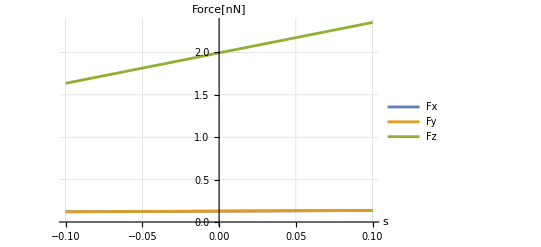

```mathematica
R = 45.5*10^-6;
dx = -100*10^-6;
bz = 3.3;
μ = 4π*10^-7;
dy = -100*10^-6;
dz = -389*10^-6;
p1 = Plot[{-(bz^2 dx π R^3 (5+3 s))/(10 μ)*10^9, -(bz^2 dy π R^3 (5+3 s))/(10 μ)*10^9, -(2 bz^2 dz π R^3 (5+9 s))/(5 μ)*10^9}, {s , -0.1, 0.1}, AxesLabel->{"s","Force[nN]"}, GridLines->Automatic, PlotLegends->{"Fx", "Fy", "Fz"}]
Clear[R,dx,dy,dz,bz,μ];
```

```mathematica
Export["plot_FVsS_dxdydz_analytical.pdf", p1]
```

plot_FVsS_dxdydz_analytical.pdf

### Fy

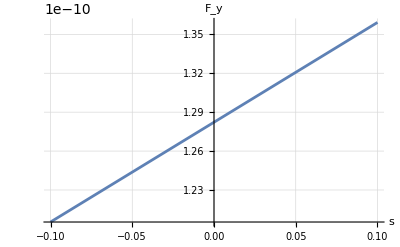

```mathematica
R = 45.5*10^-6;
dy = -100*10^-6;
bz = 3.3;
μ = 4π*10^-7;
Plot[-(bz^2 dy π R^3 (5+3 s))/(10 μ), {s , -0.1, 0.1}, AxesLabel->{"s","F_y"}, GridLines->Automatic]
Clear[R,dy,bz,μ];
```

### Fz

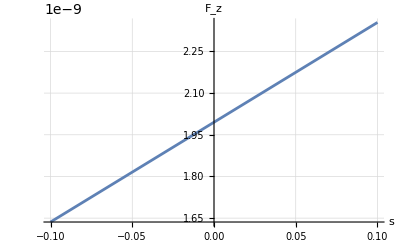

```mathematica
R = 45.5*10^-6;
dz = -389*10^-6;
bz = 3.3;
μ = 4π*10^-7;
Plot[-(2 bz^2 dz π R^3 (5+9 s))/(5 μ), {s , -0.1, 0.1}, AxesLabel->{"s","F_z"}, GridLines->Automatic]
Clear[R,dz,bz,μ];
```

## Fx, Fy, Fz Vs dx, dy, dz respectively

### Fy

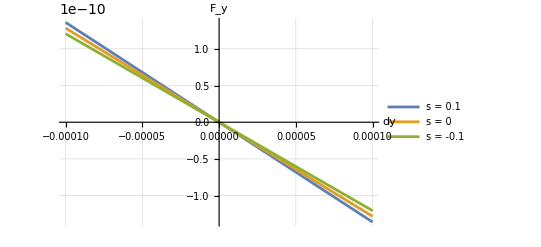

```mathematica
R = 45.5*10^-6;
bz = 3.3;
μ = 4π*10^-7;
Plot[{-(bz^2 dy π R^3 (5+3 s))/(10 μ)/.{s->0.1}, -(bz^2 dy π R^3 (5+3 s))/(10 μ)/.{s->0}, -(bz^2 dy π R^3 (5+3 s))/(10 μ)/.{s->-0.1}}, {dy , -100*10^-6, 100*10^-6}, AxesLabel->{"dy","F_y"}, GridLines->Automatic, PlotLegends->{"s = 0.1", "s = 0", "s = -0.1"}]
Clear[R,bz,μ];
```

### Fz

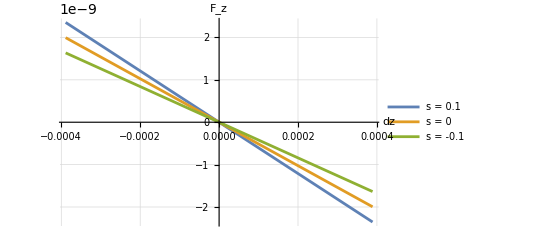

```mathematica
R = 45.5*10^-6;
bz = 3.3;
μ = 4π*10^-7;
Plot[{-(2 bz^2 dz π R^3 (5+9 s))/(5 μ)/.{s->0.1}, -(2 bz^2 dz π R^3 (5+9 s))/(5 μ)/.{s->0}, -(2 bz^2 dz π R^3 (5+9 s))/(5 μ)/.{s->-0.1}}, {dz , -389*10^-6, 389*10^-6}, AxesLabel->{"dz","F_z"}, GridLines->Automatic, PlotLegends->{"s = 0.1", "s = 0", "s = -0.1"}]
Clear[R,bz,μ];
```

### Fx

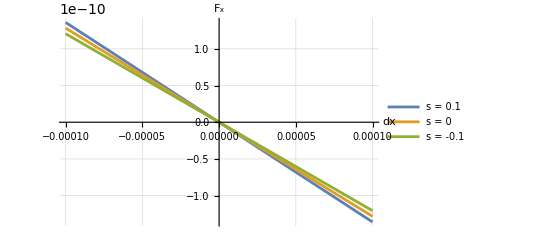

```mathematica
R = 45.5*10^-6;
bz = 3.3;
μ = 4π*10^-7;
Plot[{-(bz^2 dx π R^3 (5+3 s))/(10 μ)/.{s->0.1}, -(bz^2 dx π R^3 (5+3 s))/(10 μ)/.{s->0}, -(bz^2 dx π R^3 (5+3 s))/(10 μ)/.{s->-0.1}}, {dx , -100*10^-6, 100*10^-6}, AxesLabel->{"dx","F_x"}, GridLines->Automatic, PlotLegends->{"s = 0.1", "s = 0", "s = -0.1"}]
Clear[R,bz,μ];
```